# Bosonic CoP/EoP Data Hugo - 6 Nov 2019

## For the CFT Vacuum State & Gaussian Purifications

These are the data sets for complexity and entanglement of purification for a boson on a circle and on a line.

## Boson on a Circle

## CoP

The function used in the Gaussian optimization is CoPVal[NN, m, δ, μ, dimA1, dimB1, d] where:
NN is the total number of lattice points
m is the mass of the scalar field
δ is the lattice spacing (which will be kept fixed)
L=NN δ is the length of the circle
μ is the reference state frequency (assumed to be 1 in the following)
dimA1 is the number of sites in partition A1 of the subsystem
dimB1 is the number of sites in partition B1 of the subsystem
d is the lattice separation between the subsystem partitions A1 and B1
dimPur=dimA1+dimB1 is the dimension of the

In the following ‘w’ is also being used as the number of sites in the partitions A1 and B1 (assumed to be the same).

### Data {d/w,CoPVal[NN, m/w ,δ, μ = 1 ,w, w, d]}. CoP[d/w] (RUN)

```mathematica
(*(*CoPCircleListN100dA1=Table[{d,CoPVal[100,1/100,1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)*)
```

```mathematica
CoPCircleListN100dA1={{0,3.640315804781124},{1,3.677627033925028},{2,3.6797260548746866},{3,3.680371188959455},{4,3.680710148509393},{5,3.6809352587814788},{6,3.681103586292271},{7,3.6812382305650577},{8,3.681350560669364},{9,3.681446951477339},{10,3.681531330002338},{11,3.6816062942524557},{12,3.6816736290586647},{13,3.681734658542095},{14,3.681790356126732},{15,3.6818414753170043},{16,3.6818886087225935},{17,3.6819322310711757},{18,3.6819727313191346},{19,3.682010424104942},{20,3.68204557947238},{21,3.682078422878344},{22,3.682109145246019},{23,3.682137910920508},{24,3.682164863119715},{25,3.682190122293376},{26,3.6822137994479363},{27,3.682235988299231},{28,3.6822567726536497},{29,3.6822762278872845},{30,3.6822944144232235},{31,3.6823113977500084},{32,3.68232722342413},{33,3.682341942299204},{34,3.682355594702527},{35,3.6823682175464056},{36,3.682379844068008},{37,3.682390504270999},{38,3.6824002230863155},{39,3.6824090258098656},{40,3.6824169313589805},{41,3.6824239594036148},{42,3.6824301252577123},{43,3.6824354412966382},{44,3.682439921029486},{45,3.6824435760501677},{46,3.682446406402046},{47,3.682448425311343},{48,3.6824496351209235},{49,3.6824500381947556}};
```

```mathematica
(*CoPCircleListN200dA2=Table[{d/2,CoPVal[200,1/200,1/100,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
CoPCircleListN200dA2={{0,5.609840678074752},{1/2,5.653773081508451},{1,5.6564709750233435},{3/2,5.657231702314633},{2,5.6575851346221215},{5/2,5.657796835407756},{3,5.657943603986851},{7/2,5.658054937620205},{4,5.658144475808819},{9/2,5.658219406008512},{5,5.658283904478057},{11/2,5.658340585450474},{6,5.658391185258884},{13/2,5.658436911838434},{7,5.658478639091765},{15/2,5.658517019264264},{8,5.658552552031936},{17/2,5.658585629511144},{9,5.658616564615238},{19/2,5.658645611680295},{10,5.6586729802069025},{21/2,5.658698852720662},{11,5.658723353123904},{23/2,5.658746630376208},{12,5.658768784682537},{25/2,5.658789909352857},{13,5.658810085828268},{27/2,5.6588293855744265},{14,5.658847871760991},{29/2,5.658865600085594},{15,5.6588826207327685},{31/2,5.658898978292604},{16,5.658914712953166},{33/2,5.658929860987993},{17,5.658944455251202},{35/2,5.658958525591399},{18,5.658972099303586},{37/2,5.658985201026474},{19,5.658997853772777},{39/2,5.659010078418951},{20,5.659021894222262},{41/2,5.6590333190942985},{21,5.659044369155712},{43/2,5.659055059960966},{22,5.659065405548663},{45/2,5.659075419049353},{23,5.659085112711809},{47/2,5.659094497941716},{24,5.65910358537474},{49/2,5.659112384996555},{25,5.659120906097422},{51/2,5.659129157501897},{26,5.659137147188184},{53/2,5.659144883147237},{27,5.659152372394078},{55/2,5.659159621655506},{28,5.6591666375870044},{57/2,5.659173426104801},{29,5.659179992909946},{59/2,5.659186343360342},{30,5.659192482529568},{61/2,5.65919841595677},{31,5.659204145911928},{63/2,5.659209678864161},{32,5.659215018174843},{65/2,5.659220167632916},{33,5.659225130856384},{67/2,5.6592299112507405},{34,5.659234512054184},{69/2,5.65923893634575},{35,5.6592431869406585},{71/2,5.659247267589987},{36,5.659251178065325},{73/2,5.65925492347498},{37,5.659258505345813},{75/2,5.659261925790242},{38,5.6592651868583355},{77/2,5.659268290472447},{39,5.659271238447429},{79/2,5.65927403248122},{40,5.659276674176473},{81/2,5.659279165025824},{41,5.659281506423601},{83/2,5.659283699668504},{42,5.659285745971853},{85/2,5.659287646444457},{43,5.659289402148426},{87/2,5.659291013981352},{44,5.659292482790446},{89/2,5.659293809483222},{45,5.659294994552669},{91/2,5.6592960388072795},{46,5.659296942732004},{93/2,5.65929770680411},{47,5.659298331386838},{95/2,5.659298816858713},{48,5.65929916343442},{97/2,5.6592993713114135},{49,5.659299440671955}};
```

```mathematica
(*CoPCircleListN300dA3=Table[{d/3,CoPVal[300,1/300,1/100,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
CoPCircleListN300dA3={{0,7.268807485075827},{1/3,7.314021648187472},{2/3,7.317082314714281},{1,7.317960366162449},{4/3,7.31835540585841},{5/3,7.3185806736369825},{2,7.318729294202504},{7/3,7.318837241773305},{8/3,7.31892100159575},{3,7.318989110919034},{10/3,7.319046418176921},{11/3,7.319095883072515},{4,7.319139420248123},{13/3,7.319178328451542},{14/3,7.319213524015308},{5,7.3192456752657},{16/3,7.319275283859489},{17/3,7.319302733809659},{6,7.319328328367085},{19/3,7.319352308488529},{20/3,7.319374869976686},{7,7.319396174046483},{22/3,7.319416354938475},{23/3,7.319435524745241},{8,7.319453780597523},{25/3,7.319471204603859},{26/3,7.319487871755669},{9,7.319503832761257},{28/3,7.319519153375638},{29/3,7.319533877729769},{10,7.319548048379317},{31/3,7.319561703181179},{32/3,7.319574875983526},{11,7.319587597422292},{34/3,7.31959989468075},{35/3,7.319611792943724},{12,7.319623314787539},{37/3,7.319634481084308},{38/3,7.3196453171706795},{13,7.319655818941346},{40/3,7.319666024524276},{41/3,7.3196759407570715},{14,7.319685581454165},{43/3,7.319694959060164},{44/3,7.319704085150805},{15,7.31971297053479},{46/3,7.319721625260787},{47/3,7.319730058670104},{16,7.319738279984457},{49/3,7.319746296007723},{50/3,7.319754115791547},{17,7.319761746241627},{52/3,7.319769193598234},{53/3,7.319776464763329},{18,7.319783592487304},{55/3,7.319790501382372},{56/3,7.319797277927645},{19,7.3198039000500055},{58/3,7.319810372572349},{59/3,7.319816699987759},{20,7.319822886565375},{61/3,7.319828936375328},{62/3,7.3198348532585715},{21,7.319840640891211},{64/3,7.31984630274385},{65/3,7.319851842132013},{22,7.319857262228912},{67/3,7.31986256602281},{68/3,7.319867756389608},{23,7.3198728362877326},{70/3,7.319877807699839},{71/3,7.31988267375392},{24,7.319887436793433},{73/3,7.319892098596122},{74/3,7.319896661869229},{25,7.319901128538292},{76/3,7.31990550059843},{77/3,7.319909779985477},{26,7.31991396854111},{79/3,7.319918069238085},{80/3,7.319922080187251},{27,7.3199260068739855},{82/3,7.3199298488778375},{83/3,7.319933608695945},{28,7.319937286831002},{85/3,7.319940885396072},{86/3,7.3199444055040574},{29,7.319947848377102},{88/3,7.319951215543645},{89/3,7.319954507471219},{30,7.319957726569261},{91/3,7.31996087208741},{92/3,7.319963947841994},{31,7.3199669508958625},{94/3,7.319969885575654},{95/3,7.319972751852975},{32,7.319975550488397},{97/3,7.319978282506981},{98/3,7.319980948592287},{33,7.319983549701687},{100/3,7.319986086620921},{101/3,7.31998856002109},{34,7.319990970688004},{103/3,7.319993319487568},{104/3,7.31999560662665},{35,7.319997833210649},{106/3,7.319999999828954},{107/3,7.320002106960887},{36,7.3200041550288955},{109/3,7.320006144930669},{110/3,7.320008077054672},{37,7.320009951971047},{112/3,7.320011770166604},{113/3,7.320013532061423},{38,7.320015238111632},{115/3,7.320016888954555},{116/3,7.320018484732599},{39,7.320020026001297},{118/3,7.3200215131987},{119/3,7.320022946684045},{40,7.320024326762302},{121/3,7.320025653798852},{122/3,7.320026928132758},{41,7.320028150108283},{124/3,7.320029319955775},{125/3,7.320030438019186},{42,7.320031504582779},{127/3,7.320032519925402},{128/3,7.320033484031764},{43,7.320034397445628},{130/3,7.320035260284479},{131/3,7.320036072744846},{44,7.320036835032091},{133/3,7.3200375473899575},{134/3,7.320038209741775},{45,7.3200388224895985},{136/3,7.320039385692845},{137/3,7.320039899511958},{46,7.320040364008237},{139/3,7.320040779340145},{140/3,7.320041145671381},{47,7.320041462810731},{142/3,7.320041731119312},{143/3,7.3200419505796654},{48,7.320042121192262},{145/3,7.320042243038008},{146/3,7.320042316137584},{49,7.320042340568462}};
```

```mathematica
(*CoPCircleListN400dA4=Table[{d/4,CoPVal[400,1/400,1/100,1,4,4,d]},{d,0,(400-(4+4))/2}]*)
```

```mathematica
CoPCircleListN400dA4={{0,8.741594760907278},{1/4,8.786596484402997},{1/2,8.789873928282004},{3/4,8.79084668498708},{1,8.79128464273309},{5/4,8.79152998420066},{3/2,8.791687697216837},{7/4,8.791799087478507},{2,8.791883242124253},{9/4,8.791950052896334},{5/2,8.792005110841629},{11/4,8.792051799611961},{3,8.792092283565747},{13/4,8.792128011820877},{7/2,8.792159992689555},{15/4,8.79218895105554},{4,8.79221542287252},{17/4,8.79223981412271},{9/2,8.792262438901366},{19/4,8.792283545630545},{5,8.792303330416043},{21/4,8.79232195689667},{11/2,8.792339557193115},{23/4,8.792356242042006},{6,8.792372104713234},{25/4,8.792387224917857},{13/2,8.79240166926374},{27/4,8.79241549781982},{7,8.792428761113475},{29/4,8.792441504027428},{15/2,8.792453765935052},{31/4,8.792465581564189},{8,8.792476982166388},{33/4,8.792487995474216},{17/2,8.792498646448097},{35/4,8.79250895758444},{9,8.79251894918427},{37/4,8.792528639890591},{19/2,8.79253804628392},{39/4,8.792547186015785},{10,8.792556067016829},{41/4,8.792564708341374},{21/2,8.792573119920162},{43/4,8.792581312730347},{11,8.792589297027341},{45/4,8.792597082234565},{23/2,8.792604677136193},{47/4,8.792612089936876},{12,8.792619328220566},{49/4,8.79262639916129},{25/2,8.792633309397328},{51/4,8.792640065181555},{13,8.792646672388427},{53/4,8.792653137523306},{27/2,8.792659462747354},{55/4,8.792665655949568},{14,8.792671720767059},{57/4,8.792677661519566},{29/2,8.792683482341417},{59/4,8.792689189759463},{15,8.792694779548963},{61/4,8.792700263101036},{31/2,8.792705641150564},{63/4,8.792710916789018},{16,8.792716093110329},{65/4,8.79272117301963},{33/2,8.792726158817912},{67/4,8.792731053585346},{17,8.792735859632412},{69/4,8.792740580311076},{35/2,8.792745214916893},{71/4,8.792749768526875},{18,8.792754242273736},{73/4,8.792758638150412},{37/2,8.792762958015352},{75/4,8.792767203702008},{19,8.792771376922442},{77/4,8.792775479587208},{39/2,8.79277951265375},{79/4,8.79278347829636},{20,8.79278737779961},{81/4,8.792791212576224},{41/2,8.792794984013042},{83/4,8.792798693405903},{21,8.792802342050768},{85/4,8.792805931142361},{43/2,8.792809461889563},{87/4,8.792812935417235},{22,8.79281635282892},{89/4,8.792819715147978},{45/2,8.792823023422468},{91/4,8.792826278679415},{23,8.792829481792229},{93/4,8.792832633726302},{47/2,8.792835735365315},{95/4,8.79283878762995},{24,8.792841791255665},{97/4,8.792844747018686},{49/2,8.792847655828792},{99/4,8.792850518382076},{25,8.792853335365534},{101/4,8.792856107549856},{51/2,8.792858835609433},{103/4,8.792861520185925},{26,8.79286416191952},{105/4,8.792866761454322},{53/2,8.792869319575535},{107/4,8.792871836327539},{27,8.792874312807664},{109/4,8.792876749400305},{55/2,8.792879146630531},{111/4,8.79288150515632},{28,8.792883825118993},{113/4,8.79288610734356},{57/2,8.79288835224911},{115/4,8.792890560213337},{29,8.792892731964196},{117/4,8.792894867262678},{59/2,8.792896967366081},{119/4,8.792899031982525},{30,8.792901061971424},{121/4,8.792903057584857},{61/2,8.792905019186191},{123/4,8.792906947166047},{31,8.792908841869101},{125/4,8.792910703637121},{63/2,8.792912532909753},{127/4,8.792914329740665},{32,8.792916094724577},{129/4,8.792917828093733},{65/2,8.792919530141237},{131/4,8.792921201260887},{33,8.79292284139806},{133/4,8.792924451199164},{67/2,8.792926030812483},{135/4,8.792927580492403},{34,8.79292910049715},{137/4,8.792930591113937},{69/2,8.792932052531322},{139/4,8.792933485002939},{35,8.792934888700929},{141/4,8.792936263979328},{71/2,8.792937610962342},{143/4,8.79293892991781},{36,8.792940220994158},{145/4,8.79294148438324},{73/2,8.792942722073581},{147/4,8.792943929003767},{37,8.79294511057672},{149/4,8.7929462652285},{75/2,8.792947393139041},{151/4,8.792948494483051},{38,8.79294956940568},{153/4,8.792950618063982},{77/2,8.792951640635648},{155/4,8.792952637234396},{39,8.79295360803823},{157/4,8.792954553146112},{79/2,8.792955472706426},{159/4,8.792956366881853},{40,8.792957235761241},{161/4,8.79295807948613},{81/2,8.79295889818961},{163/4,8.792959697965582},{41,8.792960460880614},{165/4,8.792961205066398},{83/2,8.792961924732923},{167/4,8.792962619767232},{42,8.792963290464897},{169/4,8.79296393677129},{85/2,8.792964558886883},{171/4,8.792965156842017},{43,8.792965730699503},{173/4,8.792966280586024},{87/2,8.792966806519617},{175/4,8.792967308602677},{44,8.792967786910712},{177/4,8.792968241481999},{89/2,8.792968672388323},{179/4,8.792969079743095},{45,8.792969463433964},{181/4,8.792969824459464},{91/2,8.792970160436116},{183/4,8.792970473790676},{46,8.792970763785082},{185/4,8.792971030420107},{93/2,8.792971273795237},{187/4,8.792971496214424},{47,8.792971690682826},{189/4,8.792971864285358},{95/2,8.79297201471305},{191/4,8.792972141987443},{48,8.792972246066107},{193/4,8.792972327101367},{97/2,8.792972384799228},{195/4,8.792972419500062},{49,8.792972434378425}};
```

```mathematica
(*CoPCircleListN500dA5=Table[{d/5,CoPVal[500,1/500,1/100,1,5,5,d]},{d,0,(500-(5+5))/2}]*)
```

```mathematica
CoPCircleListN500dA5={{0,10.085934420407508},{1/5,10.130222898299957},{2/5,10.133630191613458},{3/5,10.134676019998448},{4/5,10.135152368354062},{1,10.135418451813067},{6/5,10.135587539771224},{7/5,10.13570506917759},{8/5,10.135792305936347},{9/5,10.135860352987118},{2,10.135915502963417},{11/5,10.13596156582317},{12/5,10.136000967635969},{13/5,10.13603532737931},{14/5,10.136065762620722},{3,10.136093070944169},{16/5,10.136117837066601},{17/5,10.136140499992317},{18/5,10.136161396306603},{19/5,10.136180788932363},{4,10.136198886580232},{21/5,10.13621585750368},{22/5,10.136231839013968},{23/5,10.13624694458933},{24/5,10.136261268977215},{5,10.136274892831219},{26/5,10.13628788217046},{27/5,10.136300297341961},{28/5,10.136312188120852},{29/5,10.136323598265276},{6,10.136334566388843},{31/5,10.136345126132905},{32/5,10.136355307614227},{33/5,10.136365137405216},{34/5,10.136374639303561},{7,10.136383835186603},{36/5,10.136392743009969},{37/5,10.136401381444148},{38/5,10.136409765923474},{39/5,10.136417910834268},{8,10.136425829273806},{41/5,10.136433533406848},{42/5,10.136441034166593},{43/5,10.136448341810645},{44/5,10.136455466520053},{9,10.136462414526273},{46/5,10.13646919642111},{47/5,10.136475818772068},{48/5,10.136482288598751},{49/5,10.136488612373645},{10,10.13649479618123},{51/5,10.136500845700425},{52/5,10.13650676677166},{53/5,10.136512562699197},{54/5,10.136518242410716},{11,10.136523801962197},{56/5,10.136529253364692},{57/5,10.136534597982942},{58/5,10.136539839741467},{59/5,10.13654498112065},{12,10.13655002656473},{61/5,10.136554978659568},{62/5,10.136559841115808},{63/5,10.136564615411766},{64/5,10.136569304843372},{13,10.136573912392883},{66/5,10.1365784402138},{67/5,10.136582890567796},{68/5,10.136587265672981},{69/5,10.1365915676651},{14,10.136595798552595},{71/5,10.136599960276813},{72/5,10.136604054523204},{73/5,10.136608083195197},{74/5,10.136612047971559},{15,10.136615950997085},{76/5,10.136619792540792},{77/5,10.136623574641956},{78/5,10.136627299266433},{79/5,10.136630967378244},{16,10.13663458038272},{81/5,10.136638139441825},{82/5,10.136641645848195},{83/5,10.13664510076875},{84/5,10.136648505284128},{17,10.136651860488028},{86/5,10.136655167512854},{87/5,10.136658427233963},{88/5,10.136661640771504},{89/5,10.136664808941642},{18,10.136667932760261},{91/5,10.136671012996883},{92/5,10.136674050599108},{93/5,10.136677046283278},{94/5,10.136680000880103},{19,10.13668291524255},{96/5,10.13668579004588},{97/5,10.136688626812383},{98/5,10.136691423817632},{99/5,10.136694184475033},{20,10.136696907664701},{101/5,10.136699594997733},{102/5,10.136702246760013},{103/5,10.136704863531763},{104/5,10.136707445940297},{21,10.136709994481961},{106/5,10.136712509748579},{107/5,10.136714992239302},{108/5,10.136717442513282},{109/5,10.136719861017884},{22,10.136722248209601},{111/5,10.136724604676331},{112/5,10.1367269331592},{113/5,10.136729227741782},{114/5,10.136731493708428},{23,10.13673373137863},{116/5,10.136735940484476},{117/5,10.136738121263651},{118/5,10.136740274296328},{119/5,10.136742399804756},{24,10.136744498377007},{121/5,10.136746570437962},{122/5,10.136748615796348},{123/5,10.13675063455925},{124/5,10.13675262804508},{25,10.136754596160111},{126/5,10.136756539235426},{127/5,10.136758457573867},{128/5,10.136760351328126},{129/5,10.13676222097225},{26,10.136764066856815},{131/5,10.136765888834589},{132/5,10.136767687599168},{133/5,10.136769463333799},{134/5,10.13677121619725},{27,10.13677294651038},{136/5,10.136774654508908},{137/5,10.136776340401354},{138/5,10.136778005109676},{139/5,10.136779646890135},{28,10.136781267900242},{141/5,10.136782867814897},{142/5,10.136784447045386},{143/5,10.136786004837278},{144/5,10.136787542426225},{29,10.136789059675845},{146/5,10.136790556785197},{147/5,10.136792033930186},{148/5,10.136793491949073},{149/5,10.136794929020413},{30,10.13679634737534},{151/5,10.136797746464339},{152/5,10.136799128848242},{153/5,10.13680048758905},{154/5,10.136801829977287},{31,10.136803153711694},{156/5,10.136804459069763},{157/5,10.136805746152131},{158/5,10.136807015068628},{159/5,10.136808267052963},{32,10.1368094992577},{161/5,10.136810714505696},{162/5,10.136811912317715},{163/5,10.136813092716043},{164/5,10.136814256126165},{33,10.136815401731567},{166/5,10.136816530572458},{167/5,10.13681764257095},{168/5,10.136818737613863},{169/5,10.136819816885659},{34,10.13682087792069},{171/5,10.136821923362762},{172/5,10.136822952200054},{173/5,10.136823964939092},{174/5,10.136824961537464},{35,10.136825942039925},{176/5,10.136826906663003},{177/5,10.136827855389868},{178/5,10.13682878839102},{179/5,10.136829705946237},{36,10.136830607572188},{181/5,10.136831493664335},{182/5,10.136832364491056},{183/5,10.136833220031463},{184/5,10.136834060648301},{37,10.136834885480113},{186/5,10.136835696235414},{187/5,10.136836490664628},{188/5,10.13683727083163},{189/5,10.136838036133577},{38,10.136838786720991},{191/5,10.136839523225886},{192/5,10.136840243772877},{193/5,10.13684095090042},{194/5,10.136841642597103},{39,10.136842320339985},{196/5,10.136842983637319},{197/5,10.1368436326488},{198/5,10.136844267881148},{199/5,10.136844888000931},{40,10.136845494423927},{201/5,10.1368460867852},{202/5,10.13684666508784},{203/5,10.136847229410957},{204/5,10.136847779752044},{41,10.136848316244803},{206/5,10.136848838915984},{207/5,10.136849348009072},{208/5,10.13684984290896},{209/5,10.136850324277392},{42,10.136850792040983},{211/5,10.136851246179681},{212/5,10.13685168672284},{213/5,10.136852113739428},{214/5,10.136852527196902},{43,10.136852927308077},{216/5,10.136853313831416},{217/5,10.136853686967036},{218/5,10.136854046770395},{219/5,10.136854393183157},{44,10.136854726326124},{221/5,10.136855046193233},{222/5,10.136855353318449},{223/5,10.136855646136672},{224/5,10.136855926308915},{45,10.136856193799758},{226/5,10.136856447066478},{227/5,10.136856687709784},{228/5,10.1368569152461},{229/5,10.136857129654471},{46,10.136857331024228},{231/5,10.136857519329478},{232/5,10.136857694506562},{233/5,10.136857856908463},{234/5,10.136858005940343},{47,10.136858142021977},{236/5,10.136858265603834},{237/5,10.136858375341934},{238/5,10.136858472525576},{239/5,10.136858556741066},{48,10.136858627985474},{241/5,10.136858686262824},{242/5,10.136858732716357},{243/5,10.136858763940987},{244/5,10.136858783396553},{49,10.136858789888676}};
```

```mathematica
(*CoPCircleListN600dA6=Table[{d/6,CoPVal[600,1/600,1/100,1,6,6,d]},{d,0,(600-(6+6))/2}]*)
```

```mathematica
CoPCircleListN600dA6={{0,11.334284173767317},{1/6,11.377691810778808},{1/3,11.381175571218078},{1/2,11.382277225891652},{2/3,11.382786425244188},{5/6,11.383071967438275},{1,11.383252796003411},{7/6,11.383377465371675},{4/3,11.383469006718885},{3/2,11.383539553559011},{5/3,11.38359602823543},{11/6,11.383642630872707},{2,11.383682045340628},{13/6,11.383716057075182},{7/3,11.383745897199361},{5/2,11.383772441641817},{8/3,11.383796329628302},{17/6,11.38381803861267},{3,11.383837940834805},{19/6,11.383856294697265},{10/3,11.38387334739841},{7/2,11.383889269519624},{11/3,11.383904206017785},{23/6,11.383918275803214},{4,11.383931577606159},{25/6,11.383944194190466},{13/3,11.383956195560302},{9/2,11.383967641368061},{14/3,11.383978582872027},{29/6,11.383989064531226},{5,11.383999124938656},{31/6,11.384008798069797},{16/3,11.384018113380328},{11/2,11.384027097678949},{17/3,11.384035775318564},{35/6,11.384044164597231},{6,11.384052286655141},{37/6,11.384060158106605},{19/3,11.38406779413239},{13/2,11.384075208630708},{20/3,11.384082414266437},{41/6,11.384089422626792},{7,11.384096244541347},{43/6,11.384102889114953},{22/3,11.38410936615517},{15/2,11.384115682939738},{23/3,11.384121847915912},{47/6,11.38412786788789},{8,11.38413374937187},{49/6,11.38413949857042},{25/3,11.38414512273265},{17/2,11.384150622253397},{26/3,11.38415600709324},{53/6,11.384161280227696},{9,11.384166446006537},{55/6,11.384171508634441},{28/3,11.384176471680597},{19/2,11.3841813391021},{29/3,11.384186114229323},{59/6,11.384190800748012},{10,11.38419540064389},{61/6,11.384199917049122},{31/3,11.38420435351965},{21/2,11.384208712171954},{32/3,11.384212995467372},{65/6,11.384217205858768},{11,11.384221345571211},{67/6,11.384225416519305},{34/3,11.38422942077833},{23/2,11.38423336056585},{35/3,11.38423723743083},{71/6,11.384241053169639},{12,11.384244809588449},{73/6,11.38424850818087},{37/3,11.384252150563112},{25/2,11.384255738085207},{38/3,11.384259272444082},{77/6,11.384262754488708},{13,11.38426618596278},{79/6,11.38426956794823},{40/3,11.384272901641502},{27/2,11.384276188235662},{41/3,11.384279428809336},{83/6,11.3842826244226},{14,11.384285776092463},{85/6,11.384288886222595},{43/3,11.384291951755005},{29/2,11.384294977239891},{44/3,11.384297962729361},{89/6,11.38430090892976},{15,11.384303816501513},{91/6,11.384306686473503},{46/3,11.384309519386006},{31/2,11.384312316219592},{47/3,11.384315077596556},{95/6,11.384317803956485},{16,11.384320496300495},{97/6,11.384323155189518},{49/3,11.38432578122265},{33/2,11.384328375063994},{50/3,11.384330937316987},{101/6,11.384333468436326},{17,11.38433596909449},{103/6,11.384338439749614},{52/3,11.384340880974223},{35/2,11.384343293288676},{53/3,11.384345677129776},{107/6,11.38434803302791},{18,11.384350363590158},{109/6,11.384352662799625},{55/3,11.384354937552692},{37/2,11.384357186379336},{56/3,11.384359409014207},{113/6,11.384361606431296},{19,11.384363779023941},{115/6,11.384365926876802},{58/3,11.384368050511016},{39/2,11.384370150703242},{59/3,11.384372226770546},{119/6,11.384374280010128},{20,11.384376310395407},{121/6,11.384378318325414},{61/3,11.384380304089921},{41/2,11.384382268093661},{62/3,11.384384210305559},{125/6,11.384386131364106},{21,11.38438803142047},{127/6,11.384389910882303},{64/3,11.38439177013572},{43/2,11.384393608681034},{65/3,11.384395427596505},{131/6,11.384397226919067},{22,11.384399006827943},{133/6,11.384400767611},{67/3,11.384402509463321},{45/2,11.38440423260233},{68/3,11.384405937393224},{137/6,11.384407623870997},{23,11.384409292355926},{139/6,11.384410943094815},{70/3,11.384412576240525},{47/2,11.384414191900245},{71/3,11.384415790405294},{143/6,11.384417371949038},{24,11.38441893668856},{145/6,11.384420484741982},{73/3,11.384422016408372},{49/2,11.384423531750867},{74/3,11.384425030991657},{149/6,11.384426514343662},{25,11.384427981945803},{151/6,11.384429433987565},{76/3,11.384430870908517},{51/2,11.384432291853555},{77/3,11.384433697992984},{155/6,11.384435089400819},{26,11.384436465549513},{157/6,11.384437827162683},{79/3,11.384439174323962},{53/2,11.384440506995649},{80/3,11.384441825473775},{161/6,11.384443129792912},{27,11.384444420160472},{163/6,11.384445696652097},{82/3,11.384446959104046},{55/2,11.384448208139103},{83/3,11.384449443613498},{167/6,11.3844506657167},{28,11.384451874531312},{169/6,11.384453070212185},{85/3,11.384454252750622},{57/2,11.384455422442503},{86/3,11.384456579208637},{173/6,11.384457723277592},{29,11.384458854682922},{175/6,11.384459973550529},{88/3,11.38446108139562},{59/2,11.384462174141463},{89/3,11.384463255972477},{179/6,11.384464325691853},{30,11.38446538330451},{181/6,11.384466429107517},{91/3,11.384467462826178},{61/2,11.384468484785957},{92/3,11.384469495083131},{185/6,11.384470493772243},{31,11.38447148091389},{187/6,11.384472456532707},{94/3,11.384473420840278},{63/2,11.384474373757046},{95/3,11.38447531547607},{191/6,11.384476246046853},{32,11.384477165542112},{193/6,11.384478074035762},{97/3,11.384478971607654},{65/2,11.38447985827542},{98/3,11.384480734008267},{197/6,11.38448159917684},{33,11.384482453604518},{199/6,11.384483297622493},{100/3,11.384484132233267},{67/2,11.384484953516148},{101/3,11.384485765838708},{203/6,11.38448656787889},{34,11.384487359608636},{205/6,11.384488141041972},{103/3,11.384488912335065},{69/2,11.384489673456248},{104/3,11.384490424514333},{209/6,11.384491165564146},{35,11.384491896571515},{211/6,11.384492617756765},{106/3,11.38449332898714},{71/2,11.384494030404571},{107/3,11.384494722084225},{215/6,11.384495404231853},{36,11.384496079482954},{217/6,11.384496739282104},{109/3,11.384497391884059},{73/2,11.384498035435545},{110/3,11.384498669454267},{221/6,11.384499293944176},{37,11.384499909055087},{223/6,11.384500514862884},{112/3,11.384501112565058},{75/2,11.384501698296559},{113/3,11.384502276164755},{227/6,11.38450284478112},{38,11.384503404385214},{229/6,11.384503954503721},{115/3,11.38450449570703},{77/2,11.384505027835988},{116/3,11.384505550891204},{233/6,11.384506064987272},{39,11.384506570074924},{235/6,11.384507066211723},{118/3,11.384507553422152},{79/2,11.384508031763872},{119/3,11.384508501271407},{239/6,11.384508961948315},{40,11.384509413786361},{241/6,11.384509856959438},{121/3,11.384510291317742},{81/2,11.384510717038133},{122/3,11.384511133976703},{245/6,11.3845115424313},{41,11.384511941975115},{247/6,11.384512333075303},{124/3,11.384512715544917},{83/2,11.38451308946505},{125/3,11.384513454887921},{251/6,11.384513812021627},{42,11.384514160113389},{253/6,11.384514500018302},{127/3,11.38451483142426},{85/2,11.384515154469097},{128/3,11.38451546910047},{257/6,11.384515775249838},{43,11.384516073120379},{259/6,11.384516363133214},{130/3,11.384516643635925},{87/2,11.384516916487156},{131/3,11.38451718090594},{263/6,11.384517437122247},{44,11.384517684986013},{265/6,11.384517924698933},{133/3,11.384518155959801},{89/2,11.384518379126332},{134/3,11.38451859405309},{269/6,11.384518800741786},{45,11.38451899923321},{271/6,11.384519189539269},{136/3,11.384519371687679},{91/2,11.384519545655442},{137/3,11.384519711611691},{275/6,11.384519869102027},{46,11.38452001870598},{277/6,11.384520160173945},{139/3,11.384520293267329},{93/2,11.384520418484227},{140/3,11.384520535433307},{281/6,11.384520644384802},{47,11.384520745288397},{283/6,11.384520838004924},{142/3,11.384520922712326},{95/2,11.384520999322636},{143/3,11.384521067812383},{287/6,11.384521128266394},{48,11.384521180633083},{289/6,11.3845212249648},{145/3,11.384521261203679},{97/2,11.384521289448394},{146/3,11.384521309539684},{293/6,11.384521321657457},{49,11.3845213256698}};
```

```mathematica
(*CoPCircleListN800dA8=Table[{d/8,CoPVal[800,1/800,1/100,1,8,8,d]},{d,0,(800-(8+8))/2}]*)
```

```mathematica
CoPCircleListN800dA8={{0,13.618369188922275},{1/8,13.659951470200777},{1/4,13.663498020917636},{3/8,13.66467479070946},{1/2,13.66523477672538},{5/8,13.665553468678763},{3/4,13.665756119793551},{7/8,13.665895332024759},{1,13.665996635271108},{9/8,13.66607373296567},{5/4,13.666134554749473},{11/8,13.666183964890157},{3/2,13.66622509240447},{13/8,13.666260029618767},{7/4,13.666290222505351},{15/8,13.666316700270118},{2,13.666340212080954},{17/8,13.66636131632755},{9/4,13.66638043684908},{19/8,13.666397901011694},{5/2,13.66641396572076},{21/8,13.666428834904664},{11/4,13.666442672907545},{23/8,13.66645561467667},{3,13.666467768579714},{25/8,13.666479228023912},{13/4,13.666490069508216},{27/8,13.666500357953947},{7/2,13.666510149020741},{29/8,13.666519490150824},{15/4,13.666528422390346},{31/8,13.66653698151124},{4,13.666545198713687},{33/8,13.666553101608882},{17/4,13.666560714534704},{35/8,13.666568058465717},{9/2,13.666575152733135},{37/8,13.66658201488809},{19/4,13.666588660054208},{39/8,13.66659510214116},{5,13.666601353563529},{41/8,13.666607426018386},{21/4,13.666613330111975},{43/8,13.666619073934564},{11/2,13.666624668122521},{45/8,13.666630118641761},{23/4,13.666635434611846},{47/8,13.666640621586367},{6,13.666645686226738},{49/8,13.666650634511019},{25/4,13.666655471437345},{51/8,13.666660201974587},{13/2,13.666664831258249},{53/8,13.666669363688603},{27/4,13.666673801400366},{55/8,13.666678150648176},{7,13.666682413897254},{57/8,13.666686594599899},{29/4,13.666690695813953},{59/8,13.66669472078597},{15/2,13.66669867184342},{61/8,13.66670255201538},{31/4,13.666706363947585},{63/8,13.666710108780057},{8,13.666713790091524},{65/8,13.666717409400029},{33/4,13.666720969040714},{67/8,13.666724470193959},{17/2,13.666727915623204},{69/8,13.666731306338187},{35/4,13.666734644135163},{71/8,13.666737930769294},{9,13.666741167612798},{73/8,13.666744356008149},{37/4,13.666747497401389},{75/8,13.666750593060272},{19/2,13.666753644141755},{77/8,13.666756651991534},{39/4,13.6667596177164},{79/8,13.666762542352052},{10,13.666765426921044},{81/8,13.666768272514135},{41/4,13.666771079997378},{83/8,13.666773850395133},{21/2,13.666776584472968},{85/8,13.666779283400913},{43/4,13.666781947629586},{87/8,13.66678457802275},{11,13.666787175477795},{89/8,13.66678974086152},{45/4,13.666792274364541},{91/8,13.666794777332147},{23/2,13.666797250289244},{93/8,13.666799693005379},{47/4,13.666802107182793},{95/8,13.666804493209584},{12,13.666806851297565},{97/8,13.66680918230924},{49/4,13.666811486610518},{99/8,13.666813764801198},{25/2,13.666816017390428},{101/8,13.666818244855918},{51/4,13.666820447789473},{103/8,13.666822627114064},{13,13.666824781495295},{105/8,13.666826913121353},{53/4,13.666829021992964},{107/8,13.666831108390841},{27/2,13.666833172724164},{109/8,13.66683521549547},{55/4,13.666837236686506},{111/8,13.666839237146654},{14,13.666841217103906},{113/8,13.666843176928847},{57/4,13.666845116539529},{115/8,13.666847036635456},{29/2,13.666848937668211},{117/8,13.666850819717075},{59/4,13.666852713250806},{119/8,13.666854528150152},{15,13.666856355191827},{121/8,13.666858164470929},{61/4,13.666859956096143},{123/8,13.666861730680486},{31/2,13.666863488314231},{125/8,13.66686522912172},{63/4,13.666866953449553},{127/8,13.666868661521423},{16,13.666870353605528},{129/8,13.666872029949065},{65/4,13.66687369079162},{131/8,13.666875336350598},{33/2,13.666876966723295},{133/8,13.666878581928453},{67/4,13.666880182677517},{135/8,13.666881768827473},{17,13.66688334071564},{137/8,13.6668848987056},{69/4,13.666886442229625},{139/8,13.666887973069205},{35/2,13.66688948865658},{141/8,13.666890991772934},{71/4,13.666892481550612},{143/8,13.666893958353823},{18,13.66689542216924},{145/8,13.666896873438942},{73/4,13.666898311721589},{147/8,13.666899743051715},{37/2,13.666901151417635},{149/8,13.666902554952381},{75/4,13.666903942541506},{151/8,13.666905320319572},{19,13.666906686242546},{153/8,13.666908040744723},{77/4,13.6669093834677},{155/8,13.666910715094},{39/2,13.666912035410247},{157/8,13.666913344682193},{79/4,13.666914644439599},{159/8,13.666915930543002},{20,13.666917207339656},{161/8,13.66691847338687},{81/4,13.666919729126318},{163/8,13.66692097428314},{41/2,13.666922209247886},{165/8,13.666923434137415},{83/4,13.666924648764935},{167/8,13.666925853522406},{21,13.666927048427725},{169/8,13.666928233544775},{85/4,13.666929409384123},{171/8,13.666930574907088},{43/2,13.666931731404262},{173/8,13.666932878449924},{87/4,13.666934016599377},{175/8,13.66693514466574},{22,13.6669362641153},{177/8,13.666937374479465},{89/4,13.666938475891808},{179/8,13.666939568468631},{45/2,13.666940652176331},{181/8,13.666941727235917},{91/4,13.666942793669884},{183/8,13.666943851633647},{23,13.666944900899908},{185/8,13.666945941946258},{93/4,13.666946974517833},{187/8,13.666947998919486},{47/2,13.666949015233017},{189/8,13.66695002326042},{95/4,13.666951023302133},{191/8,13.666952015412221},{24,13.666952999489688},{193/8,13.666953975772323},{97/4,13.666954944371351},{195/8,13.666955905284722},{49/2,13.666956859010009},{197/8,13.666957803876317},{99/4,13.666958741879318},{199/8,13.666959672411794},{25,13.666960595545975},{201/8,13.666961511273106},{101/4,13.666962419760543},{203/8,13.66696332088994},{51/2,13.666964214832912},{205/8,13.666965101696231},{103/4,13.66696598145432},{207/8,13.666966854314637},{26,13.666967720095103},{209/8,13.666968578733567},{105/4,13.66696943066035},{211/8,13.666970275749994},{53/2,13.666971114088474},{213/8,13.666971945872222},{107/4,13.666972770492563},{215/8,13.666973588663787},{27,13.666974400299248},{217/8,13.66697520534249},{109/4,13.666976003926159},{219/8,13.666976795970198},{55/2,13.666977581657504},{221/8,13.666978360945837},{111/4,13.666979133894648},{223/8,13.666979900471967},{28,13.666980660936837},{225/8,13.666981415131197},{113/4,13.666982163029846},{227/8,13.666982904841252},{57/2,13.666983640603695},{229/8,13.666984370215882},{115/4,13.666985093866813},{231/8,13.666985811507075},{29,13.666986523191138},{233/8,13.666987228989251},{117/4,13.666987928847425},{235/8,13.666988622818574},{59/2,13.666989311067157},{237/8,13.666989993546775},{119/4,13.666990670106308},{239/8,13.66699134118507},{30,13.6669920064142},{241/8,13.666992666055151},{121/4,13.66699332004096},{243/8,13.666993968413536},{61/2,13.666994611306164},{245/8,13.666995248604188},{123/4,13.666995880501682},{247/8,13.666996506787722},{31,13.666997127644768},{249/8,13.66699774331165},{125/4,13.666998353257778},{251/8,13.666998958015796},{63/2,13.666999557319873},{253/8,13.667000151521556},{127/4,13.667000740313181},{255/8,13.667001323831187},{32,13.667001902169519},{257/8,13.667002475290047},{129/4,13.667003043327892},{259/8,13.66700360602002},{65/2,13.667004163784615},{261/8,13.667004716343612},{131/4,13.667005263731967},{263/8,13.667005806275698},{33,13.667006343651321},{265/8,13.66700687609021},{133/4,13.667007403392182},{267/8,13.667007925918394},{67/2,13.667008443310435},{269/8,13.66700895597907},{135/4,13.667009463592668},{271/8,13.667009966373158},{34,13.667010464263905},{273/8,13.66701095733168},{137/4,13.667011445654596},{275/8,13.667011929175725},{69/2,13.667012407752518},{277/8,13.667012881745238},{139/4,13.667013352309837},{279/8,13.667013815366412},{35,13.667014275007151},{281/8,13.667014730243993},{141/4,13.667015180488379},{283/8,13.667015626295456},{71/2,13.667016067336418},{285/8,13.667016503759},{143/4,13.667016935786272},{287/8,13.66701736303705},{36,13.667017785763452},{289/8,13.66701820395157},{145/4,13.667018617477902},{291/8,13.667019026685205},{73/2,13.66701943133439},{293/8,13.667019831448636},{147/4,13.667020227108525},{295/8,13.667020618348943},{37,13.667021005077855},{297/8,13.66702138732016},{149/4,13.667021765305341},{299/8,13.667022138857213},{75/2,13.667022507937851},{301/8,13.667022872656716},{151/4,13.667023233153024},{303/8,13.667023589070121},{38,13.667023940838845},{305/8,13.667024288241434},{153/4,13.66702463130765},{307/8,13.66702497008477},{77/2,13.667025304612178},{309/8,13.667025634856227},{155/4,13.667025960738574},{311/8,13.66702628276503},{39,13.667026600054696},{313/8,13.667026913222847},{157/4,13.667027222458417},{315/8,13.66702752704845},{79/2,13.667027827774314},{317/8,13.667028124295713},{159/4,13.667028416481713},{319/8,13.667028704723462},{40,13.66702898873456},{321/8,13.667029268677682},{161/4,13.667029544175348},{323/8,13.667029815871292},{81/2,13.667030083229571},{325/8,13.66703034663899},{163/4,13.667030605900003},{327/8,13.667030861138958},{41,13.66703111211991},{329/8,13.667031359225826},{165/4,13.667031602306766},{331/8,13.667031841289923},{83/2,13.66703207604603},{333/8,13.667032306922717},{167/4,13.667032533779265},{335/8,13.667032756621381},{42,13.667032975421154},{337/8,13.667033190167102},{169/4,13.667033401237505},{339/8,13.6670336077366},{85/2,13.66703381061069},{341/8,13.667034009471774},{171/4,13.66703420435765},{343/8,13.667034395204666},{43,13.667034586201202},{345/8,13.667034765248616},{173/4,13.667034944192693},{347/8,13.667035119502074},{87/2,13.66703529142617},{349/8,13.667035457917457},{175/4,13.667035621205766},{351/8,13.66703578065032},{44,13.667035936196644},{353/8,13.667036087747418},{177/4,13.667036235496516},{355/8,13.667036379310408},{89/2,13.667036519198621},{357/8,13.667036655295432},{179/4,13.6670367874473},{359/8,13.667036915742566},{45,13.667037040186933},{361/8,13.667037160681014},{181/4,13.667037277338393},{363/8,13.667037390225174},{91/2,13.667037499074981},{365/8,13.667037604176166},{183/4,13.667037705443644},{367/8,13.667037802827807},{46,13.667037896382343},{369/8,13.667037986137101},{185/4,13.667038071973526},{371/8,13.667038154020757},{93/2,13.667038232299355},{373/8,13.667038306585367},{187/4,13.667038377124419},{375/8,13.667038443825993},{47,13.667038506726293},{377/8,13.667038565776137},{189/4,13.667038621080641},{379/8,13.66703867248474},{95/2,13.66703872009908},{381/8,13.66703876402796},{191/4,13.667038803951396},{383/8,13.667038840080947},{48,13.667038872462847},{385/8,13.667038901197008},{193/4,13.66703892579994},{387/8,13.667038946855882},{97/2,13.667038963835367},{389/8,13.667038977135158},{195/4,13.667038986660335},{391/8,13.667038992317957},{49,13.667038994278315}};
```

### Plots

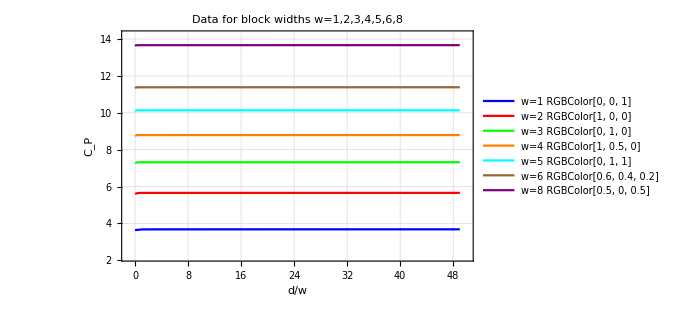

```mathematica
Show[ListPlot[{CoPCircleListN100dA1,CoPCircleListN200dA2,CoPCircleListN300dA3,CoPCircleListN400dA4,CoPCircleListN500dA5,CoPCircleListN600dA6,CoPCircleListN800dA8},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->{{-1,50},{2.2,14.2}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8"}]]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleTotal.pdf",%836,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleTotal.pdf

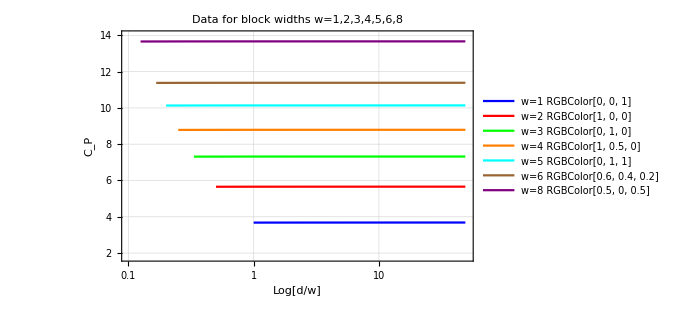

```mathematica
Show[ListLogLinearPlot[{CoPCircleListN100dA1,CoPCircleListN200dA2,CoPCircleListN300dA3,CoPCircleListN400dA4,CoPCircleListN500dA5,CoPCircleListN600dA6,CoPCircleListN800dA8},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->{{0.1,50},{1.8,14}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8"}]]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleLogLog.pdf",%829,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleLogLog.pdf

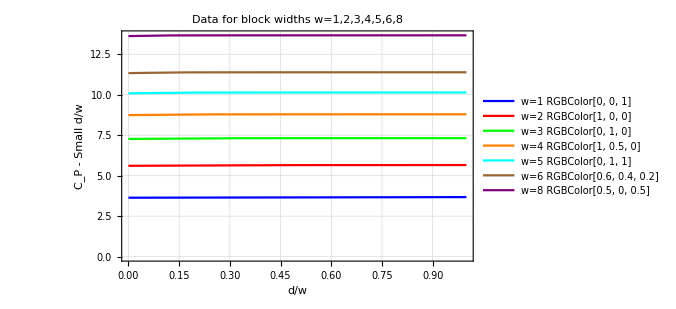

```mathematica
Show[ListPlot[{CoPCircleListN100dA1⟦1;;2⟧,CoPCircleListN200dA2⟦1;;3⟧,CoPCircleListN300dA3⟦1;;4⟧,CoPCircleListN400dA4⟦1;;5⟧,CoPCircleListN500dA5⟦1;;6⟧,CoPCircleListN600dA6⟦1;;7⟧,CoPCircleListN800dA8⟦1;;9⟧},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P - Small d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8"}]]
```

```mathematica
Show[ListPlot[{CoPCircleListN100dA1⟦1;;2⟧,CoPCircleListN200dA2⟦1;;3⟧,CoPCircleListN300dA3⟦1;;4⟧,CoPCircleListN400dA4⟦1;;5⟧,CoPCircleListN500dA5⟦1;;6⟧,CoPCircleListN600dA6⟦1;;7⟧,CoPCircleListN800dA8⟦1;;9⟧},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P - Small d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8"}]]
```

-Graphics-

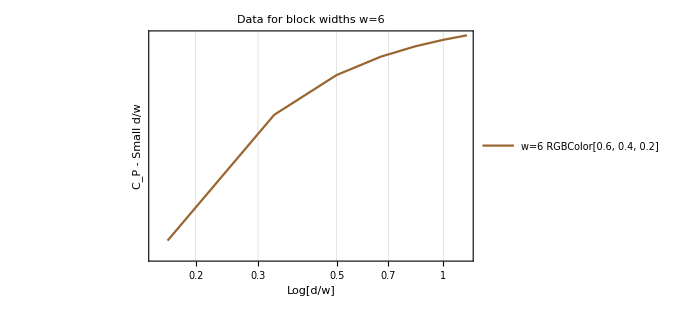

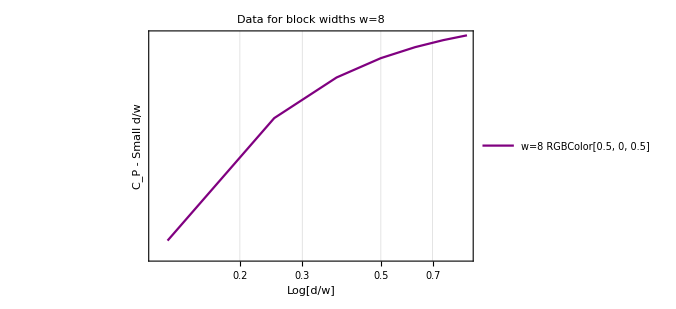

```mathematica
ListLogLogPlot[CoPCircleListN600dA6⟦1;;8⟧,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P - Small d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=6",PlotLegends->{Brown"w=6"}]
ListLogLogPlot[CoPCircleListN800dA8⟦1;;8⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P - Small d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=8",PlotLegends->{Purple"w=8"}]
```

```mathematica
(*Following: rescaled values*)
```

```mathematica
Last[CoPCircleListN100dA1]⟦2⟧
Last[CoPCircleListN200dA2]⟦2⟧
Last[CoPCircleListN300dA3]⟦2⟧
Last[CoPCircleListN400dA4]⟦2⟧
Last[CoPCircleListN500dA5]⟦2⟧
Last[CoPCircleListN600dA6]⟦2⟧
Last[CoPCircleListN800dA8]⟦2⟧
```

3.68245

5.6593

7.32004

8.79297

10.1369

11.3845

13.667

```mathematica
SubtractCoPCirclewA1=Sqrt[2]CoPVal[100,1/100,1/100,1,1,0,0]
```

3.76015

```mathematica
SubtractCoPCirclewA2=Sqrt[2]CoPVal[200,1/200,1/100,1,2,0,0]
```

5.71224

```mathematica
SubtractCoPCirclewA3=Sqrt[2]CoPVal[300,1/300,1/100,1,3,0,0]
```

7.36173

```mathematica
SubtractCoPCirclewA4=Sqrt[2]CoPVal[400,1/400,1/100,1,4,0,0]
```

8.82803

```mathematica
SubtractCoPCirclewA5=Sqrt[2]CoPVal[500,1/500,1/100,1,5,0,0]
```

10.1675

```mathematica
SubtractCoPCirclewA6=Sqrt[2]CoPVal[600,1/600,1/100,1,6,0,0]
```

11.4119

```mathematica
SubtractCoPCirclewA8=Sqrt[2]CoPVal[800,1/800,1/100,1,8,0,0]
```

13.69

```mathematica
NormCoPCirclew1={#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA1}&/@CoPCircleListN100dA1;
```

```mathematica
NormCoPCirclew2={#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA2}&/@CoPCircleListN200dA2;
```

```mathematica
NormCoPCirclew3={#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA3}&/@CoPCircleListN300dA3;
```

```mathematica
NormCoPCirclew4={#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA4}&/@CoPCircleListN400dA4;
```

```mathematica
NormCoPCirclew5={#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA5}&/@CoPCircleListN500dA5;
```

```mathematica
NormCoPCirclew6={#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA6}&/@CoPCircleListN600dA6;
```

```mathematica
NormCoPCirclew8={#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA8}&/@CoPCircleListN800dA8;
```

```mathematica
{#⟦1⟧,#⟦2⟧-SubtractCoPCirclewA1}&/@CoPCircleListN100dA1
```

{{0,-0.119832},{1,-0.0825212},{2,-0.0804222},{3,-0.0797771},{4,-0.0794381},{5,-0.079213},{6,-0.0790447},{7,-0.07891},{8,-0.0787977},{9,-0.0787013},{10,-0.0786169},{11,-0.078542},{12,-0.0784746},{13,-0.0784136},{14,-0.0783579},{15,-0.0783068},{16,-0.0782597},{17,-0.078216},{18,-0.0781755},{19,-0.0781378},{20,-0.0781027},{21,-0.0780698},{22,-0.0780391},{23,-0.0780104},{24,-0.0779834},{25,-0.0779581},{26,-0.0779345},{27,-0.0779123},{28,-0.0778915},{29,-0.077872},{30,-0.0778538},{31,-0.0778369},{32,-0.077821},{33,-0.0778063},{34,-0.0777927},{35,-0.07778},{36,-0.0777684},{37,-0.0777578},{38,-0.077748},{39,-0.0777392},{40,-0.0777313},{41,-0.0777243},{42,-0.0777181},{43,-0.0777128},{44,-0.0777083},{45,-0.0777047},{46,-0.0777019},{47,-0.0776998},{48,-0.0776986},{49,-0.0776982}}

```mathematica
{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN100dA1]⟦2⟧}&/@CoPCircleListN100dA1
```

{{0,-0.0421342},{1,-0.004823},{2,-0.00272398},{3,-0.00207885},{4,-0.00173989},{5,-0.00151478},{6,-0.00134645},{7,-0.00121181},{8,-0.00109948},{9,-0.00100309},{10,-0.000918708},{11,-0.000843744},{12,-0.000776409},{13,-0.00071538},{14,-0.000659682},{15,-0.000608563},{16,-0.000561429},{17,-0.000517807},{18,-0.000477307},{19,-0.000439614},{20,-0.000404459},{21,-0.000371615},{22,-0.000340893},{23,-0.000312127},{24,-0.000285175},{25,-0.000259916},{26,-0.000236239},{27,-0.00021405},{28,-0.000193266},{29,-0.00017381},{30,-0.000155624},{31,-0.00013864},{32,-0.000122815},{33,-0.000108096},{34,-0.0000944435},{35,-0.0000818206},{36,-0.0000701941},{37,-0.0000595339},{38,-0.0000498151},{39,-0.0000410124},{40,-0.0000331068},{41,-0.0000260788},{42,-0.0000199129},{43,-0.0000145969},{44,-0.0000101172},{45,-6.46214×10^-6},{46,-3.63179×10^-6},{47,-1.61288×10^-6},{48,-4.03074×10^-7},{49,0.}}

```mathematica
SaturationGrowthList= {{5,Last[CoPCircleListN600dA6]⟦2⟧-Last[CoPCircleListN500dA5]⟦2⟧},{4,Last[CoPCircleListN500dA5]⟦2⟧-Last[CoPCircleListN400dA4]⟦2⟧},
{3,Last[CoPCircleListN400dA4]⟦2⟧-Last[CoPCircleListN300dA3]⟦2⟧},{2,Last[CoPCircleListN300dA3]⟦2⟧-Last[CoPCircleListN200dA2]⟦2⟧},{1,Last[CoPCircleListN200dA2]⟦2⟧-Last[CoPCircleListN100dA1]⟦2⟧}};
```

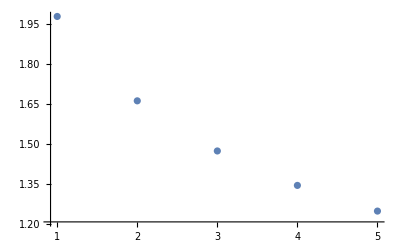

```mathematica
ListPlot[SaturationGrowthList]
```

```mathematica
Normal[NonlinearModelFit[SaturationGrowthList,a Log[b x]+c,{a,b,c},x]]
```

2.13304-0.454565 Log[1.41372 x]

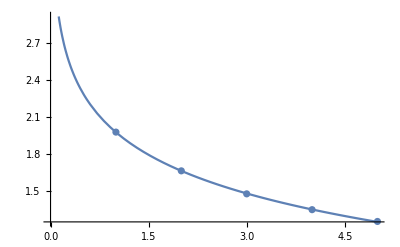

```mathematica
Show[Plot[2.133041590013013-0.45456497717458066 Log[1.413721781635795 x],{x,0,5}],ListPlot[SaturationGrowthList]]
```

```mathematica
2.133041590013013-0.45456497717458066 Log[1.413721781635795 x]/.x-> 77
```

0.00111766

```mathematica
Reduce[2.133041590013013-0.45456497717458066 Log[1.413721781635795 x]==0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x==77.1896

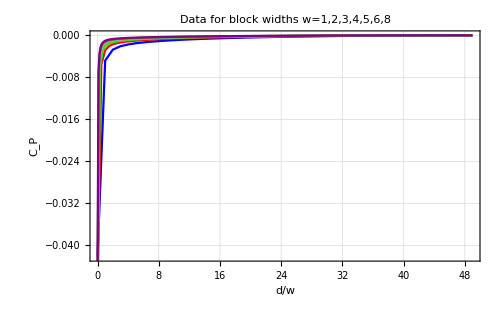

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN100dA1]⟦2⟧}&/@CoPCircleListN100dA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN200dA2]⟦2⟧}&/@CoPCircleListN200dA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN300dA3]⟦2⟧}&/@CoPCircleListN300dA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN400dA4]⟦2⟧}&/@CoPCircleListN400dA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN500dA5]⟦2⟧}&/@CoPCircleListN500dA5,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN600dA6]⟦2⟧}&/@CoPCircleListN600dA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN800dA8]⟦2⟧}&/@CoPCircleListN800dA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircle.pdf",%809,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircle.pdf

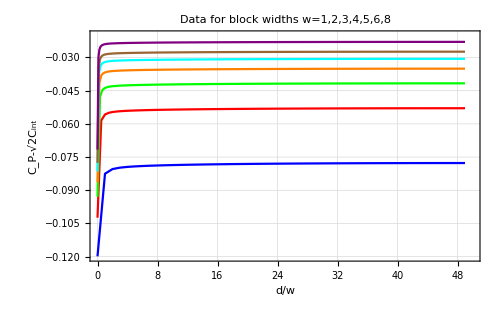

```mathematica
Show[ListPlot[NormCoPCirclew1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->{{0,50},{-0.12,-0.02}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->Blue"w=1"],ListPlot[NormCoPCirclew2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->{{0,50},{-0.12,-0.02}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[NormCoPCirclew3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->{{0,50},{-0.12,-0.02}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[NormCoPCirclew4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->{{0,50},{-0.12,-0.02}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[NormCoPCirclew5,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->{{0,50},{-0.12,-0.02}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListPlot[NormCoPCirclew6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->{{0,50},{-0.12,-0.02}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[NormCoPCirclew8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->{{0,50},{-0.12,-0.02}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleSubtrInterv.pdf",%878,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleSubtrInterv.pdf

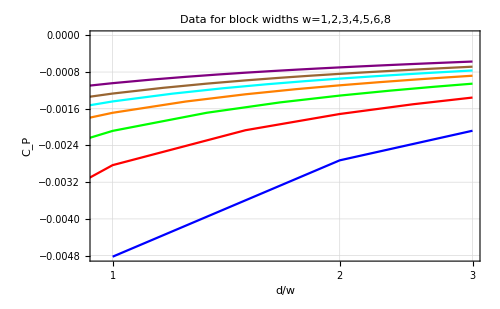

```mathematica
Show[ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN100dA1]⟦2⟧}&/@CoPCircleListN100dA1)⟦1;;4⟧,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->Blue"w=1"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN200dA2]⟦2⟧}&/@CoPCircleListN200dA2)⟦1;;7⟧,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN300dA3]⟦2⟧}&/@CoPCircleListN300dA3)⟦1;;10⟧,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN400dA4]⟦2⟧}&/@CoPCircleListN400dA4)⟦1;;13⟧,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN500dA5]⟦2⟧}&/@CoPCircleListN500dA5)⟦1;;16⟧,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN600dA6]⟦2⟧}&/@CoPCircleListN600dA6)⟦1;;19⟧,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN800dA8]⟦2⟧}&/@CoPCircleListN800dA8)⟦1;;25⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

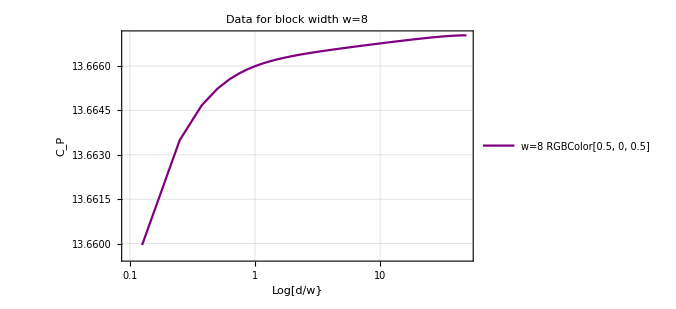

```mathematica
ListLogLinearPlot[CoPCircleListN800dA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w}", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block width w=8",PlotLegends->{Purple"w=8"}]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleLogLogw8.pdf",%838,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPCircleLogLogw8.pdf

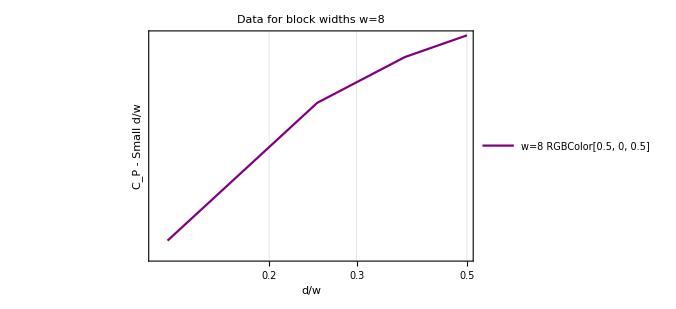

```mathematica
ListLogLogPlot[CoPCircleListN800dA8⟦1;;5⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P - Small d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=8",PlotLegends->{Purple"w=8"}]
```

```mathematica
Normal[NonlinearModelFit[CoPCircleListN800dA8⟦1;;5⟧,a Exp[b x],{a,b},x]]
```

13.6347 ⅇ^(0.00576483 x)

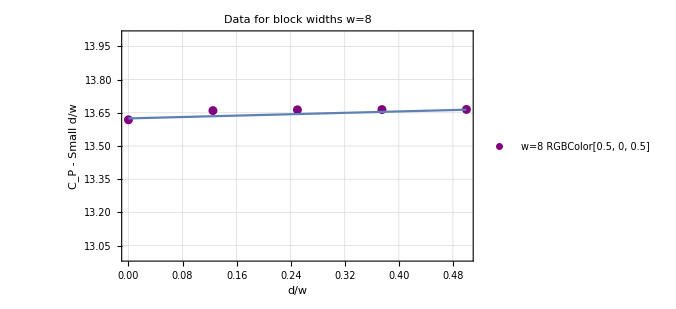

```mathematica
Show[ListPlot[CoPCircleListN800dA8⟦1;;5⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->False,PlotRange->{{0.0,0.5},{13,14}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P - Small d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=8",PlotLegends->{Purple"w=8"}],Plot[13.634674013932683 ⅇ^(0.005764826562882229 x)-0.01,{x,0,0.5},PlotRange->All]]
```

```mathematica
NonlinearModelFit[CoPCircleListN800dA8⟦1;;8⟧,a Exp[b x],{a,b,c},x]
```

FittedModel[13.6433 ⅇ^(0.00256755 x)]

```mathematica
NonlinearModelFit[CoPCircleListN800dA8⟦1;;10⟧,a Exp[b x],{a,b,c},x]
```

FittedModel[13.6468 ⅇ^(0.0017284 x)]

```mathematica
Normal[(NonlinearModelFit[CoPCircleListN800dA8⟦1;;10⟧,a Exp[b x],{a,b,c},x])]
```

13.6468 ⅇ^(0.0017284 x)

```mathematica
NonlinearModelFit[CoPCircleListN800dA8⟦1;;3⟧,b+a Exp[x],{a,b},x]
```

FittedModel[13.4697+0.155901 ⅇ^x]

```mathematica
NonlinearModelFit[CoPCircleListN800dA8⟦1;;5⟧,b+a Exp[x],{a,b},x]
```

FittedModel[13.5796+0.0573123 ⅇ^x]

```mathematica
NonlinearModelFit[CoPCircleListN800dA8⟦1;;10⟧,b+a Exp[x],{a,b},x]
```

FittedModel[13.6396+0.0109523 ⅇ^x]

```mathematica
Normal[LinearModelFit[CoPCircleListN800dA8⟦100;;393⟧,x,x]]
```

13.6668+5.66361×10^-6 x

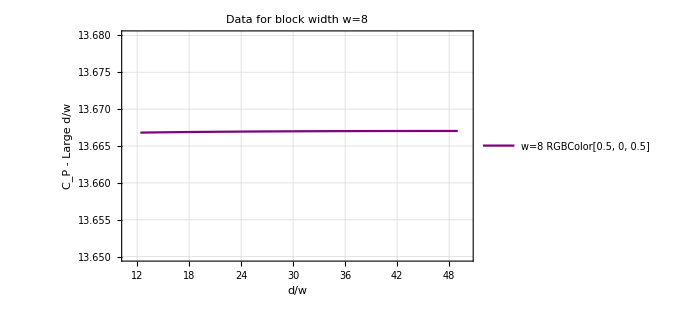

```mathematica
ListPlot[CoPCircleListN800dA8⟦100;;393⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->{{11,50},{13.65,13.68}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P - Large d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block width w=8",PlotLegends->{Purple"w=8"}]
```

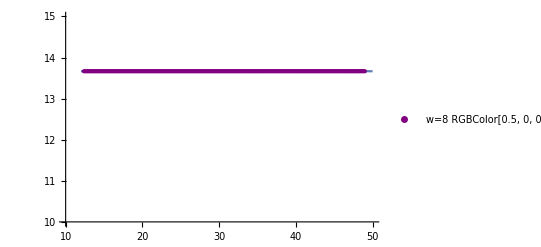

```mathematica
Show[Plot[13.666800081926931+5.663605671512033*^-6 x,{x,12,50},PlotRange->{{10,50},{10,15}}],ListPlot[CoPCircleListN800dA8⟦100;;393⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->False,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P - Small d/w"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=8",PlotLegends->{Purple"w=8"}]]
```

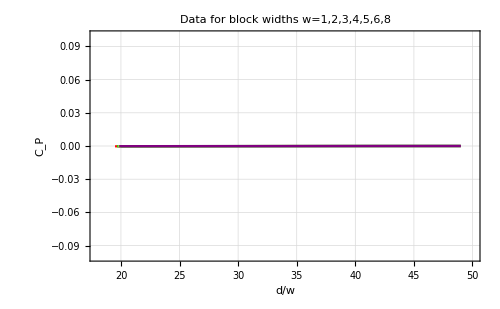

```mathematica
Show[ListPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN100dA1]⟦2⟧}&/@CoPCircleListN100dA1)⟦21;;50⟧,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->{{18,50},{-0.1,0.1}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->Blue"w=1"],ListPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN200dA2]⟦2⟧}&/@CoPCircleListN200dA2)⟦40;;99⟧,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN300dA3]⟦2⟧}&/@CoPCircleListN300dA3)⟦60;;148⟧,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN400dA4]⟦2⟧}&/@CoPCircleListN400dA4)⟦80;;197⟧,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN500dA5]⟦2⟧}&/@CoPCircleListN500dA5)⟦100;;246⟧,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN600dA6]⟦2⟧}&/@CoPCircleListN600dA6)⟦120;;295⟧,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN800dA8]⟦2⟧}&/@CoPCircleListN800dA8)⟦160;;393⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

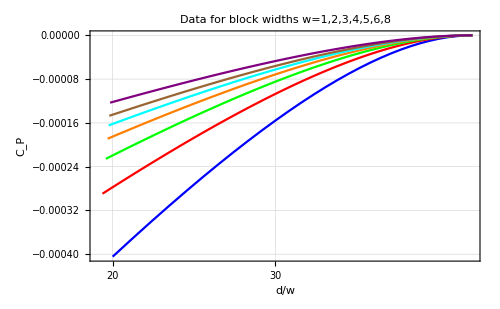

```mathematica
Show[ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN100dA1]⟦2⟧}&/@CoPCircleListN100dA1)⟦21;;50⟧,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->Blue"w=1"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN200dA2]⟦2⟧}&/@CoPCircleListN200dA2)⟦40;;99⟧,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN300dA3]⟦2⟧}&/@CoPCircleListN300dA3)⟦60;;148⟧,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN400dA4]⟦2⟧}&/@CoPCircleListN400dA4)⟦80;;197⟧,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN500dA5]⟦2⟧}&/@CoPCircleListN500dA5)⟦100;;246⟧,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN600dA6]⟦2⟧}&/@CoPCircleListN600dA6)⟦120;;295⟧,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Last[CoPCircleListN800dA8]⟦2⟧}&/@CoPCircleListN800dA8)⟦160;;393⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

## EoP

### Data

```mathematica
(*EoPCircleListN100dA1=Table[{d,EoPVal[100,1/100,1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
EoPCircleListN100dA1={{0,2.601309844110637},{1,2.5335967841594833},{2,2.432702465870051},{3,2.3680368268777556},{4,2.3225378011274316},{5,2.2882023771333486},{6,2.261016502285747},{7,2.238742228381954},{8,2.2200235303207863},{9,2.203984495315874},{10,2.190030302510393},{11,2.1777405228041995},{12,2.1668081249414812},{13,2.157002729501049},{14,2.1481474793681676},{15,2.140103935813631},{16,2.132761899673244},{17,2.126032360634621},{18,2.1198424990245384},{19,2.114132064592227},{20,2.1088507071960985},{21,2.1039559733740054},{22,2.099411783449872},{23,2.0951872555554845},{24,2.0912557876804825},{25,2.087594335300933},{26,2.084182831333538},{27,2.081003725145627},{28,2.0780416034040385},{29,2.0752828831576724},{30,2.0727155588782935},{31,2.0703289899575967},{32,2.068113731210611},{33,2.0660613807827892},{34,2.0641644588592367},{35,2.0624163062110457},{36,2.060810991846105},{37,2.0593432402263443},{38,2.058008367175468},{39,2.0568022249841755},{40,2.0557211562881434},{41,2.05476195418378},{42,2.053921828767759},{43,2.053198378565475},{44,2.052589566814671},{45,2.0520937012863},{46,2.051709418665316},{47,2.0514356712363586},{48,2.051271717429698},{49,2.0512171152430363}};
```

```mathematica
(*EoPCircleListN200dA2=Table[{d/2,EoPVal[200,1/200,1/100,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
EoPCircleListN200dA2={{0,2.7118727184043308},{1/2,2.696325073017671},{1,2.5609386406670978},{3/2,2.492096535842552},{2,2.4435747650838113},{5/2,2.4064592961841282},{3,2.376660927438671},{7/2,2.351937142582173},{4,2.3309249188701227},{9/2,2.31273561253075},{5,2.2967591079789456},{11/2,2.2825594559502247},{6,2.269815019495497},{13/2,2.2582823169518007},{7,2.247772454838976},{15/2,2.2381368628814253},{8,2.2292562236513946},{17/2,2.221033651819922},{9,2.213389133361358},{19/2,2.2062564109286407},{10,2.199579717545969},{21/2,2.193311521785551},{11,2.1874117938437534},{23/2,2.181845165023451},{12,2.1765821010795716},{25/2,2.1715958760936056},{13,2.166863586182476},{27/2,2.1623650714056564},{14,2.15808230926163},{29/2,2.153999381026874},{15,2.150102140604107},{31/2,2.1463774558808417},{16,2.1428144042240245},{33/2,2.1394021315183416},{17,2.1361316090967715},{35/2,2.132994164883092},{18,2.1299823000343707},{37/2,2.1270885331181253},{19,2.1243068163802956},{39/2,2.121631134738695},{20,2.1190560746538933},{41/2,2.116576487620569},{21,2.114187971840058},{43/2,2.11188608565131},{22,2.109667012223128},{45/2,2.1075271318443747},{23,2.1054629441204584},{47/2,2.103471318274753},{24,2.101549378538708},{49/2,2.0996943492267777},{25,2.0979036732043883},{51/2,2.096175000643183},{26,2.0945060822199375},{53/2,2.0928947344835755},{27,2.091339101481908},{55/2,2.0898373678953197},{28,2.08838777566694},{57/2,2.0869886451318944},{29,2.085638549205723},{59/2,2.0843360026055775},{30,2.083079569005137},{61/2,2.0818681156677696},{31,2.08070038578645},{63/2,2.079575272112163},{32,2.0784916379079856},{65/2,2.077448552133578},{33,2.076445034297498},{67/2,2.075480206622052},{34,2.074553173304254},{69/2,2.0736631808207524},{35,2.0728094739685394},{71/2,2.0719913217375496},{36,2.0712080687701313},{73/2,2.0704590745094364},{37,2.0697437484138597},{75/2,2.0690615216939907},{38,2.0684118676257484},{77/2,2.0677942896732606},{39,2.067208331151782},{79/2,2.066653536528244},{40,2.066129514666411},{81/2,2.065635879410883},{41,2.0651722457690234},{83/2,2.0647383241601838},{42,2.0643337678391287},{85/2,2.0639583125641283},{43,2.0636116994280322},{87/2,2.0632936683049006},{44,2.0630040249285977},{89/2,2.062742545569451},{45,2.0625090662550924},{91/2,2.0623034146049233},{46,2.0621254699400953},{93/2,2.061975098926632},{47,2.0618522051450108},{95/2,2.061756715952724},{48,2.0616885497023767},{97/2,2.061647665652065},{49,2.0616340385777887}};
```

```mathematica
(*EoPCircleListN300dA3=Table[{d/3,EoPVal[300,1/300,1/100,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
EoPCircleListN300dA3={{0,2.777461316383205},{1/3,2.776481122128188},{2/3,2.632446698751207},{1,2.5622322484811804},{4/3,2.5127905835683544},{5/3,2.4747761350582214},{2,2.444057433871211},{7/3,2.4184054886400586},{8/3,2.3964741066296753},{3,2.377386377593137},{10/3,2.3605390163077455},{11/3,2.3454993648346005},{4,2.331946787653998},{13/3,2.3196372946157524},{14/3,2.3083810939029528},{5,2.298027775091227},{16/3,2.288456188547444},{17/3,2.2795675158071678},{6,2.2712800596010405},{19/3,2.2635255950118625},{20/3,2.256246600797895},{7,2.249394131966704},{22/3,2.242926183941},{23/3,2.2368067739545188},{8,2.23100435501995},{25/3,2.2254915354712175},{26/3,2.220244057084632},{9,2.215240863747396},{28/3,2.2104630510640275},{29/3,2.205893453947218},{10,2.2015173989050276},{31/3,2.197321288156536},{32/3,2.193293109248347},{11,2.1894217077273623},{34/3,2.1856970936319984},{35/3,2.182110559309319},{12,2.1786533935663517},{37/3,2.1753184889659263},{38/3,2.172098693883857},{13,2.168987635319797},{40/3,2.1659797211871235},{41/3,2.1630695950914323},{14,2.160251890402166},{43/3,2.1575226115240262},{44/3,2.1548769439819058},{15,2.152311370404847},{46/3,2.14982193658751},{47/3,2.1474053088688114},{16,2.1450583448901006},{49/3,2.142777972373623},{50/3,2.1405616209323357},{17,2.1384062521662957},{52/3,2.1363097103879163},{53/3,2.1342696579634204},{18,2.132284052282691},{55/3,2.1303506757048107},{56/3,2.1284673707934134},{19,2.1266328312610803},{58/3,2.124845150919191},{59/3,2.123102473320004},{20,2.1214036098419204},{61/3,2.119746967903277},{62/3,2.1181311740493984},{21,2.1165548994200467},{64/3,2.115017006492761},{65/3,2.1135162494620774},{22,2.1120514333502793},{67/3,2.110621663931539},{68/3,2.109225900480786},{23,2.1078630765320803},{70/3,2.1065323676967043},{71/3,2.1052328675308605},{24,2.103963790991611},{73/3,2.102724229031288},{74/3,2.1015135578301587},{25,2.100330915952534},{76/3,2.0991757207018127},{77/3,2.0980473111536107},{26,2.09694497886227},{79/3,2.095868128205144},{80/3,2.0948162419132395},{27,2.093788751665316},{82/3,2.092784967648995},{83/3,2.091804573980924},{28,2.0908469840124555},{85/3,2.089911778861797},{86/3,2.088998446547398},{29,2.0881065634739566},{88/3,2.087235806630229},{89/3,2.086385614815144},{30,2.0855556400448148},{91/3,2.0847456118251593},{92/3,2.0839551339328426},{31,2.083183763626962},{94/3,2.0824313104356884},{95/3,2.0816973606737066},{32,2.0809816900792275},{97/3,2.080283935654882},{98/3,2.0796038273487056},{33,2.0789411163562637},{100/3,2.078295540840035},{101/3,2.0776668419082718},{34,2.0770547538328845},{103/3,2.076459101000956},{104/3,2.0758795946389843},{35,2.0753160437527947},{106/3,2.07476827109153},{107/3,2.074236024340787},{36,2.0737191618518653},{109/3,2.073217474890475},{110/3,2.0727307590951387},{37,2.0722588994939493},{112/3,2.071801701251902},{113/3,2.0713590172825844},{38,2.0709306849416826},{115/3,2.070516553171485},{116/3,2.070116514488949},{39,2.0697304019366713},{118/3,2.069358110164166},{119/3,2.0689995124083573},{40,2.0686544756449656},{121/3,2.0683229215280936},{122/3,2.0680047104167425},{41,2.0676997853306283},{124/3,2.067407972855972},{125/3,2.067129250416113},{42,2.066863505697861},{127/3,2.0666106535337443},{128/3,2.0663706199762375},{43,2.066143308155676},{130/3,2.0659287006608085},{131/3,2.0657266806712844},{44,2.06553722241543},{133/3,2.065360238381384},{134/3,2.0651957075595146},{45,2.0650435334282813},{136/3,2.064903722822649},{137/3,2.064776191997649},{46,2.064660934659398},{139/3,2.0645579007511685},{140/3,2.064467051070466},{47,2.064388381618912},{142/3,2.064321841721786},{143/3,2.0642674389865445},{48,2.0642251264979774},{145/3,2.064194929318387},{146/3,2.0641768129859206},{49,2.0641707732213437}};
```

### Plots

## Boson on a Line

## CoP

The function used in the Gaussian optimization for the line is CoPValLine[m,μ,dimA1,dimB1,d]  where:
m is the mass of the scalar field
(δ=1 is the fixed lattice spacing )
μ is the reference state frequency (assumed to be 1 in the following)
dimA1 is the number of sites in partition A1 of the subsystem
dimB1 is the number of sites in partition B1 of the subsystem
d is the lattice separation between the subsystem partitions A1 and B1
dimPur=dimA1+dimB1 is the dimension of the purification (assumed to be minimal)

In the following ‘w’ is also being used as the number of sites in the partitions A1 and B1 (assumed to be the same).

### Data {d/w,CoPValLine[ m/w , μ = 1 ,w, w, d]}. CoP[d/w] for a Line (RUN)

```mathematica
(*CoPLineListdwA1=Table[{d,CoPValLine[1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
CoPLineListdwA1={{0,0.9631715100009804},{1,1.0232567167517614},{2,1.0407370858645197},{3,1.0509106754016306},{4,1.0578798149422508},{5,1.0630583900299824},{6,1.0671052684158258},{7,1.0703792952553903},{8,1.0730962782451956},{9,1.0753953799139822},{10,1.077371145798552},{11,1.0790904765084792},{12,1.0806022844351402},{13,1.0819433051371654},{14,1.0831417573909967},{15,1.0842197370861546},{16,1.0851948336638875},{17,1.0860812518348377},{18,1.0868906086102308},{19,1.087632511549852},{20,1.0883149859535601},{21,1.0889447957203213},{22,1.0895276878347042},{23,1.0900685811849062},{24,1.0905717140486457},{25,1.091040760674961},{26,1.0914789242230085},{27,1.0918890116484234},{28,1.0922734944914925},{29,1.0926345585922834},{30,1.092974145116988},{31,1.0932939845448544},{32,1.0935956250761565},{33,1.0938804564882567},{34,1.0941497302726213},{35,1.094404576720265},{36,1.0946460195127694},{37,1.0948749881969644},{38,1.0950923289469918},{39,1.0952988138382649},{40,1.0954951489002827},{41,1.0956819811259115},{42,1.0958599045886528},{43,1.0960294658168623},{44,1.0961911684891281},{45,1.0963454776119874},{46,1.0964928231793105},{47,1.0966336034386772},{48,1.0967681877873703},{49,1.0968969193441447}};
```

```mathematica
(*CoPLineListdwA2=Table[{d/2,CoPValLine[1/200,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
CoPLineListdwA2={{0,1.25877382459582},{1/2,1.32203237940042},{1,1.343200088067181},{3/2,1.3563778362702419},{2,1.3658196437724075},{5/2,1.373074369159099},{3,1.3788968378308026},{7/2,1.3837133662901657},{4,1.3877880794562638},{9/2,1.391295557765518},{5,1.394356906671223},{11/2,1.397059361640467},{6,1.3994676947381692},{13/2,1.4016312157406796},{7,1.4035882591559623},{15/2,1.4053691650528044},{8,1.4069983201721408},{17/2,1.408495592181369},{9,1.4098773605460224},{19/2,1.4111572721408696},{10,1.4123468048980463},{21/2,1.4134556947722512},{11,1.4144922637722468},{23/2,1.4154636751028444},{12,1.4163761339859424},{25/2,1.4172350472261444},{13,1.418045151401336},{27/2,1.4188106165466003},{14,1.4195351309040443},{29/2,1.420221970504738},{15,1.4208740568730494},{31/2,1.421494005071904},{16,1.4220841640242357},{33/2,1.422646650469032},{17,1.4231833777796417},{35/2,1.4236960805129604},{18,1.4241863353723239},{37/2,1.4246555793069249},{19,1.425105125048898},{39/2,1.425536174655592},{20,1.4259498312200112},{41/2,1.426347109141996},{21,1.4267289431185806},{43/2,1.427096196002089},{22,1.4274496657767266},{45/2,1.4277900916956687},{23,1.4281181597228128},{47/2,1.4284345073852411},{24,1.4287397280734035},{49/2,1.4290343748948393},{25,1.4293189641186366},{51/2,1.4295939782827431},{26,1.4298598689432032},{53/2,1.430117059219616},{27,1.4303659460050622},{55/2,1.4306069020710535},{28,1.4308402778677984},{57/2,1.431066403235023},{29,1.431285588911425},{59/2,1.4314981279508576},{30,1.4317042969711828},{61/2,1.4319043573271368},{31,1.432098556165421},{63/2,1.4322871273924611},{32,1.4324702925850838},{65/2,1.4326482617907534},{33,1.4328212342928146},{67/2,1.4329893992932146},{34,1.4331529365756195},{69/2,1.4333120170688842},{35,1.4334668034242086},{71/2,1.4336174504862567},{36,1.4337641057964525},{73/2,1.4339069100029396},{37,1.4340459972707202},{75/2,1.4341814956619887},{38,1.4343135274940781},{77/2,1.4344422096261527},{39,1.4345676538107957},{79/2,1.434689966944735},{40,1.434809251342272},{81/2,1.4349256049782237},{41,1.4350391217212712},{83/2,1.4351498915519725},{42,1.4352580007554476},{85/2,1.435363532127909},{43,1.435466565135125},{87/2,1.4355671760813127},{44,1.4356654382831138},{89/2,1.435761422206962},{45,1.4358551955914813},{91/2,1.4359468236016624},{46,1.4360363689477955},{93/2,1.4361238919908803},{47,1.4362094508509406},{95/2,1.4362931015235492},{48,1.4363748979661606},{97/2,1.4364548922056464},{49,1.4365331344054342}};
```

```mathematica
(*CoPLineListdwA3=Table[{d/3,CoPValLine[1/300,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
CoPLineListdwA3={{0,1.470479047624168},{1/3,1.530870819854942},{2/3,1.5525486093231755},{1,1.5665699098219046},{4/3,1.576888290460943},{5/3,1.5849791789706253},{2,1.5915788318062394},{7/3,1.5971119321040144},{8/3,1.6018464744835688},{3,1.605962453282398},{10/3,1.6095864857098827},{11/3,1.6128109030923887},{4,1.6157050086687044},{13/3,1.6183220732856525},{14/3,1.6207038703156833},{5,1.622883719960946},{16/3,1.6248885938529247},{17/3,1.626740607151144},{6,1.6284580996604447},{19/3,1.6300564342958483},{20/3,1.6315485968670118},{7,1.6329456533224156},{22/3,1.634257103232004},{23/3,1.635491156202842},{8,1.6366549506209613},{25/3,1.6377547283340517},{26/3,1.6387959755706707},{9,1.6397835375267062},{28/3,1.6407217122457658},{29/3,1.641614328178664},{10,1.6424648085939657},{31/3,1.6432762254868571},{32/3,1.644051344907197},{11,1.6447926652795501},{34/3,1.6455024500530866},{35/3,1.646182755508053},{12,1.646835454674409},{37/3,1.6474622579075935},{38/3,1.6480647307514857},{13,1.6486443093813723},{40/3,1.6492023141164232},{41/3,1.64973996122161},{14,1.650258373286698},{43/3,1.6507585883237978},{44/3,1.6512415678406842},{15,1.65170820396064},{46/3,1.6521593257750689},{47/3,1.652595704962564},{16,1.6530180608151224},{49/3,1.6534270647794573},{50/3,1.6538233444407349},{17,1.6542074871739116},{52/3,1.6545800434101543},{53/3,1.6549415295714511},{18,1.6552924307412091},{55/3,1.655633203057431},{56/3,1.6559642759340418},{19,1.656286054012509},{58/3,1.6565989189908779},{59/3,1.6569032312707486},{20,1.6571993314632805},{61/3,1.65748754175869},{62/3,1.657768167208942},{21,1.6580414968630304},{64/3,1.6583078048468458},{65/3,1.6585673513306078},{22,1.658820383425507},{67/3,1.6590671360422338},{68/3,1.6593078326204023},{23,1.6595426858591606},{70/3,1.659771898366039},{71/3,1.6599956632649937},{24,1.6602141647604962},{73/3,1.6604275786479337},{74/3,1.6606360728372984},{25,1.660839807747173},{76/3,1.661038936771786},{77/3,1.661233606655617},{26,1.6614239578559828},{79/3,1.6616101248906192},{80/3,1.6617922366467044},{27,1.6619704166945},{82/3,1.6621447835530216},{83/3,1.6623154509583515},{28,1.6624825280994475},{85/3,1.6626461198552247},{86/3,1.6628063270185591},{29,1.6629632464807904},{88/3,1.6631169714335143},{89/3,1.663267591533971},{30,1.6634151931105963},{91/3,1.6635598592642462},{92/3,1.6637016700786589},{31,1.6638407027076838},{94/3,1.6639770315529963},{95/3,1.6641107283627259},{32,1.6642418622994322},{97/3,1.6643704911298378},{98/3,1.6644966874596825},{33,1.6646205154870806},{100/3,1.6647420529283363},{101/3,1.6648613404486512},{34,1.664978432400955},{103/3,1.6650933748501113},{104/3,1.665206229619512},{35,1.66531704760053},{106/3,1.6654258780595057},{107/3,1.6655327686793264},{36,1.6656377656500945},{109/3,1.6657409137126193},{110/3,1.6658422562209674},{37,1.6659418351980024},{112/3,1.6660396913795452},{113/3,1.6661358642666557},{38,1.6662303921877912},{115/3,1.6663233123216459},{116/3,1.6664146607429884},{39,1.666504472487846},{118/3,1.6665927815570103},{119/3,1.666679620978987},{40,1.6667650228326825},{121/3,1.6668490182889395},{122/3,1.666931637637251},{41,1.6670129103241929},{124/3,1.6670928649705268},{125/3,1.667171529420339},{42,1.6672489307360518},{127/3,1.6673250952697325},{128/3,1.6674000486389131},{43,1.667473815797126},{130/3,1.6675464210082345},{131/3,1.6676178879191084},{44,1.6676882395414772},{133/3,1.6677574982993535},{134/3,1.667825686019577},{45,1.6678928239906243},{136/3,1.6679589329284785},{137/3,1.668024033052845},{46,1.6680881440607964},{139/3,1.6681512851438527},{140/3,1.668213475042143},{47,1.6682747320117552},{142/3,1.6683350738724028},{143/3,1.6683945179958402},{48,1.6684530813487617},{145/3,1.668510780478885},{146/3,1.6685676315439923},{49,1.6686236502988396}};
```

```mathematica
(*CoPLineListdwA4=Table[{d/4,CoPValLine[1/400,1,4,4,d]},{d,0,(400-(4+4))/2}]*)
```

```mathematica
CoPLineListdwA4={{0,1.6439218449204382},{1/4,1.70085619016674},{1/2,1.722170648686968},{3/4,1.736305185787502},{1,1.7468984326027903},{5/4,1.7553242206169468},{3/2,1.7622772548882224},{7/4,1.7681634619937021},{2,1.773242086756989},{9/4,1.7776891542673485},{5/2,1.7816297147940654},{11/4,1.7851557711959976},{3,1.7883369373210194},{13/4,1.7912271140165317},{7/2,1.7938688496748376},{15/4,1.796296288569556},{4,1.7985372229283483},{17/4,1.8006145570662333},{9/2,1.8025473746659246},{19/4,1.8043517313636444},{5,1.8060412533416794},{21/4,1.807627595936703},{11/2,1.8091207997574021},{23/4,1.8105295704889959},{6,1.8118615011610002},{25/4,1.8131232503820507},{13/2,1.8143206866863328},{27/4,1.8154590061893534},{7,1.8165428295191328},{29/4,1.817576281929098},{15/2,1.8185630601887879},{31/4,1.8195064886244756},{8,1.8204095664593105},{33/4,1.8212750078682627},{17/2,1.8221052761959642},{35/4,1.8229026132148056},{9,1.8236690643109938},{37/4,1.824406500206812},{19/2,1.8251166358640079},{39/4,1.825801046831669},{10,1.8264611836305285},{41/4,1.8270983843154434},{21/2,1.8277138854797603},{43/4,1.8283088320434528},{11,1.8288842858414855},{45/4,1.8294412332598677},{23/2,1.8299805920727263},{47/4,1.8305032174448361},{12,1.8310099073901502},{49/4,1.831501407580007},{25/2,1.8319784157506005},{51/4,1.8324415855637242},{13,1.8328915301691293},{53/4,1.8333288253998747},{27/2,1.8337540126335157},{55/4,1.8341676014336785},{14,1.8345700718954934},{57/4,1.8349618768523235},{29/2,1.8353434438118748},{59/4,1.8357151767733635},{15,1.8360774578496832},{61/4,1.8364306488017816},{31/2,1.8367750924005866},{63/4,1.837111113706069},{16,1.8374390212049256},{65/4,1.83775910792382},{33/2,1.8380716523886034},{67/4,1.8383769195349422},{17,1.8386751615766705},{69/4,1.8389666187520517},{35/2,1.8392515200773862},{71/4,1.8395300839757427},{18,1.839802518952848},{73/4,1.840069024122201},{37/2,1.8403297897608555},{75/4,1.840584997821674},{19,1.8408348223751974},{77/4,1.8410794300932616},{39/2,1.8413189804739256},{79/4,1.8415536265624897},{20,1.8417835149693815},{81/4,1.8420087863600336},{41/2,1.8422295757542404},{83/4,1.842446012773695},{21,1.8426582219620313},{85/4,1.8428663230016753},{43/2,1.8430704309789607},{87/4,1.8432706566010237},{22,1.8434671064001853},{89/4,1.8436598829483117},{45/2,1.843849085033882},{91/4,1.844034807843751},{23,1.8442171431216945},{93/4,1.844396179348515},{47/2,1.8445720018301552},{95/4,1.8447446873771147},{24,1.8449143202706835},{97/4,1.8450809779894481},{49/2,1.8452447355599975},{99/4,1.845405675286844},{25,1.8455638558229328},{101/4,1.8457193433428287},{51/2,1.8458722019186111},{103/4,1.8460224892732486},{26,1.8461702717984108},{105/4,1.8463156082375276},{53/2,1.8464585554684585},{107/4,1.8465991686157017},{27,1.8467375010743798},{109/4,1.846873604606689},{55/2,1.847007529392384},{111/4,1.8471393241042626},{28,1.8472690359335746},{113/4,1.8473967107028821},{57/2,1.8475223928525093},{115/4,1.8476461255453365},{29,1.8477679506863809},{117/4,1.8478879089769749},{59/2,1.8480060399396807},{119/4,1.8481223820155435},{30,1.8482369725256138},{121/4,1.8483498477836573},{61/2,1.8484610430821145},{123/4,1.8485705927432199},{31,1.848678530170963},{125/4,1.8487848878387672},{63/2,1.8488896973832805},{127/4,1.8489929895727746},{32,1.8490947943764138},{129/4,1.849195140966047},{65/2,1.849294057763404},{131/4,1.8493915724517507},{33,1.849487711998074},{133/4,1.8495825026914452},{67/2,1.849675970147455},{135/4,1.8497681393456848},{34,1.8498590346275146},{137/4,1.8499486797432112},{69/2,1.8500370978560328},{139/4,1.850124311562477},{35,1.8502103429075272},{141/4,1.850295213396319},{71/2,1.8503789440387683},{143/4,1.8504615553236523},{36,1.8505430672556027},{145/4,1.8506234993894044},{73/2,1.8507028708019333},{147/4,1.8507812001338761},{37,1.8508585055955264},{149/4,1.8509348049788525},{75/2,1.8510101156706393},{151/4,1.8510844546685623},{38,1.8511578385692864},{153/4,1.851230283622061},{77/2,1.8513018056934172},{155/4,1.851372420322568},{39,1.85144214268434},{157/4,1.8515109876386073},{79/2,1.851578969698889},{159/4,1.8516461030966007},{40,1.8517124017360513},{161/4,1.8517778792315578},{81/2,1.8518425489023271},{163/4,1.8519064237967156},{41,1.8519695166807044},{165/4,1.8520318400550453},{83/2,1.8520934061597512},{167/4,1.85215422699145},{42,1.8522143142859913},{169/4,1.8522736795520998},{85/2,1.8523323340503817},{171/4,1.8523902888308954},{43,1.85244755471171},{173/4,1.8525041422934072},{87/2,1.8525600619665832},{175/4,1.8526153239208438},{44,1.8526699381436678},{177/4,1.852723914419937},{89/2,1.8527772623512238},{179/4,1.8528299913555508},{45,1.852882110651981},{181/4,1.8529336293090959},{91/2,1.8529845561978366},{183/4,1.8530349000375785},{46,1.8530846693721252},{185/4,1.8531338725914437},{93/2,1.853182517920233},{187/4,1.8532306134395253},{47,1.853278167074207},{189/4,1.853325186605885},{95/2,1.853371679678114},{191/4,1.8534176537603748},{48,1.853463116244222},{193/4,1.8535080743470316},{97/2,1.85355253516792},{195/4,1.8535965056695263},{49,1.8536399927061564}};
```

```mathematica
(*CoPLineListdwA5=Table[{d/5,CoPValLine[1/500,1,5,5,d]},{d,0,(500-(5+5))/2}]*)
```

```mathematica
CoPLineListdwA5={{0,1.79445950998373},{1/5,1.848198577658517},{2/5,1.8688847414338838},{3/5,1.8828449817082857},{4/5,1.8934475116953093},{1,1.9019710626976227},{6/5,1.9090671797445729},{7/5,1.9151196755560937},{8/5,1.9203756391366247},{9/5,1.9250041205179647},{2,1.9291260696912897},{11/5,1.9328310599608467},{12/5,1.9361872799634483},{13/5,1.9392478240645252},{14/5,1.9420548218366416},{3,1.9446422439123234},{16/5,1.947037864287787},{17/5,1.9492646668947369},{18/5,1.951341875341014},{19/5,1.9532857210037893},{4,1.9551100253620404},{21/5,1.9568266478613403},{22/5,1.9584458349961598},{23/5,1.9599764955930599},{24/5,1.9614264200523193},{5,1.9628024569101876},{26/5,1.964110656082991},{27/5,1.9653563861018821},{28/5,1.966544430864725},{29/5,1.9676790698716122},{6,1.9687641453375628},{31/5,1.9698031186135663},{32/5,1.970799117863895},{33/5,1.9717549786138742},{34/5,1.9726732783589853},{7,1.9735563662819964},{36/5,1.9744063888356556},{37/5,1.9752253119121643},{38/5,1.9760149400722389},{39/5,1.9767769333277385},{8,1.977512821821623},{41/5,1.9782240187084528},{42/5,1.9789118315108072},{43/5,1.979577472109941},{44/5,1.9802220656797165},{9,1.9808466585011508},{46/5,1.9814522250366742},{47/5,1.9820396741688826},{48/5,1.982609854814533},{49/5,1.9831635609490488},{10,1.9837015361345023},{51/5,1.9842244775795048},{52/5,1.984733039826665},{53/5,1.9852278380653066},{54/5,1.9857094511350402},{11,1.986178424283756},{56/5,1.986635271606907},{57/5,1.9870804783664326},{58/5,1.9875145030036958},{59/5,1.9879377790507544},{12,1.9883507168449224},{61/5,1.9887537051120312},{62/5,1.989147112408364},{63/5,1.989531288486017},{64/5,1.989906565454802},{13,1.9902732589878391},{66/5,1.9906316692964499},{67/5,1.99098208212981},{68/5,1.9913247696609544},{69/5,1.9916599912913624},{14,1.9919879944331287},{71/5,1.9923090151962886},{72/5,1.9926232790817864},{73/5,1.9929310015381718},{74/5,1.9932323885841177},{15,1.9935276372898447},{76/5,1.9938169363206906},{77/5,1.9941004663424913},{78/5,1.994378400502913},{79/5,1.9946509047763592},{16,1.9949181384134207},{81/5,1.9951802542099673},{82/5,1.995437398912813},{83/5,1.995689713461654},{84/5,1.9959373333360102},{17,1.9961803887914789},{86/5,1.9964190051307518},{87/5,1.996653302926385},{88/5,1.996883398274658},{89/5,1.9971094030006185},{18,1.997331424836967},{91/5,1.9975495676400106},{92/5,1.997763931529779},{93/5,1.9979746094545143},{94/5,1.9981816977388631},{19,1.9983852868072616},{96/5,1.9985854637959237},{97/5,1.9987823132155145},{98/5,1.9989759231977602},{99/5,1.9991663651949358},{20,1.9993537145568197},{101/5,1.999538044434519},{102/5,1.9997194253894224},{103/5,1.999897922909009},{104/5,2.000073607326913},{21,2.000246543081229},{106/5,2.0004167926043923},{107/5,2.000584416398494},{108/5,2.0007494731074256},{109/5,2.0009120195937258},{22,2.0010721110069847},{111/5,2.001229800849669},{112/5,2.0013851410409917},{113/5,2.0015381819637716},{114/5,2.0016889725515212},{23,2.00183756031231},{116/5,2.0019839913952433},{117/5,2.0021283106428687},{118/5,2.002270561615178},{119/5,2.002410786680083},{24,2.0025490270122153},{121/5,2.0026853226634205},{122/5,2.0028197125827134},{123/5,2.002952234657711},{124/5,2.003082925777719},{25,2.003211821834085},{126/5,2.0033389577625353},{127/5,2.00346436759045},{128/5,2.0035880844560103},{129/5,2.00371014062333},{26,2.0038305675481496},{131/5,2.003949395871445},{132/5,2.0040666554609654},{133/5,2.004182375424349},{134/5,2.004296584158571},{27,2.0044093093356286},{136/5,2.0045205779559},{137/5,2.004630416358166},{138/5,2.0047388502472314},{139/5,2.0048459046931173},{28,2.004951604178195},{141/5,2.0050559725892527},{142/5,2.0051590332595643},{143/5,2.0052608089608777},{144/5,2.005361321948325},{29,2.0054605939442247},{146/5,2.005558646188436},{147/5,2.0056554994118563},{148/5,2.0057511738968654},{149/5,2.0058456894529044},{30,2.0059390654474094},{151/5,2.0060313208110268},{152/5,2.0061224740677868},{153/5,2.0062125433117775},{154/5,2.006301546263559},{31,2.0063895002394863},{156/5,2.0064764221837286},{157/5,2.0065623286885743},{158/5,2.0066472359805},{159/5,2.006731159936524},{32,2.0068141161041475},{161/5,2.0068961197103756},{162/5,2.0069771856490637},{163/5,2.0070573285101405},{164/5,2.0071365625917945},{33,2.0072149018825733},{166/5,2.007292360104612},{167/5,2.0073689506629786},{168/5,2.0074446867450693},{169/5,2.007519581239963},{34,2.0075936467787763},{171/5,2.0076668957512473},{172/5,2.0077393402964945},{173/5,2.007810992320617},{174/5,2.0078818634962983},{35,2.0079519652558875},{176/5,2.008021308829566},{177/5,2.0080899052224246},{178/5,2.0081577652289346},{179/5,2.008224899432754},{36,2.008291318227129},{181/5,2.0083570318066286},{182/5,2.00842205016479},{183/5,2.0084863831197204},{184/5,2.0085500403085432},{37,2.0086130311756043},{186/5,2.0086753650086906},{187/5,2.008737050917988},{188/5,2.0087980978443176},{189/5,2.0088585145741233},{38,2.0089183097303325},{191/5,2.008977491781533},{192/5,2.009036069051664},{193/5,2.009094049705444},{194/5,2.009151441764818},{39,2.009208253123094},{196/5,2.009264491527884},{197/5,2.009320164577605},{198/5,2.0093752797686957},{199/5,2.0094298444452448},{40,2.0094838658258904},{201/5,2.00953735101986},{202/5,2.0095903069927545},{203/5,2.009642740624744},{204/5,2.009694658643862},{41,2.009746067688418},{206/5,2.00979697428135},{207/5,2.0098473848308056},{208/5,2.0098973056440053},{209/5,2.0099467429281908},{42,2.0099957027700444},{211/5,2.010044191179563},{212/5,2.0100922140548665},{213/5,2.0101397772063048},{214/5,2.0101868863381185},{43,2.0102335470776667},{216/5,2.0102797649499373},{217/5,2.0103255454017006},{218/5,2.010370893786649},{219/5,2.0104158153761507},{44,2.0104603153533858},{221/5,2.0105043988329294},{222/5,2.0105480708332077},{223/5,2.010591336303049},{224/5,2.010634200118031},{45,2.010676667073478},{226/5,2.0107187418922843},{227/5,2.0107604292221555},{228/5,2.010801733640547},{229/5,2.0108426596622997},{46,2.01088321172897},{231/5,2.0109233942053724},{232/5,2.0109632114075984},{233/5,2.0110026675823645},{234/5,2.0110417669024363},{47,2.0110805134904095},{236/5,2.0111189114059376},{237/5,2.01115696464129},{238/5,2.0111946771430755},{239/5,2.0112320527887575},{48,2.0112690954038297},{241/5,2.011305808762895},{242/5,2.011342196573792},{243/5,2.011378262492215},{244/5,2.011414010143684},{49,2.011449443072585}};
```

```mathematica
(*CoPLineListdwA6=Table[{d/6,CoPValLine[1/600,1,6,6,d]},{d,0,(600-(6+6))/2}]*)
```

```mathematica
CoPLineListdwA6={{0,1.9293664294667647},{1/6,1.9802932802314002},{1/3,2.0002867018469996},{1/2,2.0139548324673178},{2/3,2.0244407313802415},{5/6,2.0329405422188365},{1,2.0400663999699744},{7/6,2.04618077142042},{4/3,2.051518268987495},{3/2,2.0562402696798534},{5/3,2.0604628329217114},{11/6,2.0642723346090075},{2,2.0677348357826606},{13/6,2.0709019994884597},{7/3,2.073814987988678},{5/2,2.076507119714157},{8/3,2.079005733723231},{17/6,2.081333530545856},{3,2.083509557080484},{19/6,2.085549943501726},{10/3,2.0874684636739658},{7/2,2.089276967487997},{11/3,2.0909857187732905},{23/6,2.0926036624439392},{4,2.094138637977056},{25/6,2.0955975516143543},{13/3,2.0969865165118198},{9/2,2.0983109676844385},{14/3,2.099575757053999},{29/6,2.1007852324870706},{5,2.101943304027407},{31/6,2.1030534996732264},{16/3,2.104119012635556},{11/2,2.105142741554256},{17/3,2.106127324964082},{35/6,2.1070751708448747},{6,2.1079884821716424},{37/6,2.1088692790832564},{19/3,2.109719418095492},{13/2,2.1105406089610006},{20/3,2.111334429383443},{41/6,2.112102337971498},{7,2.112845685678517},{43/6,2.113565725859357},{22/3,2.1142636232998973},{15/2,2.114940462114887},{23/3,2.115597252878834},{47/6,2.1162349389815143},{8,2.116854402293948},{49/6,2.1174564682880814},{25/3,2.118041910619234},{17/2,2.1186114552736632},{26/3,2.1191657842933935},{53/6,2.1197055392019224},{9,2.1202313240250743},{55/6,2.1207437081128844},{28/3,2.121243228672867},{19/2,2.121730393067286},{29/3,2.12220568095486},{59/6,2.1226695461747735},{10,2.1231224185835154},{61/6,2.1235647055913764},{31/3,2.123996793745279},{21/2,2.124419050006316},{32/3,2.12483182308051},{65/6,2.1252354445509956},{11,2.1256302299299397},{67/6,2.1260164797064665},{34/3,2.1263944802093264},{23/2,2.126764504475537},{35/3,2.1271268130550345},{71/6,2.1274816547046904},{12,2.127829267105684},{73/6,2.1281698774698707},{37/3,2.1285037031350904},{25/2,2.12883095211622},{38/3,2.1291518236157434},{77/6,2.1294665084787723},{13,2.129775189691637},{79/6,2.1300780427406134},{40/3,2.1303752360412},{27/2,2.1306669312691486},{41/3,2.130953283736215},{83/6,2.131234442713426},{14,2.131510551680248},{85/6,2.1317817486876294},{43/3,2.132048166540029},{29/2,2.132309933127495},{44/3,2.1325671715898347},{89/6,2.1328200005947484},{15,2.133068534497156},{91/6,2.1333128810145894},{46/3,2.133553148690545},{31/2,2.1337894404398257},{47/3,2.1340218554811696},{95/6,2.1342504896443235},{16,2.13447543575318},{97/6,2.134696788006615},{49/3,2.134914627911072},{33/2,2.135129038621698},{50/3,2.1353401008103097},{101/6,2.135547892517558},{17,2.135752489119864},{103/6,2.135953961614277},{52/3,2.1361523836037017},{35/2,2.136347823835583},{53/3,2.136540348910991},{107/6,2.1367300233939313},{18,2.1369169098829888},{109/6,2.137101069099969},{55/3,2.137282559951833},{37/2,2.1374614395899534},{56/3,2.1376377634964254},{113/6,2.137811585549153},{19,2.1379829580463943},{115/6,2.138151931808671},{58/3,2.138318556212618},{39/2,2.1384828792238744},{59/3,2.1386449474989835},{119/6,2.138804806374256},{20,2.1389624999533554},{121/6,2.1391180711361795},{61/3,2.1392715616600024},{41/2,2.1394230121324824},{62/3,2.1395724620989665},{125/6,2.1397199500293307},{21,2.1398655134154856},{127/6,2.140009188750623},{64/3,2.14015101159684},{43/2,2.140291016586336},{65/3,2.14042923749071},{131/6,2.1405657072046824},{22,2.1407004578173794},{133/6,2.1408335206114444},{67/3,2.140964926077283},{45/2,2.1410947039791077},{68/3,2.141222883345171},{137/6,2.141349492498424},{23,2.141474559081651},{139/6,2.1415981100753667},{70/3,2.1417201718177594},{47/2,2.141840770027862},{71/3,2.141959929825333},{143/6,2.1420776757367364},{24,2.1421940317221284},{145/6,2.142309021203646},{73/3,2.142422667051706},{49/2,2.1425349916293093},{74/3,2.142646016785015},{149/6,2.1427557638931467},{25,2.1428642538420286},{151/6,2.1429715070546056},{76/3,2.1430775435126224},{51/2,2.143182382762245},{77/3,2.143286043928654},{155/6,2.1433885456920168},{26,2.1434899063817148},{157/6,2.1435901439065925},{79/3,2.143689275803511},{53/2,2.1437873192275885},{80/3,2.1438842909983418},{161/6,2.1439802075691228},{27,2.1440750850509995},{163/6,2.1441689392327445},{82/3,2.144261785574765},{55/2,2.1443536392266718},{83/3,2.1444445150267475},{167/6,2.1445344275161458},{28,2.144623390952569},{169/6,2.1447114192986105},{85/3,2.144798526248993},{57/2,2.1448847252260395},{86/3,2.14497002939049},{173/6,2.1450544516466548},{29,2.145138004649572},{175/6,2.1452207008090527},{88/3,2.1453025522980123},{59/2,2.145383571067234},{89/3,2.1454637688268217},{179/6,2.145543157061887},{30,2.1456217470670302},{181/6,2.1456995499070914},{91/3,2.1457765764484362},{61/2,2.1458528373418884},{92/3,2.145928343074526},{185/6,2.146003103910006},{31,2.146077129946235},{187/6,2.146150431087853},{94/3,2.14622301706444},{63/2,2.1462948974316025},{95/3,2.146366081575928},{191/6,2.1464365787138666},{32,2.146506397903833},{193/6,2.146575548042855},{97/3,2.146644037874997},{65/2,2.146711875985195},{98/3,2.1467790708166734},{197/6,2.1468456306726207},{33,2.1469115636932625},{199/6,2.1469768779044727},{100/3,2.1470415811870294},{67/2,2.1471056812707885},{101/3,2.147169185793098},{203/6,2.1472321022213463},{34,2.147294437930758},{205/6,2.1473562001612128},{103/3,2.1474173960323},{69/2,2.147478032548756},{104/3,2.1475381166000127},{209/6,2.1475976549653795},{35,2.147656654314014},{211/6,2.1477151211928205},{106/3,2.1477730620719595},{71/2,2.1478304832954622},{107/3,2.1478873911138603},{215/6,2.1479437916791433},{36,2.1479996910441854},{217/6,2.1480550951667943},{109/3,2.1481100099129624},{73/2,2.1481644410531304},{110/3,2.1482183942734325},{221/6,2.1482718751702707},{37,2.1483248892516333},{223/6,2.1483774419431896},{112/3,2.148429538589518},{75/2,2.148481184445034},{113/3,2.1485323846982505},{227/6,2.1485831444505195},{38,2.1486334687218247},{229/6,2.1486833624709645},{115/3,2.1487328305720066},{77/2,2.148781877829023},{116/3,2.148830508977539},{233/6,2.148878728682241},{39,2.1489265415360066},{235/6,2.1489739520707665},{118/3,2.1490209647451284},{79/2,2.1490675839596793},{119/3,2.1491138140478436},{239/6,2.149159659283515},{40,2.1492051238711536},{241/6,2.149250211968387},{121/3,2.1492949276627136},{81/2,2.149339274988618},{122/3,2.1493832579228087},{245/6,2.149426880391479},{41,2.149470146247875},{247/6,2.149513059311498},{124/3,2.149555623337288},{83/2,2.149597842041332},{125/3,2.1496397190680714},{251/6,2.1496812580259967},{42,2.149722462472138},{253/6,2.1497633359133466},{127/3,2.1498038818084604},{85/2,2.1498441035695404},{128/3,2.1498840045647913},{257/6,2.1499235881142913},{43,2.1499628574927176},{259/6,2.1500018159363194},{130/3,2.1500404666327793},{87/2,2.150078812728812},{131/3,2.1501168573299694},{263/6,2.1501546034961065},{44,2.1501920542615696},{265/6,2.1502292126069285},{133/3,2.1502660814752548},{89/2,2.150302663777564},{134/3,2.150338962382513},{269/6,2.1503749801217062},{45,2.150410719792862},{271/6,2.1504461841583886},{136/3,2.1504813759365113},{91/2,2.1505162978267878},{137/3,2.1505509524763107},{275/6,2.1505853425118335},{46,2.1506194705223125},{277/6,2.1506533390667513},{139/3,2.150686950672854},{93/2,2.150720307822744},{140/3,2.1507534129859036},{281/6,2.150786268593865},{47,2.150818877049662},{283/6,2.15085124071937},{142/3,2.15088336195673},{95/2,2.150915243056672},{143/3,2.1509468863278842},{287/6,2.1509782940056006},{48,2.1510094683368592},{289/6,2.1510404115196815},{145/3,2.151071125729251},{97/2,2.1511016131228473},{146/3,2.1511318758153544},{293/6,2.1511619159102033},{49,2.1511917354781365}};
```

```mathematica
(*CoPLineListdwA8=Table[{d/8,CoPValLine[1/800,1,8,8,d]},{d,0,(800-(8+8))/2}]*)
```

```mathematica
CoPLineListdwA8={{0,2.167166914597699},{1/8,2.213486454964676},{1/4,2.2321468127667994},{3/8,2.2451307457647958},{1/2,2.25523446794613},{5/8,2.2635231064719674},{3/4,2.2705438453171554},{7/8,2.2766224482613926},{1,2.281971083604344},{9/8,2.286736649581847},{5/4,2.291025495390044},{11/8,2.294917290011806},{3/2,2.2984733542953766},{13/8,2.3017419396445638},{7/4,2.3047617170157984},{15/8,2.307564164708711},{2,2.3101752505484505},{17/8,2.3126166466330336},{9/4,2.3149066252407993},{19/8,2.3170607320140424},{5/2,2.3190922999162495},{21/8,2.321012847417179},{11/4,2.3228323909193986},{23/8,2.3245596927289163},{3,2.3262024599906352},{25/8,2.3277675056999625},{13/4,2.3292608802691968},{27/8,2.330687979832264},{7/2,2.332053636025158},{29/8,2.333362190966721},{15/4,2.334617560291511},{31/8,2.3358232863205406},{4,2.336982583376671},{33/8,2.3380983763330154},{17/4,2.339173333811193},{35/8,2.3402098967387936},{9/2,2.3412103030522173},{37/8,2.3421766092159575},{19/4,2.3431107089332257},{39/8,2.3440143495762964},{5,2.3448891465740944},{41/8,2.3457365961129013},{21/4,2.346558086364914},{43/8,2.3473549074142777},{11/2,2.3481282600906526},{45/8,2.3488792638602223},{23/4,2.3496089638588726},{47/8,2.350318337157263},{6,2.351008298459848},{49/8,2.351679705142432},{25/4,2.3523333618855173},{51/8,2.352970024744669},{13/2,2.3535904049777034},{53/8,2.354195172374041},{27/4,2.354784958367791},{55/8,2.355360358841091},{7,2.355921936673599},{57/8,2.356470224084553},{29/4,2.357005724773915},{59/8,2.3575289158561272},{15/2,2.358040249657133},{61/8,2.3585401553871503},{31/4,2.3590290406154146},{63/8,2.3595072926747687},{8,2.359975279968431},{65/8,2.3604333531209303},{33/4,2.360881846099705},{67/8,2.361321077207359},{17/2,2.361751350037254},{69/8,2.362172954340615},{35/4,2.362586166820207},{71/8,2.3629912519007616},{9,2.3633884624041914},{73/8,2.3637780402342696},{37/4,2.3641602169391733},{75/8,2.364535214311369},{19/2,2.36490324489303},{77/8,2.3652645124861653},{39/4,2.3656192125960565},{79/8,2.3659675328817973},{10,2.366309653527142},{81/8,2.3666457476756637},{41/4,2.366975981727439},{83/8,2.3673005157041085},{21/2,2.367619503560951},{85/8,2.3679330934714207},{43/4,2.3682414281066975},{87/8,2.36854464349527},{11,2.368842873244972},{89/8,2.3691362451999898},{45/4,2.369424882560149},{91/8,2.369708904171169},{23/2,2.369988424739685},{93/8,2.3702635550433215},{47/4,2.370534402245261},{95/8,2.370801072339288},{12,2.3710636625321797},{97/8,2.371322269187778},{49/4,2.3715769856421622},{99/8,2.37182790223288},{25/2,2.372075106372755},{101/8,2.3723186826688942},{51/4,2.3725587129310237},{103/8,2.3727952753573534},{13,2.3730284483765485},{105/8,2.3732583065657535},{53/4,2.373484922246899},{107/8,2.373708365552402},{27/2,2.373928704498924},{109/8,2.3741460051067786},{55/4,2.374360331431178},{111/8,2.374571745681694},{14,2.3747803082556},{113/8,2.374986077810143},{57/4,2.37518911133825},{115/8,2.375389464236128},{29/2,2.375587190346474},{117/8,2.3757823420021227},{59/4,2.3759749701058226},{119/8,2.376165124174614},{15,2.376352852374864},{121/8,2.3765382015853724},{61/4,2.37672121741145},{123/8,2.3769019442874018},{31/2,2.377080425458393},{125/8,2.377256703033657},{63/4,2.3774308180548185},{127/8,2.377602810495002},{16,2.3777727193105425},{129/8,2.3779405824696696},{65/4,2.378106436994453},{131/8,2.378270318979076},{33/2,2.378432263618692},{133/8,2.3785923052525977},{67/4,2.3787504773678076},{135/8,2.378906812660889},{17,2.3790613430216587},{137/8,2.3792140995905497},{69/4,2.379365112753549},{139/8,2.379514412198291},{35/2,2.3796620269072206},{141/8,2.3798079851861167},{71/4,2.3799523146949744},{143/8,2.380095042452155},{18,2.3802361948573103},{145/8,2.380375797725457},{73/4,2.380513876278831},{147/8,2.3806504551732375},{37/2,2.380785558528133},{149/8,2.3809192099254446},{75/4,2.381051432424705},{151/8,2.381182248586543},{19,2.3813116804879164},{153/8,2.381439749721971},{77/4,2.38156647742963},{155/8,2.3816918842870547},{39/2,2.381815990545422},{157/8,2.3819388160332986},{79/4,2.3820603801580593},{159/8,2.3821807019146117},{20,2.382299799933274},{161/8,2.3824176924361344},{81/4,2.382534397288632},{163/8,2.3826499319845764},{41/2,2.382764313672429},{165/8,2.382877559155488},{83/4,2.3829896848945182},{167/8,2.3831007070363914},{21,2.383210641398264},{169/8,2.3833195035020975},{85/4,2.3834273085492943},{171/8,2.3835340714607547},{43/2,2.383639806867676},{173/8,2.38374452910826},{87/4,2.38384825226909},{175/8,2.383950990150752},{22,2.3840527563036895},{177/8,2.3841535640231464},{89/4,2.3842534263539488},{179/8,2.384352356098642},{45/2,2.384450365823929},{181/8,2.3845474678717884},{91/4,2.3846436743483412},{183/8,2.3847389971452704},{23,2.3848334479478},{185/8,2.384927038214732},{93/4,2.3850197792034},{187/8,2.385111681982687},{47/2,2.3852027574188726},{189/8,2.3852930161835952},{95/4,2.385382468750713},{191/8,2.385471125456053},{24,2.3855589963968797},{193/8,2.385646091533402},{97/4,2.385732420637532},{195/8,2.3858179933283923},{49/2,2.3859028190505662},{197/8,2.3859869070921063},{99/4,2.386070266592988},{199/8,2.386152906514306},{25,2.3862348356960847},{201/8,2.3863160628195543},{101/4,2.3863965964207425},{203/8,2.386476444899035},{51/2,2.386555616508202},{205/8,2.3866341193796803},{103/4,2.3867119615055543},{207/8,2.38678915074198},{26,2.3868656948354774},{209/8,2.386941601397865},{105/4,2.3870168779157437},{211/8,2.3870915317678647},{53/2,2.38716557020478},{213/8,2.3872390003794135},{107/4,2.3873118293048923},{215/8,2.38738406391499},{27,2.387455711022869},{217/8,2.387526777326807},{109/4,2.387597269440846},{219/8,2.3876671938676344},{55/2,2.3877365570047737},{221/8,2.38780536516217},{111/4,2.3878736245582823},{223/8,2.387941341297836},{28,2.388008521413666},{225/8,2.388075170841913},{113/4,2.388141295431762},{227/8,2.388206900943281},{57/2,2.3882719930470695},{229/8,2.3883365773393215},{115/4,2.3884006593320586},{231/8,2.3884642444548048},{29,2.388527338062413},{233/8,2.388589945419001},{117/4,2.388652071731842},{235/8,2.388713722120796},{59/2,2.3887749016374977},{237/8,2.388835615261491},{119/4,2.38889586789734},{239/8,2.388955664386644},{30,2.38901500949945},{241/8,2.3890739079430316},{121/4,2.389132364345722},{243/8,2.3891903832946246},{61/2,2.3892479692858903},{245/8,2.3893051267815073},{123/4,2.389361860156591},{247/8,2.389418173747008},{31,2.38947407181648},{249/8,2.389529558576758},{125/4,2.389584638181164},{251/8,2.3896393147281407},{63/2,2.3896935922589932},{253/8,2.3897474747534577},{127/4,2.389800966160148},{255/8,2.389854070349775},{32,2.3899067911587015},{257/8,2.3899591323708225},{129/4,2.3900110977120383},{259/8,2.3900626908679294},{65/2,2.390113915471731},{261/8,2.390164775107612},{131/4,2.3902152733207327},{263/8,2.3902654136055155},{33,2.390315199401614},{265/8,2.3903646341279647},{133/4,2.3904137211397614},{267/8,2.390462463762957},{67/2,2.390510865261986},{269/8,2.3905589288883693},{135/4,2.3906066578194913},{271/8,2.39065405522661},{34,2.390701124217216},{273/8,2.39074786786981},{137/4,2.3907942892250027},{275/8,2.3908403912809217},{69/2,2.390886176997108},{277/8,2.390931649309138},{139/4,2.390976811106034},{279/8,2.391021665246536},{35,2.391066214540692},{281/8,2.391110461788077},{141/4,2.391154409743368},{283/8,2.3911980611138715},{71/2,2.3912414185955355},{285/8,2.3912844848458077},{143/4,2.3913272624864548},{287/8,2.3913697541092587},{36,2.3914119622767243},{289/8,2.3914538895239756},{145/4,2.3914955383420353},{291/8,2.3915369112134646},{73/2,2.391578010575419},{293/8,2.391618838848288},{147/4,2.3916593984186894},{295/8,2.391699691642081},{37,2.3917397208541527},{297/8,2.3917794883508634},{149/4,2.3918189964205103},{299/8,2.391858247315755},{75/2,2.3918972432551713},{301/8,2.391935986452548},{151/4,2.391974479067887},{303/8,2.3920127232655624},{38,2.3920507211692805},{305/8,2.3920884748819176},{153/4,2.392125986481338},{307/8,2.3921632580319363},{77/2,2.3922002915599645},{309/8,2.3922370890795372},{155/4,2.3922736525830883},{311/8,2.392309984030452},{39,2.3923460853721563},{313/8,2.392381958530576},{157/4,2.392417605405265},{315/8,2.3924530278821328},{79/2,2.3924882278227124},{317/8,2.3925232070692246},{159/4,2.3925579674425657},{319/8,2.3925925107435613},{40,2.3926268387573737},{321/8,2.392660953239195},{161/4,2.3926948559491596},{323/8,2.392728548593262},{81/2,2.3927620328957535},{325/8,2.392795310536513},{163/4,2.3928283831947126},{327/8,2.3928612525159765},{41,2.3928939201410957},{329/8,2.3929263876961886},{165/4,2.392958656767747},{331/8,2.392990728954601},{83/2,2.393022605817721},{333/8,2.3930542889181075},{167/4,2.3930857797934535},{335/8,2.3931170799510557},{42,2.3931481909095007},{337/8,2.393179114158428},{169/4,2.3932098511627173},{339/8,2.3932404033911823},{85/2,2.393270772285394},{341/8,2.393300959276431},{171/4,2.393330965780052},{343/8,2.3933607931941827},{43,2.393390442911124},{345/8,2.393419916301378},{173/4,2.3934492147243644},{347/8,2.3934783395301458},{87/2,2.3935072920454417},{349/8,2.3935360735918807},{175/4,2.3935646854769295},{351/8,2.3935931289932038},{44,2.3936214054262126},{353/8,2.3936495160299143},{177/4,2.3936774620723},{355/8,2.3937052447951133},{89/2,2.3937328654260615},{357/8,2.393760325187801},{179/4,2.393787625284039},{359/8,2.393814766919091},{45,2.393841751259128},{361/8,2.3938685794928865},{181/4,2.3938952527818165},{363/8,2.3939217722645254},{91/2,2.3939481390907678},{365/8,2.3939743543852643},{183/4,2.3940004192601876},{367/8,2.3940263348304627},{46,2.3940521021905488},{369/8,2.394077722429257},{185/4,2.394103196615047},{371/8,2.39412852582491},{93/2,2.3941537111034576},{373/8,2.394178753497872},{187/4,2.3942036540547833},{375/8,2.394228413786761},{47,2.394253033721861},{377/8,2.3942775148648865},{189/4,2.3943018582083924},{379/8,2.394326064749579},{95/2,2.3943501354630685},{381/8,2.3943740713210886},{191/4,2.39439787328707},{383/8,2.394421542313237},{48,2.3944450793460335},{385/8,2.3944684853145506},{193/4,2.394491761159034},{387/8,2.3945149077833543},{97/2,2.3945379261080535},{389/8,2.3945608170362185},{195/4,2.3945835814571383},{391/8,2.394606220260928},{49,2.3946287343282995}};
```

```mathematica
(*CoPLineListdwA10=Table[{d/10,CoPValLine[1/1000,1,10,10,d]},{d,0,(1000-(10+10))/2}]*)
```

```mathematica
CoPLineListdwA10={{0,2.375607333883834},{1/10,2.4183416725750693},{1/5,2.4358362058326586},{3/10,2.448148247845545},{2/5,2.4578203383725263},{1/2,2.4658201509092827},{3/5,2.472645271989708},{7/10,2.4785925640747326},{4/5,2.483855928946667},{9/10,2.4885700692936394},{1,2.492832861385925},{11/10,2.4967179059608964},{6/5,2.5002820721969927},{13/10,2.503570281382458},{7/5,2.506618672854974},{3/2,2.5094567740446343},{8/5,2.5121090320735058},{17/10,2.514595921928192},{9/5,2.516934765553711},{19/10,2.519140348667224},{2,2.521225392826857},{21/10,2.5232009219640315},{11/5,2.5250765507042114},{23/10,2.52686071378019},{12/5,2.528560850438747},{5/2,2.5301835541865456},{13/5,2.531734695316488},{27/10,2.5332195220611027},{14/5,2.5346427446622197},{29/10,2.5360086057181226},{3,2.5373209394243554},{31/10,2.5385832217445246},{16/5,2.5397986131543924},{33/10,2.540969995156241},{17/5,2.542100001772122},{7/2,2.543191046658307},{18/5,2.544245346669782},{37/10,2.5452649423527176},{19/5,2.546251715852554},{39/10,2.5472074066634938},{4,2.5481336254008555},{41/10,2.549031866044132},{21/5,2.5499035166981816},{43/10,2.55074986922885},{22/5,2.5515721277800716},{9/2,2.5523714163602502},{23/5,2.553148785710266},{47/10,2.5539052193812535},{24/5,2.554641639242253},{49/10,2.555358910440778},{5,2.5560578458504555},{51/10,2.5567392101037147},{26/5,2.5574037232959954},{53/10,2.5580520642703495},{27/5,2.5586848736500953},{11/2,2.559302756599508},{28/5,2.5599062853351913},{57/10,2.560496001425016},{29/5,2.561072417877893},{59/10,2.561636021087476},{6,2.562187272588935},{61/10,2.5627266107045363},{31/5,2.5632544519990756},{63/10,2.563771192720593},{32/5,2.5642772100188034},{13/2,2.5647728631517444},{33/5,2.5652584945646137},{67/10,2.56573443089535},{34/5,2.566200983921821},{69/10,2.5666584514102384},{7,2.567107117941902},{71/10,2.567547255639299},{36/5,2.56797912487822},{73/10,2.5684029749546253},{37/5,2.5688190446368484},{15/2,2.5692275628062995},{38/5,2.5696287489132046},{77/10,2.5700228135296697},{39/5,2.5704099587724847},{79/10,2.5707903787606625},{8,2.571164260009866},{81/10,2.5715317818208474},{41/5,2.5718931166529373},{83/10,2.572248429537664},{42/5,2.572597880888957},{17/2,2.5729416245855004},{43/5,2.573279808834073},{87/10,2.573612576460401},{44/5,2.573940065158911},{89/10,2.5742624077473297},{9,2.574579732393252},{91/10,2.574892162826752},{46/5,2.575199818565351},{93/10,2.5755028166989966},{47/5,2.575801267097025},{19/2,2.576095277414855},{48/5,2.576384951841402},{97/10,2.5766703911834763},{49/5,2.5769516929659524},{99/10,2.5772289516071387},{10,2.5775022585123732},{101/10,2.5777717021769417},{51/5,2.578037368324649},{103/10,2.5782993392653295},{52/5,2.5785576965037964},{21/2,2.5788125181677115},{53/5,2.5790638800322534},{107/10,2.579311855627325},{54/5,2.579556516286671},{109/10,2.579797931266271},{11,2.5800361678086183},{111/10,2.580271291213933},{56/5,2.580503364917044},{113/10,2.5807324505624583},{57/5,2.580958608042184},{23/2,2.581181895610791},{58/5,2.581402369874159},{117/10,2.5816200859165317},{59/5,2.5818350973125934},{119/10,2.5820474561904914},{12,2.5822572132709567},{121/10,2.582464417952375},{61/5,2.582669118311223},{123/10,2.5828713611675895},{62/5,2.583071192135535},{25/2,2.58326865564083},{63/5,2.5834637949844663},{127/10,2.5836566523625337},{64/5,2.5838472689084417},{129/10,2.5840356847284283},{13,2.5842219389252645},{131/10,2.584406069649286},{66/5,2.5845881141102947},{133/10,2.584768108610658},{67/5,2.5849460885884805},{27/2,2.5851220886086477},{68/5,2.5852961424494545},{137/10,2.58546828305498},{69/5,2.5856385426204627},{139/10,2.5858069525789045},{14,2.585973543640016},{141/10,2.586138345806662},{71/5,2.586301388394034},{143/10,2.5864627000484735},{72/5,2.5866223087832876},{29/2,2.5867802419708266},{73/5,2.5869365263818063},{147/10,2.5870911881929888},{74/5,2.5872442530057884},{149/10,2.587395745864563},{15,2.587545691266147},{151/10,2.587694113178764},{76/5,2.5878410350669285},{153/10,2.587986479885389},{77/5,2.5881304701093963},{31/2,2.5882730277375816},{78/5,2.5884141743073203},{157/10,2.588553930918439},{79/5,2.588692318222943},{159/10,2.588829356440528},{16,2.588965065424882},{161/10,2.5890994645709813},{81/5,2.5892325729022874},{163/10,2.5893644090765306},{82/5,2.5894949913601857},{33/2,2.5896243376627575},{83/5,2.589752465549919},{167/10,2.589879392225503},{84/5,2.590005134576555},{169/10,2.590129709148784},{17,2.5902531321835354},{171/10,2.5903754195935726},{86/5,2.590496587002694},{173/10,2.5906166497310803},{87/5,2.59073562281716},{35/2,2.5908535210100374},{88/5,2.5909703587756288},{177/10,2.5910861503366376},{89/5,2.5912009096393147},{179/10,2.5913146503658333},{18,2.591427385958128},{181/10,2.5915391296175785},{91/5,2.591649894299695},{183/10,2.591759692735695},{92/5,2.5918685374088266},{37/2,2.5919764406111847},{93/5,2.5920834143867117},{187/10,2.592189470598895},{94/5,2.5922946208660655},{189/10,2.5923988766426405},{19,2.592502249156183},{191/10,2.5926047494535784},{96/5,2.592706388388631},{193/10,2.5928071766311755},{97/5,2.5929071246684883},{39/2,2.5930062428094978},{98/5,2.5931045411937292},{197/10,2.593202029782944},{99/5,2.593298718378766},{199/10,2.5933946166237165},{20,2.5934897339965715},{201/10,2.5935840798091943},{101/5,2.5936776632450584},{203/10,2.593770493321372},{102/5,2.593862578911285},{41/2,2.593953928745891},{103/5,2.5940445514237354},{207/10,2.5941344553858077},{104/5,2.594223648965757},{209/10,2.5943121403430984},{21,2.594399937582879},{211/10,2.5944870486041083},{106/5,2.594573481235001},{213/10,2.5946592431429822},{107/5,2.5947443419112393},{43/2,2.594828784980656},{108/5,2.594912579696547},{217/10,2.594995733275209},{109/5,2.5950782528364007},{219/10,2.5951601453866107},{22,2.595241417828033},{221/10,2.595322076951471},{111/5,2.5954021294649605},{223/10,2.5954815819511374},{112/5,2.595560440912334},{45/2,2.595638712757223},{113/5,2.595716403791747},{227/10,2.595793520222354},{114/5,2.595870068188122},{229/10,2.595946053711224},{23,2.596021482755549},{231/10,2.5960963611702934},{116/5,2.5961706947441785},{233/10,2.596244489164704},{117/5,2.5963177500561576},{47/2,2.5963904829500812},{118/5,2.5964626933074197},{237/10,2.596534386504036},{119/5,2.5966055678476088},{239/10,2.596676242573902},{24,2.5967464158303217},{241/10,2.5968160927158612},{121/5,2.5968852782469845},{243/10,2.596953977362976},{122/5,2.5970221949527095},{49/2,2.597089935831639},{123/5,2.597157204743873},{247/10,2.597224006375182},{124/5,2.5972903453488363},{249/10,2.5973562262241825},{25,2.597421653500686},{251/10,2.5974866316152414},{126/5,2.5975511649459206},{253/10,2.597615257822806},{127/5,2.597678914503807},{51/2,2.5977421391947795},{128/5,2.597804936063159},{257/10,2.5978673091932567},{129/5,2.5979292626414234},{259/10,2.5979908004062744},{26,2.598051926419632},{261/10,2.598112644582617},{131/5,2.5981729587285796},{263/10,2.5982328726625794},{132/5,2.598292390129547},{53/2,2.5983515148163883},{133/5,2.5984102503817486},{267/10,2.598468600435096},{134/5,2.5985265685322236},{269/10,2.5985841581916214},{27,2.5986413728860613},{271/10,2.5986982160399985},{136/5,2.5987546910476444},{273/10,2.5988108012542726},{137/5,2.5988665499583745},{55/2,2.5989219404235886},{138/5,2.598976975882785},{277/10,2.5990316595161578},{139/5,2.599085994469882},{279/10,2.5991399838532905},{28,2.5991936307406105},{281/10,2.599246938163198},{141/5,2.5992999091218403},{283/10,2.5993525465820633},{142/5,2.5994048534663294},{57/2,2.5994568326665544},{143/5,2.5995084870472382},{287/10,2.599559819432414},{144/5,2.5996108326156135},{289/10,2.599661529354777},{29,2.5997119123793944},{291/10,2.599761984385278},{146/5,2.599811748040802},{293/10,2.599861205971797},{147/5,2.599910360796281},{59/2,2.5999592150711424},{148/5,2.6000077713619696},{297/10,2.6000560321678314},{149/5,2.6001039999828564},{299/10,2.6001516772684776},{30,2.6001990664573387},{301/10,2.6002461699517156},{151/5,2.6002929901320417},{303/10,2.600339529346284},{152/5,2.6003857899261265},{61/2,2.600431774159551},{153/5,2.6004774843313325},{307/10,2.6005229226874387},{154/5,2.6005680914509886},{309/10,2.600612992823385},{31,2.6006576289836465},{311/10,2.6007020020719045},{156/5,2.6007461142309336},{313/10,2.600789967560637},{157/5,2.6008335641479627},{63/2,2.6008769060460906},{158/5,2.600919995301309},{317/10,2.6009628339277704},{159/5,2.6010054239252067},{319/10,2.601047767257184},{32,2.6010898658922588},{321/10,2.6011317217452357},{161/5,2.60117333674188},{323/10,2.60121471277528},{162/5,2.6012558517077293},{65/2,2.6012967553995696},{163/5,2.6013374256860042},{327/10,2.6013778643740753},{164/5,2.601418073268673},{329/10,2.601458054139033},{33,2.6014978087528244},{331/10,2.601537338839075},{166/5,2.6015766461317336},{333/10,2.6016157323339892},{167/5,2.6016545991338926},{67/2,2.6016932481956583},{168/5,2.6017316811824838},{337/10,2.6017698997295162},{169/5,2.601807905458464},{339/10,2.601845699967291},{34,2.6018832848529554},{341/10,2.6019206616853734},{171/5,2.6019578320240613},{343/10,2.6019947974069244},{172/5,2.60203155935761},{69/2,2.6020681193965753},{173/5,2.6021044790142547},{347/10,2.6021406396926694},{174/5,2.6021766029017024},{349/10,2.60221237009275},{35,2.6022479427021405},{351/10,2.602283322161601},{176/5,2.6023185098739394},{353/10,2.602353507242359},{177/5,2.602388315651381},{71/2,2.6024229364637},{178/5,2.6024573710448333},{357/10,2.6024916207366213},{179/5,2.602525686872265},{359/10,2.6025595707714455},{36,2.602593273730754},{361/10,2.602626797056655},{181/5,2.6026601420280757},{363/10,2.6026933099128655},{182/5,2.6027263019638665},{73/2,2.6027591194358983},{183/5,2.602791763561313},{367/10,2.6028242355635864},{184/5,2.6028565366481593},{369/10,2.60288866802187},{37,2.60292063087313},{371/10,2.6029524263807455},{186/5,2.6029840557071604},{373/10,2.6030155200128866},{187/5,2.603046820441444},{75/2,2.6030779581335097},{188/5,2.6031089342141587},{377/10,2.6031397497944204},{189/5,2.6031704059739273},{379/10,2.6032009038637405},{38,2.6032312445304306},{381/10,2.6032614290614173},{191/5,2.6032914585252525},{383/10,2.6033213339620205},{192/5,2.6033510564363143},{77/2,2.603380626971874},{193/5,2.6034100466055805},{387/10,2.6034393163539624},{194/5,2.6034684372264625},{389/10,2.60349741021918},{39,2.603526236332124},{391/10,2.6035549165465315},{196/5,2.6035834518391967},{393/10,2.6036118431684647},{197/5,2.6036400914960827},{79/2,2.6036681977771137},{198/5,2.6036961629462705},{397/10,2.603723987940865},{199/5,2.6037516736808946},{399/10,2.6037792210894413},{40,2.603806631071017},{401/10,2.6038339045340706},{201/5,2.6038610423593154},{403/10,2.603888045444642},{202/5,2.6039149146679255},{81/2,2.603941650889486},{203/5,2.6039682549848426},{407/10,2.603994727802547},{204/5,2.6040210701912625},{409/10,2.604047282999718},{41,2.604073367061715},{411/10,2.6040993232024405},{206/5,2.604125152234626},{413/10,2.6041508549858112},{207/5,2.604176432256748},{83/2,2.604201884849538},{208/5,2.604227213556161},{417/10,2.6042524191662753},{209/5,2.6042775024607865},{419/10,2.6043024642060613},{42,2.6043273051798703},{421/10,2.6043520261402717},{211/5,2.604376627844166},{423/10,2.6044011110399516},{212/5,2.6044254764631214},{85/2,2.6044497248614773},{213/5,2.6044738569632595},{427/10,2.60449787349353},{214/5,2.6045217751696055},{429/10,2.604545562698787},{43,2.6045692368049624},{431/10,2.604592798171854},{216/5,2.6046162475092074},{433/10,2.60463958550477},{217/5,2.60466281284263},{87/2,2.6046859301964447},{218/5,2.6047089382510955},{437/10,2.604731837667264},{219/5,2.60475462911459},{439/10,2.6047773132474563},{44,2.604799890724667},{441/10,2.6048223621911486},{221/5,2.604844728281039},{443/10,2.6048669896470598},{222/5,2.6048891469145867},{89/2,2.604911200711905},{223/5,2.6049331516628937},{447/10,2.6049550003886495},{224/5,2.6049767474989936},{449/10,2.6049983936035277},{45,2.6050199393047935},{451/10,2.6050413852054843},{226/5,2.605062731899209},{453/10,2.6050839799799825},{227/5,2.6051051300246155},{91/2,2.6051261826184025},{228/5,2.6051471383397122},{457/10,2.605167997762241},{229/5,2.605188761445084},{459/10,2.605209429964426},{46,2.605230003870838},{461/10,2.6052504837242623},{231/5,2.6052708700724594},{463/10,2.605291163464866},{232/5,2.605311364443949},{93/2,2.6053314735463493},{233/5,2.605351491310369},{467/10,2.605371418256851},{234/5,2.605391254927789},{469/10,2.605411001831503},{47,2.6054306594978893},{471/10,2.6054502284353154},{236/5,2.6054697091542267},{473/10,2.605489102163603},{237/5,2.605508407972595},{95/2,2.605527627073799},{238/5,2.605546759967548},{477/10,2.6055658071448216},{239/5,2.60558476909618},{479/10,2.605603646308077},{48,2.6056224392596605},{481/10,2.6056411484228095},{241/5,2.6056597742839127},{483/10,2.605678317315296},{242/5,2.605696777974246},{97/2,2.60571515673221},{243/5,2.605733454048365},{487/10,2.6057516703827046},{244/5,2.6057698061897554},{489/10,2.6057878619184955},{49,2.6058058380217433}};
```

```mathematica
(*ExtCoPLineListdwA10=Table[{d/10,CoPValLine[1/1000,1,10,10,d]},{d,500,1000,5}]*)
```

```mathematica
ExtCoPLineListdwA10={{50,2.605981315833944},{101/2,2.6060662192624844},{51,2.6061491427748913},{103/2,2.6017561419752298},{107/2,2.610766196712325},{54,2.6107661967104545},{109/2,2.6107661967101867},{55,2.610766196715335},{111/2,2.610766196710937},{56,2.6107661967153883},{113/2,2.6107661967135467},{57,2.6107661967122966},{115/2,2.6107661967133318},{58,2.6107661967128477},{117/2,2.610766196714725},{59,2.6107661967135565},{119/2,2.6107661967101503},{60,2.6107661967115146},{121/2,2.6107661967111966},{61,2.610766196712032},{123/2,2.6107661967101907},{62,2.610766196713757},{125/2,2.610766196710246},{63,2.6107661967136613},{127/2,2.6107661967143883},{64,2.6107661967120475},{129/2,2.6107661967103657},{65,2.6107661967102125},{131/2,2.6107661967137408},{66,2.6107661967142826},{133/2,2.610766196713774},{67,2.6107661967147258},{135/2,2.6107661967108107},{68,2.610766196712117},{137/2,2.61076619671056},{69,2.6107661967118165},{139/2,2.6107661967138864},{70,2.6107661967121083},{141/2,2.610766196710205},{71,2.610766196712965},{143/2,2.610766196710643},{72,2.6107661967101317},{145/2,2.6107661967105202},{73,2.610766196710488},{147/2,2.6107661967121194},{74,2.610766196715148},{149/2,2.6107661967104665},{75,2.6107661967151192},{151/2,2.6107661967103017},{76,2.6107661967128233},{153/2,2.6107661967147373},{77,2.610766196710456},{155/2,2.6107661967144296},{78,2.6107661967122633},{157/2,2.610766196710643},{79,2.6107661967102733},{159/2,2.6107661967108866},{80,2.6107661967104985},{161/2,2.610766196710508},{81,2.6107661967117437},{163/2,2.610766196714086},{82,2.6107661967106033},{165/2,2.610766196710417},{83,2.61076619671106},{167/2,2.6107661967146516},{84,2.6107661967124893},{169/2,2.610766196711765},{85,2.610766196710854},{171/2,2.610766196710664},{86,2.6107661967106677},{173/2,2.610766196710416},{87,2.6107661967145166},{175/2,2.6107661967141227},{88,2.6107661967136018},{177/2,2.610766196710501},{89,2.6107661967125675},{179/2,2.6107661967105265},{90,2.6107661967114417},{181/2,2.610766196712721},{91,2.6107661967105598},{183/2,2.6107661967112157},{92,2.610766196711624},{185/2,2.61076619671392},{93,2.6107661967104043},{187/2,2.610766196712267},{94,2.610766196712328},{189/2,2.610766196714883},{95,2.6107661967122144},{191/2,2.610766196710418},{96,2.610766196713958},{193/2,2.61076619671131},{97,2.610766196710183},{195/2,2.6107661967103115},{98,2.610766196713434},{197/2,2.610766196711661},{99,2.6107661967138807},{199/2,2.6107661967122877},{100,2.6107661967112477}};
```

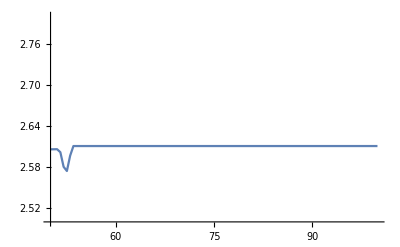

```mathematica
(*ListPlot[ExtCoPLineListdwA10,Joined->True,PlotRange->{{50,100},{2.5,2.8}}]*)
```

```mathematica
(*{{52,CoPValLine[1/1000,1,10,10,520]},{105/2,CoPValLine[1/1000,1,10,10,525]},{53,CoPValLine[1/1000,1,10,10,530]}}*)
```

{{52,2.58046},{105/2,2.57433},{53,2.59674}}

```mathematica
(*CoPLineListdwA12=Table[{d/12,CoPValLine[1/1200,1,12,12,d]},{d,0,(1200-(12+12))/2}]*)
```

```mathematica
CoPLineListdwA12={{0,2.5636112593716756},{1/12,2.6034734603734613},{1/6,2.6199703612687495},{1/4,2.63167202636712},{1/3,2.640926462072178},{5/12,2.6486262453438214},{1/2,2.655230292586756},{7/12,2.661012579887274},{2/3,2.6661522864706537},{3/4,2.6707740983679757},{5/6,2.674968795214513},{11/12,2.6788047926091894},{1,2.6823350779658033},{13/12,2.6856016086841517},{7/6,2.6886382236437845},{5/4,2.6914726399003666},{4/3,2.694127862908526},{17/12,2.6966232077666605},{3/2,2.6989750548608074},{19/12,2.701197419519324},{5/3,2.7033023885401337},{7/4,2.7053004596074777},{11/6,2.707200808642579},{23/12,2.7090115028276758},{2,2.710739672116368},{25/12,2.712391648720206},{13/6,2.713973081400728},{9/4,2.715489029987316},{7/3,2.716944044027885},{29/12,2.718342228774076},{5/2,2.7196873007485958},{31/12,2.7209826349259343},{8/3,2.722231304985609},{11/4,2.7234361177657624},{17/6,2.724599642983177},{35/12,2.725724238873963},{3,2.7268120745716664},{37/12,2.727865149489368},{19/6,2.7288853103794457},{13/4,2.729874266253177},{10/3,2.7308336015969603},{41/12,2.7317647879672444},{7/2,2.732669194328741},{43/12,2.7335480962241143},{11/3,2.734402683957854},{15/4,2.7352340699010105},{23/6,2.736043295020397},{47/12,2.7368313347808226},{4,2.737599104417897},{49/12,2.7383474637021963},{25/6,2.739077221270027},{17/4,2.739789138513624},{13/3,2.7404839331253306},{53/12,2.741162282320264},{9/2,2.741824825741328},{55/12,2.7424721681712088},{14/3,2.7431048819442774},{19/4,2.7437235091851866},{29/6,2.7443285638590598},{59/12,2.7449205336497515},{5,2.745499881674969},{61/12,2.7460670480898615},{31/6,2.7466224515318287},{21/4,2.747166490485236},{16/3,2.747699544508017},{65/12,2.7482219754077106},{11/2,2.7487341282985382},{67/12,2.7492363325720572},{17/3,2.749728902849466},{23/4,2.7502121398085104},{35/6,2.7506863309751064},{71/12,2.751151751482469},{6,2.751608664742101},{73/12,2.752057323076558},{37/6,2.7524979683350486},{25/4,2.7529308324493416},{19/3,2.753356137954136},{77/12,2.7537740984582832},{13/2,2.754184919136831},{79/12,2.754588796565294},{20/3,2.754985920719668},{27/4,2.7553764739638376},{41/6,2.75576063171664},{83/12,2.7561385628306625},{7,2.756510429924705},{85/12,2.7568763896686765},{43/6,2.757236593074502},{29/4,2.757591185752681},{22/3,2.7579403081574263},{89/12,2.7582840958581554},{15/2,2.7586226797793394},{91/12,2.7589561873636423},{23/3,2.7592847395705236},{31/4,2.759608454291245},{47/6,2.7599274455140677},{95/12,2.760241823518409},{8,2.760551694970907},{97/12,2.760857163079782},{49/6,2.7611583277810507},{33/4,2.7614552858189456},{25/3,2.761748130879527},{101/12,2.7620369537563656},{17/2,2.762321842362295},{103/12,2.7626028815044106},{26/3,2.762880154513073},{35/4,2.7631537416242686},{53/6,2.7634237206977725},{107/12,2.7636901672806924},{9,2.763953154714149},{109/12,2.764212754216117},{55/6,2.764469034961955},{37/4,2.7647220641511567},{28/3,2.7649719070795027},{113/12,2.765218627214567},{19/2,2.7654622862664646},{115/12,2.7657029442337744},{29/3,2.7659406594734013},{39/4,2.7661754887753083},{59/6,2.766407487382866},{119/12,2.766636709062688},{10,2.766863206177433},{121/12,2.767087029693889},{61/6,2.7673082292550144},{41/4,2.7675268532180954},{31/3,2.7677429486968688},{125/12,2.7679565616125448},{21/2,2.7681677367030093},{127/12,2.7683765176065425},{32/3,2.7685829468559904},{43/4,2.7687870659432146},{65/6,2.768988915326805},{131/12,2.7691885344915788},{11,2.769385961952526},{133/12,2.7695812353081544},{67/6,2.7697743912576556},{45/4,2.769965465624182},{34/3,2.7701544933889473},{137/12,2.770341508717018},{23/2,2.7705265449812946},{139/12,2.7707096347742244},{35/3,2.7708908099531224},{47/4,2.771070101644721},{71/6,2.7712475402678947},{143/12,2.77142315556563},{12,2.77159697661007},{145/12,2.7717690318347104},{73/6,2.7719393490438433},{49/4,2.772107955421066},{37/3,2.7722748775808297},{149/12,2.772440141553935},{25/2,2.7726037727933543},{151/12,2.772765796240029},{38/3,2.7729262362855054},{51/4,2.773085116808213},{77/6,2.7732424611908697},{155/12,2.7733982923300085},{13,2.773552632645624},{157/12,2.7737055040948704},{79/6,2.7738569281915137},{53/4,2.77400692600222},{40/3,2.7741555181768747},{161/12,2.77430272494764},{27/2,2.7744485661410017},{163/12,2.7745930611916485},{41/3,2.7747362291477455},{55/4,2.774878088687412},{83/6,2.775018658118238},{167/12,2.775157955399525},{14,2.775295998138484},{169/12,2.7754328036135023},{85/6,2.775568388748967},{57/4,2.775702770181565},{43/3,2.775835964211683},{173/12,2.775967986834842},{29/2,2.776098853756694},{175/12,2.7762285803916797},{44/3,2.7763571818530157},{59/4,2.776484672998153},{89/6,2.7766110683991214},{179/12,2.776736382369419},{15,2.776860628955509},{181/12,2.7769838219571343},{91/6,2.7771059749320552},{61/4,2.777227101190213},{46/3,2.7773472138031345},{185/12,2.777466325615877},{31/2,2.7775844492448134},{187/12,2.7777015971015366},{47/3,2.7778177813587828},{63/4,2.777933013997419},{95/6,2.7780473067833706},{191/12,2.778160671282562},{16,2.77827311887159},{193/12,2.7783846607181757},{97/6,2.7784953078143073},{65/4,2.778605070972116},{49/3,2.77871396081172},{197/12,2.7788219877815017},{33/2,2.7789291621595567},{199/12,2.7790354940563757},{50/3,2.779140993401524},{67/4,2.779245669985098},{101/6,2.77934953342749},{203/12,2.7794525931967753},{17,2.779554858593183},{205/12,2.779656338795497},{103/6,2.7797570428197584},{69/4,2.779856979543411},{52/3,2.7799561576963816},{209/12,2.780054585885242},{35/2,2.7801522725747607},{211/12,2.780249226089985},{53/3,2.780345454637844},{71/4,2.780440966301414},{107/6,2.780535769036429},{215/12,2.7806298706595762},{18,2.7807232788986678},{217/12,2.7808160013460306},{109/6,2.780908045481168},{73/4,2.7809994186743117},{55/3,2.781090128185915},{221/12,2.7811801811656056},{37/2,2.7812695846557576},{223/12,2.781358345602279},{56/3,2.781446470838695},{75/4,2.781533967114008},{113/6,2.781620841053054},{227/12,2.781707099211446},{19,2.7817927480377365},{229/12,2.781877793890217},{115/6,2.7819622430217565},{77/4,2.7820461016264435},{58/3,2.782129375780604},{233/12,2.782212071496084},{39/2,2.7822941946805386},{235/12,2.7823757511734457},{59/3,2.7824567467283687},{79/4,2.782537187017276},{119/6,2.7826170776375694},{239/12,2.782696424096834},{20,2.7827752318389973},{241/12,2.782853506237359},{121/6,2.7829312525785057},{81/4,2.783008476084865},{61/3,2.7830851819076723},{245/12,2.783161375125652},{41/2,2.783237060751736},{247/12,2.783312243736515},{62/3,2.7833869289467015},{83/4,2.7834611212023392},{125/6,2.7835348252610363},{251/12,2.783608045797499},{21,2.783680787450556},{253/12,2.783753054777918},{127/6,2.783824852290892},{85/4,2.78389618443181},{64/3,2.7839670555957583},{257/12,2.7840374701077977},{43/2,2.784107432258224},{259/12,2.7841769462573973},{65/3,2.784246016278481},{87/4,2.7843146464453876},{131/6,2.7843828408046716},{263/12,2.7844506033854444},{22,2.784517938140737},{265/12,2.78458484898751},{133/6,2.7846513397867128},{89/4,2.7847174143534117},{67/3,2.7847830764578383},{269/12,2.7848483298174487},{45/2,2.7849131781154854},{271/12,2.784977624973726},{68/3,2.7850416739828456},{91/4,2.785105328687464},{137/6,2.7851685925880387},{275/12,2.7852314691309688},{23,2.7852939617467207},{277/12,2.7853560737957697},{139/6,2.7854178086226073},{93/4,2.7854791695212464},{70/3,2.7855401597379466},{281/12,2.785600782500166},{47/2,2.7856610409751625},{283/12,2.785720938317566},{71/3,2.7857804776160466},{95/4,2.7858396619509245},{143/6,2.7858984943508505},{287/12,2.7859569778114075},{24,2.7860151152943637},{289/12,2.786072909727046},{145/6,2.78613036400777},{97/4,2.786187480995131},{73/3,2.786244263518147},{293/12,2.7863007143739598},{49/2,2.7863568363235216},{295/12,2.786412632107086},{74/3,2.786468104418735},{99/4,2.7865232559307147},{149/6,2.7865780892943417},{299/12,2.78663260711309},{25,2.7866868119749952},{301/12,2.7867407064294327},{151/6,2.786794293009295},{101/4,2.7868475742055834},{76/3,2.786900552497839},{305/12,2.7869532303239293},{51/2,2.787005610102652},{307/12,2.7870576942261813},{77/3,2.787109485059033},{103/4,2.787160984941011},{155/6,2.7872121961822027},{311/12,2.78726312107045},{26,2.7873137618798496},{313/12,2.787364120839551},{157/6,2.7874142001740125},{105/4,2.787464002073341},{79/3,2.78751352870472},{317/12,2.787562782215369},{53/2,2.78761176473313},{319/12,2.787660478357479},{80/3,2.7877089251608527},{107/4,2.7877571072106524},{161/6,2.787805026539894},{323/12,2.7878526851639576},{27,2.7879000850776836},{325/12,2.787947228255937},{163/6,2.7879941166488016},{109/4,2.78804075218555},{82/3,2.7880871367874707},{329/12,2.788133272347818},{55/2,2.788179160739561},{331/12,2.7882248038183657},{83/3,2.788270203419052},{111/4,2.7883153613656795},{167/6,2.788360279451558},{335/12,2.7884049594669347},{28,2.788449403162721},{337/12,2.788493612296468},{169/6,2.788537588596698},{113/4,2.7885813337697942},{85/3,2.7886248495146666},{341/12,2.7886681375142093},{57/2,2.7887111994146796},{343/12,2.788754036878676},{86/3,2.7887966515245597},{115/4,2.788839044974181},{173/6,2.788881218816788},{347/12,2.78892317463834},{29,2.7889649140100343},{349/12,2.789006438474864},{175/6,2.789047749578215},{117/4,2.7890888488315624},{88/3,2.7891297377521003},{353/12,2.789170417830381},{59/2,2.789210890543715},{355/12,2.7892511573579233},{89/3,2.7892912197238586},{119/4,2.7893310790777592},{179/6,2.7893707368489364},{359/12,2.7894101944330254},{30,2.7894494532415584},{361/12,2.7894885146555772},{181/6,2.7895273800398956},{121/4,2.7895660507565174},{91/3,2.789604528149774},{365/12,2.7896428135570037},{61/2,2.7896809082966563},{367/12,2.7897188136763704},{92/3,2.7897565309933343},{123/4,2.789794061531337},{185/6,2.7898314065648484},{371/12,2.789868567360753},{31,2.789905545155109},{373/12,2.7899423411998},{187/6,2.789978956710038},{125/4,2.7900153929142495},{94/3,2.7900516510128406},{377/12,2.7900877321990842},{63/2,2.7901236376585143},{379/12,2.7901593685624686},{95/3,2.7901949260754804},{127/4,2.7902303113508133},{191/6,2.790265525527897},{383/12,2.790300569739806},{32,2.790335445113638},{385/12,2.7903701527509917},{193/6,2.7904046937614337},{129/4,2.7904390692381678},{97/3,2.790473280264169},{389/12,2.790507327909396},{65/2,2.7905412132447136},{391/12,2.790574937316931},{98/3,2.790608501180884},{131/4,2.7906419058692533},{197/6,2.79067515240516},{395/12,2.7907082418191234},{33,2.7907411751109197},{397/12,2.790773953291881},{199/6,2.7908065773446755},{133/4,2.790839048267292},{100/3,2.7908713670198764},{401/12,2.7909035345876854},{67/2,2.7909355519155965},{403/12,2.79096741996618},{101/3,2.790999139681756},{135/4,2.791030711990055},{203/6,2.7910621378303238},{407/12,2.7910934181142917},{34,2.7911245537593126},{409/12,2.7911555456752684},{205/6,2.7911863947433866},{137/4,2.7912171018695835},{103/3,2.7912476679325953},{413/12,2.791278093807627},{69/2,2.791308380356744},{415/12,2.791338528447475},{104/3,2.7913685389344822},{139/4,2.7913984126658296},{209/6,2.7914281504758773},{419/12,2.791457753196367},{35,2.7914872216627944},{421/12,2.7915165566930247},{211/6,2.7915457590986814},{141/4,2.791574829679799},{106/3,2.7916037692451963},{425/12,2.7916325785875933},{71/2,2.791661258491204},{427/12,2.791689809742354},{107/3,2.791718233109337},{143/4,2.79174652936719},{215/6,2.791774699270041},{431/12,2.7918027435837303},{36,2.791830663058998},{433/12,2.7918584584281727},{217/6,2.7918861304441727},{145/4,2.7919136798273394},{109/3,2.791941107317153},{437/12,2.7919684136310545},{73/2,2.791995599478279},{439/12,2.7920226655784086},{110/3,2.7920496126333205},{147/4,2.792076441337761},{221/6,2.792103152394884},{443/12,2.7921297464795214},{37,2.792156224291696},{445/12,2.7921825864965095},{223/6,2.7922088337685698},{149/4,2.7922349667806894},{112/3,2.7922609861959193},{449/12,2.792286892665835},{75/2,2.792312686840086},{451/12,2.792338369379094},{113/3,2.79236394091674},{151/4,2.7923894020866933},{227/6,2.7924147535313337},{455/12,2.7924399958754225},{38,2.792465129739973},{457/12,2.7924901557510635},{229/6,2.7925150745074596},{153/4,2.7925398866327593},{115/3,2.7925645927317295},{461/12,2.7925891933943094},{77/2,2.7926136892280304},{463/12,2.7926380808119746},{116/3,2.792662368743373},{155/4,2.7926865536034633},{233/6,2.7927106359695792},{467/12,2.7927346164182882},{39,2.7927584955138807},{469/12,2.7927822738258423},{235/6,2.7928059519160677},{157/4,2.792829530342974},{118/3,2.7928530096587583},{473/12,2.792876390412209},{79/2,2.7928996731524336},{475/12,2.7929228584180623},{119/3,2.7929459467445046},{159/4,2.7929689386693393},{239/6,2.7929918347226956},{479/12,2.7930146354290026},{40,2.793037341312607},{481/12,2.793059952888888},{241/6,2.7930824706758224},{161/4,2.7931048951838715},{121/3,2.793127226921469},{485/12,2.793149466391093},{81/2,2.7931716140896303},{487/12,2.7931936705211062},{122/3,2.7932156361752316},{163/4,2.793237511543472},{245/6,2.7932592971130474},{491/12,2.7932809933605784},{41,2.7933026007707964},{493/12,2.7933241198230108},{247/6,2.7933455509851495},{165/4,2.7933668947262205},{124/3,2.793388151516528},{497/12,2.793409321817624},{83/2,2.793430406086125},{499/12,2.7934514047845287},{125/3,2.793472318354992},{167/4,2.793493147405087},{251/6,2.793513892820732},{503/12,2.7935345561609313},{42,2.7935551471811544},{505/12,2.7935756054252834},{253/6,2.793595902989112},{169/4,2.7936166981384347},{127/3,2.7936375371700963},{509/12,2.793659009359889},{85/2,2.793260100164331},{511/12,2.787866200377945},{128/3,2.782133493435207},{171/4,2.7763550342530685},{257/6,2.770598172695499},{515/12,2.764898099627798},{43,2.7592824754759753},{517/12,2.7537818299375645},{259/6,2.7484374717863305},{173/4,2.7432956252993836},{130/3,2.7384755299325314},{521/12,2.7338457728194436},{87/2,2.7355411371152845},{523/12,2.740203633473022},{131/3,2.745596250459786},{175/4,2.7513197452158553},{263/6,2.757230169129841},{527/12,2.7632566538728196},{44,2.7693561447726966},{529/12,2.7754969962604976},{265/6,2.781650207740807},{177/4,2.787783927336168},{133/3,2.7938422191897296},{533/12,2.7999574225275112},{89/2,2.79995742252824},{535/12,2.7999574225248116},{134/3,2.7999574225280646},{179/4,2.7999574225267994},{269/6,2.799957422525047},{539/12,2.79995742252578},{45,2.7999574225256616},{541/12,2.7999574225262016},{271/6,2.7999574225276564},{181/4,2.799957422525381},{136/3,2.7999574225252646},{545/12,2.7999574225245953},{91/2,2.7999574225274255},{547/12,2.7999574225284287},{137/3,2.7999574225264583},{183/4,2.799957422528146},{275/6,2.799957422526013},{551/12,2.7999574225254853},{46,2.7999574225241046},{553/12,2.7999574225289985},{277/6,2.7999574225252952},{185/4,2.799957422525144},{139/3,2.7999574225260284},{557/12,2.799957422524941},{93/2,2.7999574225280472},{559/12,2.7999574225283417},{140/3,2.7999574225252983},{187/4,2.799957422525626},{281/6,2.7999574225266546},{563/12,2.799957422524699},{47,2.7999574225249715},{565/12,2.7999574225241792},{283/6,2.7999574225247335},{189/4,2.7999574225244066},{142/3,2.7999574225248107},{569/12,2.799957422524843},{95/2,2.799957422528916},{571/12,2.7999574225244275},{143/3,2.79995742252639},{191/4,2.7999574225251256},{287/6,2.7999574225254604},{575/12,2.7999574225255404},{48,2.7999574225242045},{577/12,2.799957422528961},{289/6,2.7999574225259036},{193/4,2.799957422526462},{145/3,2.79995742252402},{581/12,2.7999574225270876},{97/2,2.799957422524344},{583/12,2.799957422524051},{146/3,2.7999574225246113},{195/4,2.799957422524027},{293/6,2.7999574225267394},{587/12,2.799957422528923},{49,2.799957422525658}};
```

```mathematica
BadPointsCoPLineListdwA12={{127/3,2.7936375371700963},{509/12,2.793659009359889},{85/2,2.793260100164331},{511/12,2.787866200377945},{128/3,2.782133493435207},{171/4,2.7763550342530685},{257/6,2.770598172695499},{515/12,2.764898099627798},{43,2.7592824754759753},{517/12,2.7537818299375645},{259/6,2.7484374717863305},{173/4,2.7432956252993836},{130/3,2.7384755299325314},{521/12,2.7338457728194436},{87/2,2.7355411371152845},{523/12,2.740203633473022},{131/3,2.745596250459786},{175/4,2.7513197452158553},{263/6,2.757230169129841},{527/12,2.7632566538728196},{44,2.7693561447726966},{529/12,2.7754969962604976},{265/6,2.781650207740807},{177/4,2.787783927336168},{133/3,2.7938422191897296},{533/12,2.7999574225275112},{89/2,2.79995742252824},{535/12,2.7999574225248116}};
```

```mathematica
AltCoPLineListdwA12={{0,2.5636112593716756},{1/12,2.6034734603734613},{1/6,2.6199703612687495},{1/4,2.63167202636712},{1/3,2.640926462072178},{5/12,2.6486262453438214},{1/2,2.655230292586756},{7/12,2.661012579887274},{2/3,2.6661522864706537},{3/4,2.6707740983679757},{5/6,2.674968795214513},{11/12,2.6788047926091894},{1,2.6823350779658033},{13/12,2.6856016086841517},{7/6,2.6886382236437845},{5/4,2.6914726399003666},{4/3,2.694127862908526},{17/12,2.6966232077666605},{3/2,2.6989750548608074},{19/12,2.701197419519324},{5/3,2.7033023885401337},{7/4,2.7053004596074777},{11/6,2.707200808642579},{23/12,2.7090115028276758},{2,2.710739672116368},{25/12,2.712391648720206},{13/6,2.713973081400728},{9/4,2.715489029987316},{7/3,2.716944044027885},{29/12,2.718342228774076},{5/2,2.7196873007485958},{31/12,2.7209826349259343},{8/3,2.722231304985609},{11/4,2.7234361177657624},{17/6,2.724599642983177},{35/12,2.725724238873963},{3,2.7268120745716664},{37/12,2.727865149489368},{19/6,2.7288853103794457},{13/4,2.729874266253177},{10/3,2.7308336015969603},{41/12,2.7317647879672444},{7/2,2.732669194328741},{43/12,2.7335480962241143},{11/3,2.734402683957854},{15/4,2.7352340699010105},{23/6,2.736043295020397},{47/12,2.7368313347808226},{4,2.737599104417897},{49/12,2.7383474637021963},{25/6,2.739077221270027},{17/4,2.739789138513624},{13/3,2.7404839331253306},{53/12,2.741162282320264},{9/2,2.741824825741328},{55/12,2.7424721681712088},{14/3,2.7431048819442774},{19/4,2.7437235091851866},{29/6,2.7443285638590598},{59/12,2.7449205336497515},{5,2.745499881674969},{61/12,2.7460670480898615},{31/6,2.7466224515318287},{21/4,2.747166490485236},{16/3,2.747699544508017},{65/12,2.7482219754077106},{11/2,2.7487341282985382},{67/12,2.7492363325720572},{17/3,2.749728902849466},{23/4,2.7502121398085104},{35/6,2.7506863309751064},{71/12,2.751151751482469},{6,2.751608664742101},{73/12,2.752057323076558},{37/6,2.7524979683350486},{25/4,2.7529308324493416},{19/3,2.753356137954136},{77/12,2.7537740984582832},{13/2,2.754184919136831},{79/12,2.754588796565294},{20/3,2.754985920719668},{27/4,2.7553764739638376},{41/6,2.75576063171664},{83/12,2.7561385628306625},{7,2.756510429924705},{85/12,2.7568763896686765},{43/6,2.757236593074502},{29/4,2.757591185752681},{22/3,2.7579403081574263},{89/12,2.7582840958581554},{15/2,2.7586226797793394},{91/12,2.7589561873636423},{23/3,2.7592847395705236},{31/4,2.759608454291245},{47/6,2.7599274455140677},{95/12,2.760241823518409},{8,2.760551694970907},{97/12,2.760857163079782},{49/6,2.7611583277810507},{33/4,2.7614552858189456},{25/3,2.761748130879527},{101/12,2.7620369537563656},{17/2,2.762321842362295},{103/12,2.7626028815044106},{26/3,2.762880154513073},{35/4,2.7631537416242686},{53/6,2.7634237206977725},{107/12,2.7636901672806924},{9,2.763953154714149},{109/12,2.764212754216117},{55/6,2.764469034961955},{37/4,2.7647220641511567},{28/3,2.7649719070795027},{113/12,2.765218627214567},{19/2,2.7654622862664646},{115/12,2.7657029442337744},{29/3,2.7659406594734013},{39/4,2.7661754887753083},{59/6,2.766407487382866},{119/12,2.766636709062688},{10,2.766863206177433},{121/12,2.767087029693889},{61/6,2.7673082292550144},{41/4,2.7675268532180954},{31/3,2.7677429486968688},{125/12,2.7679565616125448},{21/2,2.7681677367030093},{127/12,2.7683765176065425},{32/3,2.7685829468559904},{43/4,2.7687870659432146},{65/6,2.768988915326805},{131/12,2.7691885344915788},{11,2.769385961952526},{133/12,2.7695812353081544},{67/6,2.7697743912576556},{45/4,2.769965465624182},{34/3,2.7701544933889473},{137/12,2.770341508717018},{23/2,2.7705265449812946},{139/12,2.7707096347742244},{35/3,2.7708908099531224},{47/4,2.771070101644721},{71/6,2.7712475402678947},{143/12,2.77142315556563},{12,2.77159697661007},{145/12,2.7717690318347104},{73/6,2.7719393490438433},{49/4,2.772107955421066},{37/3,2.7722748775808297},{149/12,2.772440141553935},{25/2,2.7726037727933543},{151/12,2.772765796240029},{38/3,2.7729262362855054},{51/4,2.773085116808213},{77/6,2.7732424611908697},{155/12,2.7733982923300085},{13,2.773552632645624},{157/12,2.7737055040948704},{79/6,2.7738569281915137},{53/4,2.77400692600222},{40/3,2.7741555181768747},{161/12,2.77430272494764},{27/2,2.7744485661410017},{163/12,2.7745930611916485},{41/3,2.7747362291477455},{55/4,2.774878088687412},{83/6,2.775018658118238},{167/12,2.775157955399525},{14,2.775295998138484},{169/12,2.7754328036135023},{85/6,2.775568388748967},{57/4,2.775702770181565},{43/3,2.775835964211683},{173/12,2.775967986834842},{29/2,2.776098853756694},{175/12,2.7762285803916797},{44/3,2.7763571818530157},{59/4,2.776484672998153},{89/6,2.7766110683991214},{179/12,2.776736382369419},{15,2.776860628955509},{181/12,2.7769838219571343},{91/6,2.7771059749320552},{61/4,2.777227101190213},{46/3,2.7773472138031345},{185/12,2.777466325615877},{31/2,2.7775844492448134},{187/12,2.7777015971015366},{47/3,2.7778177813587828},{63/4,2.777933013997419},{95/6,2.7780473067833706},{191/12,2.778160671282562},{16,2.77827311887159},{193/12,2.7783846607181757},{97/6,2.7784953078143073},{65/4,2.778605070972116},{49/3,2.77871396081172},{197/12,2.7788219877815017},{33/2,2.7789291621595567},{199/12,2.7790354940563757},{50/3,2.779140993401524},{67/4,2.779245669985098},{101/6,2.77934953342749},{203/12,2.7794525931967753},{17,2.779554858593183},{205/12,2.779656338795497},{103/6,2.7797570428197584},{69/4,2.779856979543411},{52/3,2.7799561576963816},{209/12,2.780054585885242},{35/2,2.7801522725747607},{211/12,2.780249226089985},{53/3,2.780345454637844},{71/4,2.780440966301414},{107/6,2.780535769036429},{215/12,2.7806298706595762},{18,2.7807232788986678},{217/12,2.7808160013460306},{109/6,2.780908045481168},{73/4,2.7809994186743117},{55/3,2.781090128185915},{221/12,2.7811801811656056},{37/2,2.7812695846557576},{223/12,2.781358345602279},{56/3,2.781446470838695},{75/4,2.781533967114008},{113/6,2.781620841053054},{227/12,2.781707099211446},{19,2.7817927480377365},{229/12,2.781877793890217},{115/6,2.7819622430217565},{77/4,2.7820461016264435},{58/3,2.782129375780604},{233/12,2.782212071496084},{39/2,2.7822941946805386},{235/12,2.7823757511734457},{59/3,2.7824567467283687},{79/4,2.782537187017276},{119/6,2.7826170776375694},{239/12,2.782696424096834},{20,2.7827752318389973},{241/12,2.782853506237359},{121/6,2.7829312525785057},{81/4,2.783008476084865},{61/3,2.7830851819076723},{245/12,2.783161375125652},{41/2,2.783237060751736},{247/12,2.783312243736515},{62/3,2.7833869289467015},{83/4,2.7834611212023392},{125/6,2.7835348252610363},{251/12,2.783608045797499},{21,2.783680787450556},{253/12,2.783753054777918},{127/6,2.783824852290892},{85/4,2.78389618443181},{64/3,2.7839670555957583},{257/12,2.7840374701077977},{43/2,2.784107432258224},{259/12,2.7841769462573973},{65/3,2.784246016278481},{87/4,2.7843146464453876},{131/6,2.7843828408046716},{263/12,2.7844506033854444},{22,2.784517938140737},{265/12,2.78458484898751},{133/6,2.7846513397867128},{89/4,2.7847174143534117},{67/3,2.7847830764578383},{269/12,2.7848483298174487},{45/2,2.7849131781154854},{271/12,2.784977624973726},{68/3,2.7850416739828456},{91/4,2.785105328687464},{137/6,2.7851685925880387},{275/12,2.7852314691309688},{23,2.7852939617467207},{277/12,2.7853560737957697},{139/6,2.7854178086226073},{93/4,2.7854791695212464},{70/3,2.7855401597379466},{281/12,2.785600782500166},{47/2,2.7856610409751625},{283/12,2.785720938317566},{71/3,2.7857804776160466},{95/4,2.7858396619509245},{143/6,2.7858984943508505},{287/12,2.7859569778114075},{24,2.7860151152943637},{289/12,2.786072909727046},{145/6,2.78613036400777},{97/4,2.786187480995131},{73/3,2.786244263518147},{293/12,2.7863007143739598},{49/2,2.7863568363235216},{295/12,2.786412632107086},{74/3,2.786468104418735},{99/4,2.7865232559307147},{149/6,2.7865780892943417},{299/12,2.78663260711309},{25,2.7866868119749952},{301/12,2.7867407064294327},{151/6,2.786794293009295},{101/4,2.7868475742055834},{76/3,2.786900552497839},{305/12,2.7869532303239293},{51/2,2.787005610102652},{307/12,2.7870576942261813},{77/3,2.787109485059033},{103/4,2.787160984941011},{155/6,2.7872121961822027},{311/12,2.78726312107045},{26,2.7873137618798496},{313/12,2.787364120839551},{157/6,2.7874142001740125},{105/4,2.787464002073341},{79/3,2.78751352870472},{317/12,2.787562782215369},{53/2,2.78761176473313},{319/12,2.787660478357479},{80/3,2.7877089251608527},{107/4,2.7877571072106524},{161/6,2.787805026539894},{323/12,2.7878526851639576},{27,2.7879000850776836},{325/12,2.787947228255937},{163/6,2.7879941166488016},{109/4,2.78804075218555},{82/3,2.7880871367874707},{329/12,2.788133272347818},{55/2,2.788179160739561},{331/12,2.7882248038183657},{83/3,2.788270203419052},{111/4,2.7883153613656795},{167/6,2.788360279451558},{335/12,2.7884049594669347},{28,2.788449403162721},{337/12,2.788493612296468},{169/6,2.788537588596698},{113/4,2.7885813337697942},{85/3,2.7886248495146666},{341/12,2.7886681375142093},{57/2,2.7887111994146796},{343/12,2.788754036878676},{86/3,2.7887966515245597},{115/4,2.788839044974181},{173/6,2.788881218816788},{347/12,2.78892317463834},{29,2.7889649140100343},{349/12,2.789006438474864},{175/6,2.789047749578215},{117/4,2.7890888488315624},{88/3,2.7891297377521003},{353/12,2.789170417830381},{59/2,2.789210890543715},{355/12,2.7892511573579233},{89/3,2.7892912197238586},{119/4,2.7893310790777592},{179/6,2.7893707368489364},{359/12,2.7894101944330254},{30,2.7894494532415584},{361/12,2.7894885146555772},{181/6,2.7895273800398956},{121/4,2.7895660507565174},{91/3,2.789604528149774},{365/12,2.7896428135570037},{61/2,2.7896809082966563},{367/12,2.7897188136763704},{92/3,2.7897565309933343},{123/4,2.789794061531337},{185/6,2.7898314065648484},{371/12,2.789868567360753},{31,2.789905545155109},{373/12,2.7899423411998},{187/6,2.789978956710038},{125/4,2.7900153929142495},{94/3,2.7900516510128406},{377/12,2.7900877321990842},{63/2,2.7901236376585143},{379/12,2.7901593685624686},{95/3,2.7901949260754804},{127/4,2.7902303113508133},{191/6,2.790265525527897},{383/12,2.790300569739806},{32,2.790335445113638},{385/12,2.7903701527509917},{193/6,2.7904046937614337},{129/4,2.7904390692381678},{97/3,2.790473280264169},{389/12,2.790507327909396},{65/2,2.7905412132447136},{391/12,2.790574937316931},{98/3,2.790608501180884},{131/4,2.7906419058692533},{197/6,2.79067515240516},{395/12,2.7907082418191234},{33,2.7907411751109197},{397/12,2.790773953291881},{199/6,2.7908065773446755},{133/4,2.790839048267292},{100/3,2.7908713670198764},{401/12,2.7909035345876854},{67/2,2.7909355519155965},{403/12,2.79096741996618},{101/3,2.790999139681756},{135/4,2.791030711990055},{203/6,2.7910621378303238},{407/12,2.7910934181142917},{34,2.7911245537593126},{409/12,2.7911555456752684},{205/6,2.7911863947433866},{137/4,2.7912171018695835},{103/3,2.7912476679325953},{413/12,2.791278093807627},{69/2,2.791308380356744},{415/12,2.791338528447475},{104/3,2.7913685389344822},{139/4,2.7913984126658296},{209/6,2.7914281504758773},{419/12,2.791457753196367},{35,2.7914872216627944},{421/12,2.7915165566930247},{211/6,2.7915457590986814},{141/4,2.791574829679799},{106/3,2.7916037692451963},{425/12,2.7916325785875933},{71/2,2.791661258491204},{427/12,2.791689809742354},{107/3,2.791718233109337},{143/4,2.79174652936719},{215/6,2.791774699270041},{431/12,2.7918027435837303},{36,2.791830663058998},{433/12,2.7918584584281727},{217/6,2.7918861304441727},{145/4,2.7919136798273394},{109/3,2.791941107317153},{437/12,2.7919684136310545},{73/2,2.791995599478279},{439/12,2.7920226655784086},{110/3,2.7920496126333205},{147/4,2.792076441337761},{221/6,2.792103152394884},{443/12,2.7921297464795214},{37,2.792156224291696},{445/12,2.7921825864965095},{223/6,2.7922088337685698},{149/4,2.7922349667806894},{112/3,2.7922609861959193},{449/12,2.792286892665835},{75/2,2.792312686840086},{451/12,2.792338369379094},{113/3,2.79236394091674},{151/4,2.7923894020866933},{227/6,2.7924147535313337},{455/12,2.7924399958754225},{38,2.792465129739973},{457/12,2.7924901557510635},{229/6,2.7925150745074596},{153/4,2.7925398866327593},{115/3,2.7925645927317295},{461/12,2.7925891933943094},{77/2,2.7926136892280304},{463/12,2.7926380808119746},{116/3,2.792662368743373},{155/4,2.7926865536034633},{233/6,2.7927106359695792},{467/12,2.7927346164182882},{39,2.7927584955138807},{469/12,2.7927822738258423},{235/6,2.7928059519160677},{157/4,2.792829530342974},{118/3,2.7928530096587583},{473/12,2.792876390412209},{79/2,2.7928996731524336},{475/12,2.7929228584180623},{119/3,2.7929459467445046},{159/4,2.7929689386693393},{239/6,2.7929918347226956},{479/12,2.7930146354290026},{40,2.793037341312607},{481/12,2.793059952888888},{241/6,2.7930824706758224},{161/4,2.7931048951838715},{121/3,2.793127226921469},{485/12,2.793149466391093},{81/2,2.7931716140896303},{487/12,2.7931936705211062},{122/3,2.7932156361752316},{163/4,2.793237511543472},{245/6,2.7932592971130474},{491/12,2.7932809933605784},{41,2.7933026007707964},{493/12,2.7933241198230108},{247/6,2.7933455509851495},{165/4,2.7933668947262205},{124/3,2.793388151516528},{497/12,2.793409321817624},{83/2,2.793430406086125},{499/12,2.7934514047845287},{125/3,2.793472318354992},{167/4,2.793493147405087},{251/6,2.793513892820732},{503/12,2.7935345561609313},{42,2.7935551471811544},{505/12,2.7935756054252834},{253/6,2.793595902989112},{169/4,2.7936166981384347},{127/3,2.7936375371700963},{509/12,2.793659009359889},{533/12,2.7999574225275112},{89/2,2.79995742252824},{535/12,2.7999574225248116},{134/3,2.7999574225280646},{179/4,2.7999574225267994},{269/6,2.799957422525047},{539/12,2.79995742252578},{45,2.7999574225256616},{541/12,2.7999574225262016},{271/6,2.7999574225276564},{181/4,2.799957422525381},{136/3,2.7999574225252646},{545/12,2.7999574225245953},{91/2,2.7999574225274255},{547/12,2.7999574225284287},{137/3,2.7999574225264583},{183/4,2.799957422528146},{275/6,2.799957422526013},{551/12,2.7999574225254853},{46,2.7999574225241046},{553/12,2.7999574225289985},{277/6,2.7999574225252952},{185/4,2.799957422525144},{139/3,2.7999574225260284},{557/12,2.799957422524941},{93/2,2.7999574225280472},{559/12,2.7999574225283417},{140/3,2.7999574225252983},{187/4,2.799957422525626},{281/6,2.7999574225266546},{563/12,2.799957422524699},{47,2.7999574225249715},{565/12,2.7999574225241792},{283/6,2.7999574225247335},{189/4,2.7999574225244066},{142/3,2.7999574225248107},{569/12,2.799957422524843},{95/2,2.799957422528916},{571/12,2.7999574225244275},{143/3,2.79995742252639},{191/4,2.7999574225251256},{287/6,2.7999574225254604},{575/12,2.7999574225255404},{48,2.7999574225242045},{577/12,2.799957422528961},{289/6,2.7999574225259036},{193/4,2.799957422526462},{145/3,2.79995742252402},{581/12,2.7999574225270876},{97/2,2.799957422524344},{583/12,2.799957422524051},{146/3,2.7999574225246113},{195/4,2.799957422524027},{293/6,2.7999574225267394},{587/12,2.799957422528923},{49,2.799957422525658}};
```

### Plots

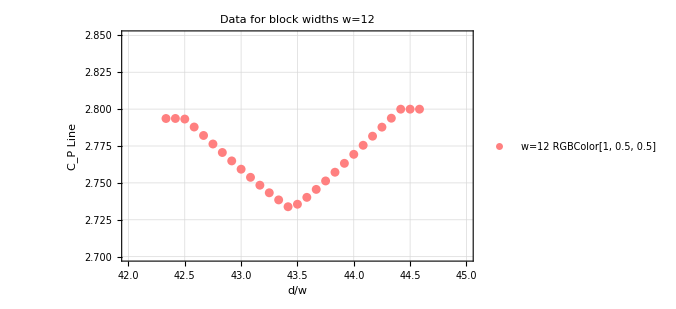

```mathematica
ListPlot[BadPointsCoPLineListdwA12,PlotTheme->"Detailed",PlotStyle->Pink,PlotRange->{{42,45},{2.7,2.85}},Joined->False,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=12",PlotLegends->{Pink"w=12"}]
```

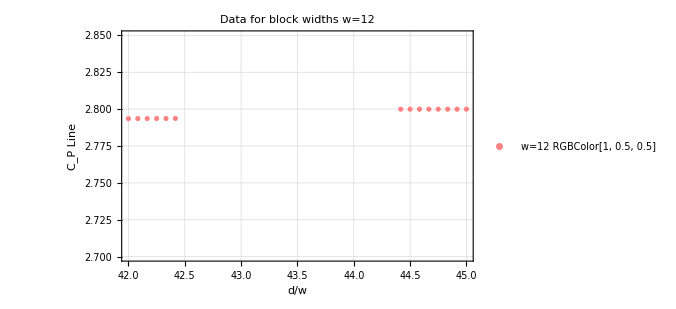

```mathematica
ListPlot[AltCoPLineListdwA12,PlotTheme->"Detailed",PlotStyle->Pink,PlotRange->{{42,45},{2.7,2.85}},Joined->False,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=12",PlotLegends->{Pink"w=12"}]
```

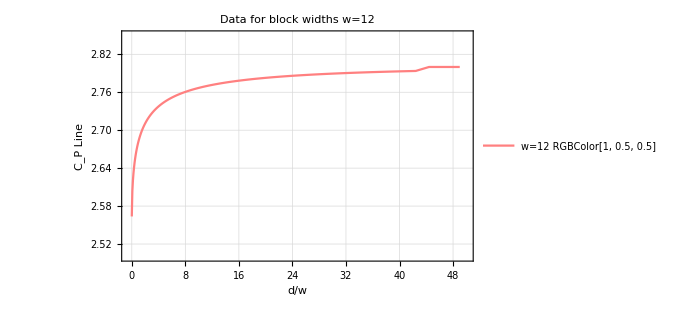

```mathematica
ListPlot[AltCoPLineListdwA12,PlotTheme->"Detailed",PlotStyle->Pink,PlotRange->{{-0.5,50},{2.5,2.85}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=12",PlotLegends->{Pink"w=12"}]
```

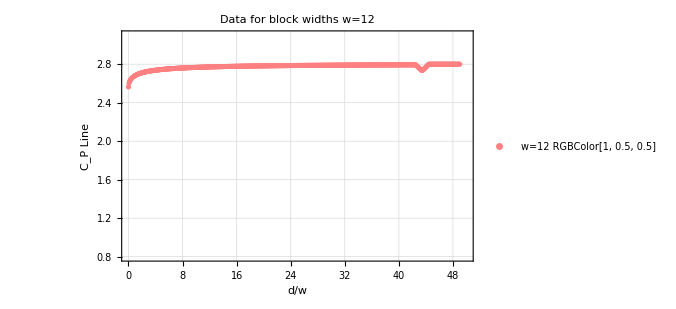

```mathematica
ListPlot[CoPLineListdwA12,PlotTheme->"Detailed",PlotStyle->Pink,PlotRange->{{0,50},{0.8,3.1}},Joined->False,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=12",PlotLegends->{Pink"w=12"}]
```

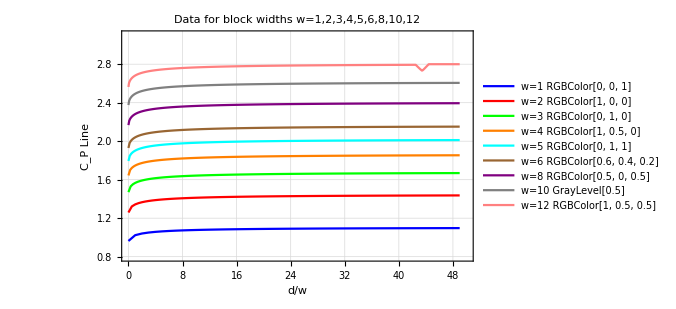

```mathematica
Show[ListPlot[{CoPLineListdwA1,CoPLineListdwA2,CoPLineListdwA3,CoPLineListdwA4,CoPLineListdwA5,CoPLineListdwA6,CoPLineListdwA8,CoPLineListdwA10,CoPLineListdwA12},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple,Gray,Pink},Joined->True,PlotRange->{{0,50},{0.8,3.1}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8,10,12",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8",Gray"w=10",Pink"w=12"}]]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CPLine.pdf",%825,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CPLine.pdf

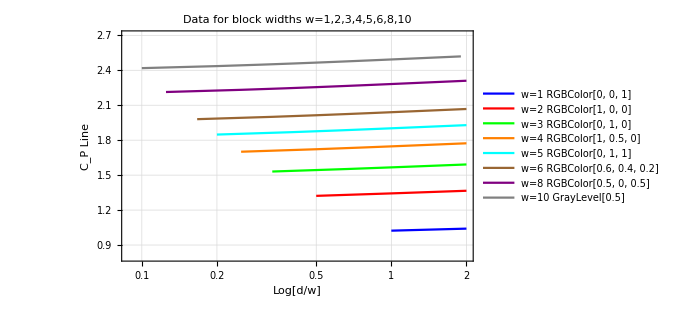

```mathematica
Show[ListLogLinearPlot[{CoPLineListdwA1⟦1;;3⟧,CoPLineListdwA2⟦1;;5⟧,CoPLineListdwA3⟦1;;7⟧,CoPLineListdwA4⟦1;;9⟧,CoPLineListdwA5⟦1;;11⟧,CoPLineListdwA6⟦1;;13⟧,CoPLineListdwA8⟦1;;17⟧,CoPLineListdwA10⟦1;;20⟧},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple,Gray},Joined->True,PlotRange->{{0,2},{0.8,2.7}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8,10",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8",Gray"w=10"}]]
```

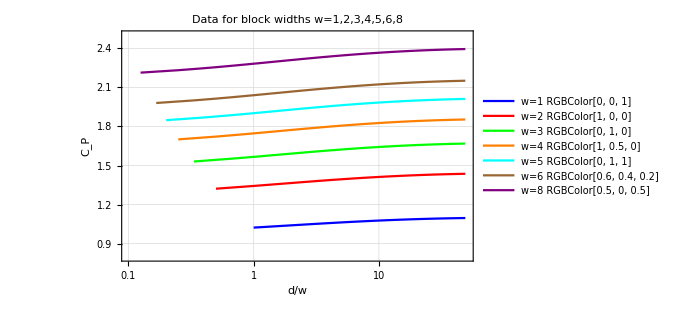

```mathematica
Show[ListLogLinearPlot[{CoPLineListdwA1,CoPLineListdwA2,CoPLineListdwA3,CoPLineListdwA4,CoPLineListdwA5,CoPLineListdwA6,CoPLineListdwA8},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->{{0.1,50},{0.8,2.5}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8"}]]
```

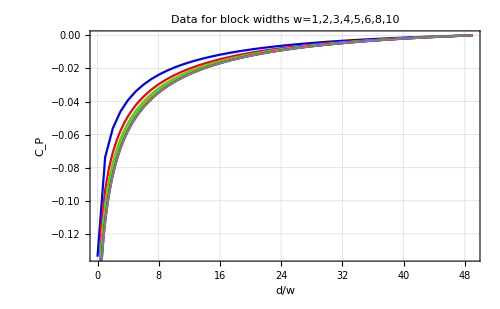

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA1]⟦2⟧}&/@CoPLineListdwA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8,10",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA2]⟦2⟧}&/@CoPLineListdwA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA3]⟦2⟧}&/@CoPLineListdwA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA4]⟦2⟧}&/@CoPLineListdwA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA5]⟦2⟧}&/@CoPLineListdwA5,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA6]⟦2⟧}&/@CoPLineListdwA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA8]⟦2⟧}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA10]⟦2⟧}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Gray},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]]
```

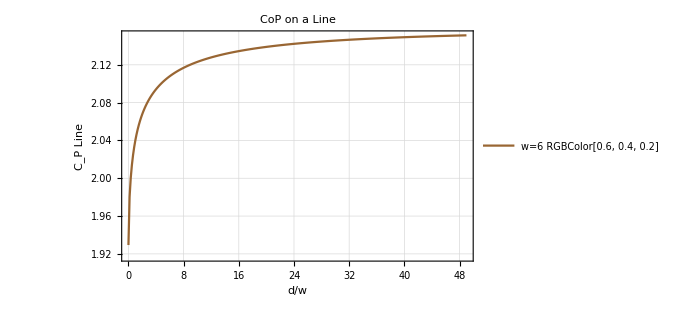

```mathematica
ListPlot[CoPLineListdwA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"CoP on a Line",PlotLegends->{Brown"w=6"}]
```

```mathematica
Length[CoPLineListdwA5]
```

246

```mathematica
1/3Log[500-10]//N
```

2.0648

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA5⟦2;;50⟧,a Log[x]+c,{a,c},x]]
```

1.90391+0.0357848 Log[x]

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA5⟦50;;100⟧,a Log[x]+c,{a,c},x]]
```

1.93212+0.0225919 Log[x]

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA5⟦80;;246⟧,a Log[x]+c,{a,c},x]]
```

1.95655+0.0143491 Log[x]

```mathematica
(*CoPLineListdwA5=Table[{d/5,CoPValLine[1/500,1,5,5,d]},{d,0,(500-(5+5))/2}]*)
```

```mathematica
m=1/500,w=5
```

```mathematica
1/6 N[Log[5*500]]
```

1.30401

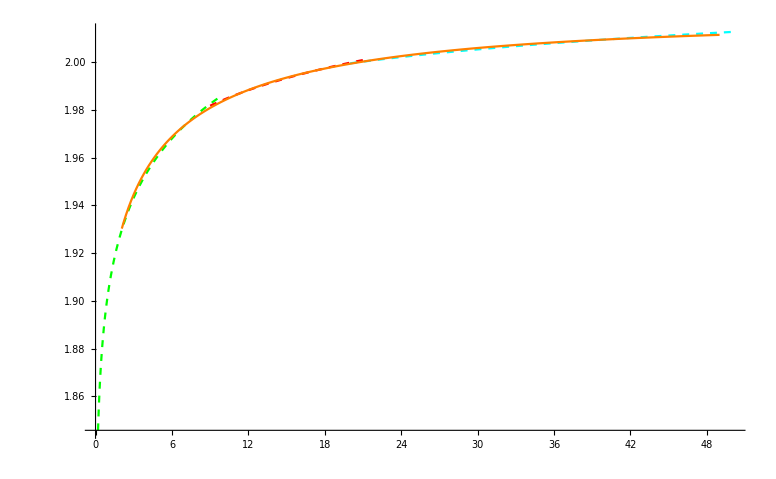

```mathematica
Show[Plot[1.9039053890559259+0.03578484691155455 Log[x],{x,0,10},PlotStyle->{Green,Dashed}],Plot[1.9321228691604053+0.02259193356000458 Log[x],{x,9,21},PlotStyle->{Red,Dashed}],Plot[1.956546454967211+0.014349076359208892 Log[x],{x,20,50},PlotStyle->{Cyan,Dashed}],ListPlot[CoPLineListdwA5,PlotStyle->{Orange},Joined->True],PlotRange-> All]
```

#### Analysis w=6

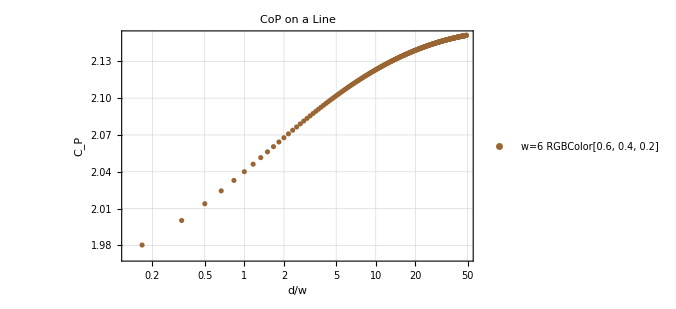

```mathematica
ListLogLinearPlot[CoPLineListdwA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->False,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"CoP on a Line",PlotLegends->{Brown"w=6"}]
```

```mathematica
Length[CoPLineListdwA6]
```

295

```mathematica
{{(600-12)/2-288//N,((600-12)/2-288)/6//N},{(600-12)/2-234//N,((600-12)/2-234)/6//N}}
```

{{6.,1.},{60.,10.}}

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA6⟦2;;6⟧,a Log[x]+c,{a,c},x]]
```

2.03761+0.0326328 Log[x]

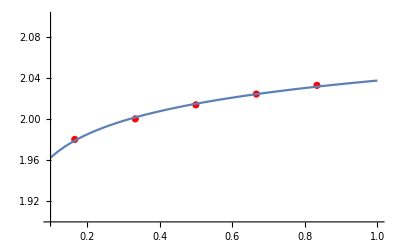

```mathematica
Show[ListPlot[CoPLineListdwA6⟦2;;6⟧,Joined->False,PlotRange->{{0.1,1},{1.9,2.1}},PlotStyle->{Red,Dashed}],Plot[2.0376074861471976+0.03263279067388575 Log[x],{x,0.1,1},PlotRange->{{0.1,1},{1.9,2.1}}]]
```

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA6⟦6;;60⟧,a Log[x]+c,{a,c},x]]
```

2.04271+0.0359991 Log[x]

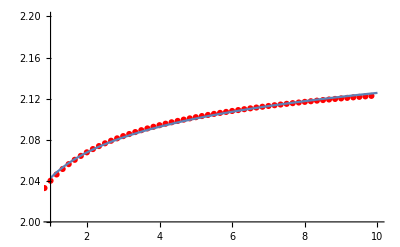

```mathematica
Show[ListPlot[CoPLineListdwA6⟦6;;60⟧,Joined->False,PlotRange->{{1,10},{2,2.2}},PlotStyle->{Red,Dashed}],Plot[2.0427061742483255+0.035999125780952254 Log[x],{x,1,10},PlotRange->{{1,10},{2,2.2}}]]
```

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA6⟦60;;295⟧,a Log[x]+c,{a,c},x]]
```

2.08773+0.0167608 Log[x]

```mathematica
{{(600-12)/2-234//N,((600-12)/2-234)/6//N},{(600-12)/2//N,((600-12)/2)/6//N}}
```

{{60.,10.},{294.,49.}}

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA6⟦60;;295⟧,a Log[x]+c,{a,c},x]]
```

2.08773+0.0167608 Log[x]

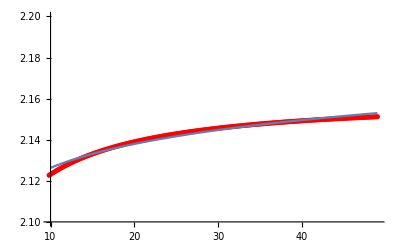

```mathematica
Show[ListPlot[CoPLineListdwA6⟦60;;295⟧,Joined->False,PlotRange->{{10,49},{2.1,2.2}},PlotStyle->{Red,Dashed}],Plot[2.0877286167349856+0.016760771233342592 Log[x],{x,10,49},PlotRange->{{10,49},{2.1,2.2}}]]
```

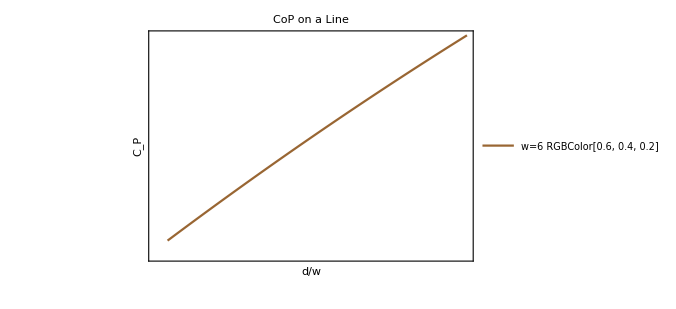

```mathematica
ListLogLogPlot[CoPLineListdwA6⟦250;;295⟧,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"CoP on a Line",PlotLegends->{Brown"w=6"}]
```

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA6⟦250;;295⟧,a Log[x]+c,{a,c},x]]
```

2.11391+0.00958452 Log[x]

```mathematica
Normal[NonlinearModelFit[CoPLineListdwA6⟦2;;295⟧,a Log[x]+c,{a,c},x]]
```

2.05491+0.0267179 Log[x]

```mathematica
(*CoPLineListdwA6=Table[{d/6,CoPValLine[1/600,1,6,6,d]},{d,0,(600-(6+6))/2}]*)
```

```mathematica
(*m=1/600,δ=1,w=6,d∈[0,294],d/w ∈ [0,49]*)
```

```mathematica
1/3Log[588]//N
```

2.12558

```mathematica
1/3Log[600]//N
```

2.13231

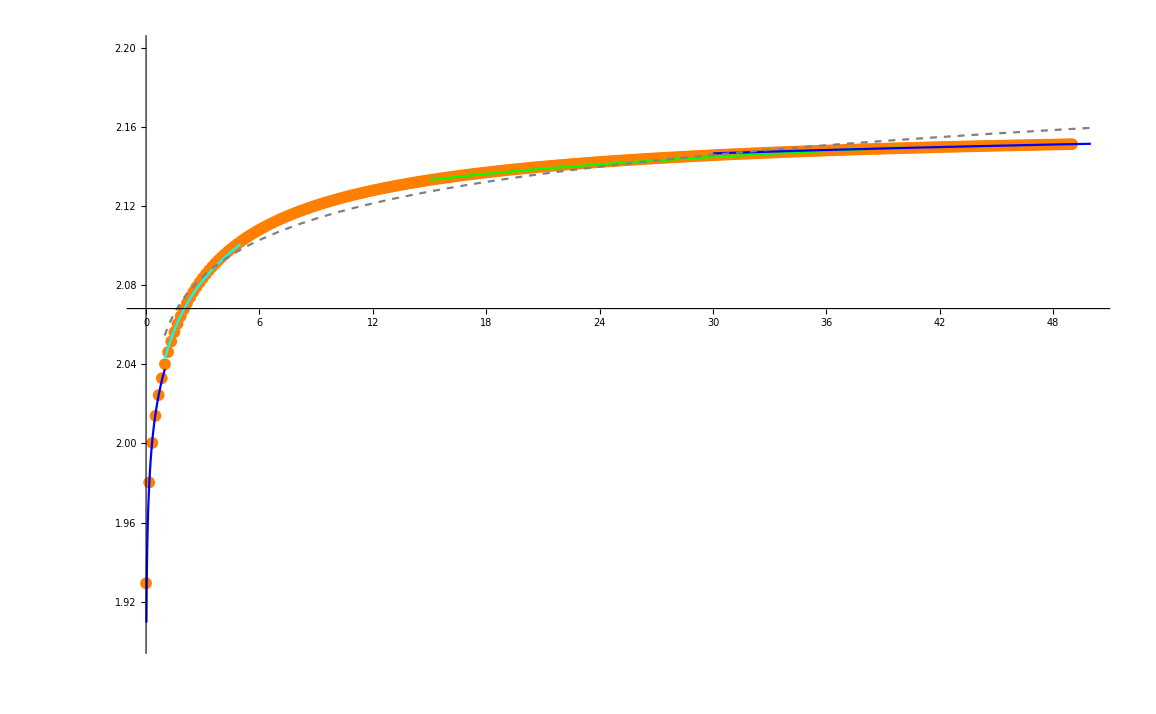

```mathematica
Show[ListPlot[CoPLineListdwA6,Joined->False,PlotStyle->Orange],Plot[2.0376074861471976+0.03263279067388575 Log[x],{x,0,1},PlotStyle->Blue],Plot[2.0427061742483255+0.035999125780952254 Log[x],{x,1,5},PlotStyle->Cyan],Plot[2.0877286167349856+0.016760771233342592 Log[x],{x,15,40},PlotStyle->Green],Plot[2.11391318773546+0.00958451842831213 Log[x],{x,30,50},PlotStyle->Blue],Plot[2.0549131085475114+0.02671786769532384 Log[x],{x,0,50},PlotStyle->{Dashed,Gray}],PlotRange-> {{0,50},{1.9,2.2}}]
```

### What to Subtract?

```mathematica
KGlineCorr[{NN_,m_,μ_}]:=KGlineCorr[{NN,m,μ}]={Table[(((μ HypergeometricPFQRegularized[{1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])/(2 √(4+m^2)))//N),{Mn,0,NN-1}],Table[((1/(2 μ)√(4+m^2) HypergeometricPFQRegularized[{-1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])//N),{Mn,0,NN-1}]}; 
KGlineToe[var_]:=KGlineToe[var]={ToeplitzMatrix[KGlineCorr[var]⟦1⟧],ToeplitzMatrix[KGlineCorr[var]⟦2⟧]};
KGlineCM[var_]:=KGlineCM[var]=ArrayFlatten[{{2KGlineToe[var]⟦1⟧,0.},{0.,2KGlineToe[var]⟦2⟧}}];
KGlineCMqpqp[{NN_,m_,μ_}]:=KGlineCMqpqp[{NN,m,μ}]=GOΩqpqp[NN].GOqpqpFROMqqpp[NN].KGlineCM[{NN,m,μ}].Transpose[GOqpqpFROMqqpp[NN]].Transpose[GOΩqpqp[NN]];
```

```mathematica
KGlineCMSep[{m_,μ_,dimA_,dimB_,d_}]:=KGlineCMSep[{m,μ,dimA,dimB,d}]=Module[{ind,KGlineCorr,KGlineToe},ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]]; 
KGlineCorr[{dimA+dimB+d,m,μ}]:={Table[(((μ HypergeometricPFQRegularized[{1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])/(2 √(4+m^2)))//N),{Mn,0,dimA+dimB+d-1}],Table[((1/(2 μ)√(4+m^2) HypergeometricPFQRegularized[{-1/2,1/2,1},{1-Mn,1+Mn},4/(4+m^2)])//N),{Mn,0,dimA+dimB+d-1}]}; 
KGlineToe[var_]:={ToeplitzMatrix[KGlineCorr[var]⟦1⟧],ToeplitzMatrix[KGlineCorr[var]⟦2⟧]};
GOΩqpqp[dimA+dimB].GOqpqpFROMqqpp[dimA+dimB].(ArrayFlatten[{{2KGlineToe[{dimA+dimB+d,m,μ}]⟦1,ind,ind⟧,0.},{0.,2KGlineToe[{dimA+dimB+d,m,μ}]⟦2,ind,ind⟧}}]).Transpose[GOqpqpFROMqqpp[dimA+dimB]].Transpose[GOΩqpqp[dimA+dimB]]]
```

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 10 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
VacCoPLine[m_,μ_,dimA1_,dimB1_,d_]:=Module[{dimPur,CM0,rlist,MTra,JT,JR,J0,M0,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific,time,Result},
dimPur=dimA1+dimB1;
CM0=KGlineCMSep[{m,μ,dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
J0=JR;
function=GOCoPBos[JT]; 
gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; 
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,+1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]];
```

```mathematica
CoPValLine[m_,μ_,dimA1_,dimB1_,d_]:=VacCoPLine[m,μ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
CoPTimeLine[m_,μ_,dimA1_,dimB1_,d_]:=VacCoPLine[m,μ,dimA1,dimB1,d]⟦1⟧;
```

```mathematica
KGlineCMSep[{1/100,1,1,1,200}]//Chop//MatrixForm
```

General::munfl: 0.0000249994/(9.2768×10^303) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000249994/(8.90921×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000249994/(8.73169378770484×10^311) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(1.27335 | 0 | -2.18612×10^-6 | 0
0 | 2.12777 | 0 | 0.0358112
-2.18612×10^-6 | 0 | 1.27335 | 0
0 | 0.0358112 | 0 | 2.12777)

```mathematica
SubtractCoPLinewA1=CoPValLine[1/100,1,1,0,0]
```

0.778093

```mathematica
SubtractCoPLinewA2=CoPValLine[1/200,1,2,0,0]
```

1.01881

```mathematica
SubtractCoPLinewA3=CoPValLine[1/300,1,3,0,0]
```

1.18316

```mathematica
SubtractCoPLinewA4=CoPValLine[1/400,1,4,0,0]
```

1.31411

```mathematica
SubtractCoPLinewA5=CoPValLine[1/500,1,5,0,0]
```

1.42576

```mathematica
SubtractCoPLinewA6=CoPValLine[1/600,1,6,0,0]
```

1.52461

```mathematica
SubtractCoPLinewA7=CoPValLine[1/700,1,7,0,0]
```

1.61422

```mathematica
SubtractCoPLinewA8=CoPValLine[1/800,1,8,0,0]
```

1.69677

```mathematica
SubtractCoPLinewA9=CoPValLine[1/900,1,9,0,0]
```

1.77372

```mathematica
SubtractCoPLinewA10=CoPValLine[1/1000,1,10,0,0]
```

1.84609

```mathematica
SubtractCoPLinewA11=CoPValLine[1/1100,1,11,0,0]
```

1.91462

```mathematica
SubtractCoPLinewA12=CoPValLine[1/1200,1,12,0,0]
```

1.97987

```mathematica
SubtractCoPLinewA13=CoPValLine[1/1300,1,13,0,0]
```

2.04228

```mathematica
SubtractCoPLinewA14=CoPValLine[1/1400,1,14,0,0]
```

2.10221

```mathematica
SubtractCoPLinewA15=CoPValLine[1/1500,1,15,0,0]
```

2.15993

```mathematica
SubtractCoPLinewA16=CoPValLine[1/1600,1,16,0,0]
```

2.21567

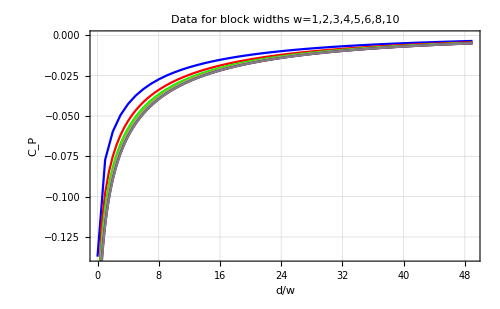

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA1}&/@CoPLineListdwA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8,10",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA2}&/@CoPLineListdwA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA3}&/@CoPLineListdwA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA4}&/@CoPLineListdwA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA5}&/@CoPLineListdwA5,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA6}&/@CoPLineListdwA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"],ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Gray},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPLine.pdf",%842,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPLine.pdf

```mathematica
{Sqrt[2]SubtractCoPLinewA10,Last[CoPLineListdwA10]⟦2⟧}
```

{2.61077,2.60581}

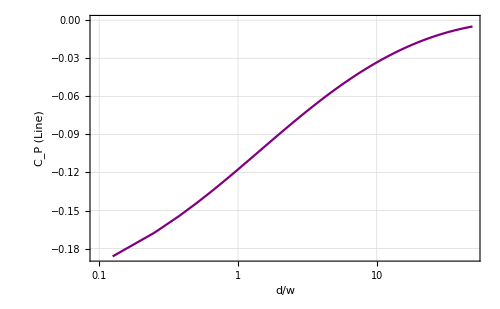

```mathematica
ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8),PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]
```

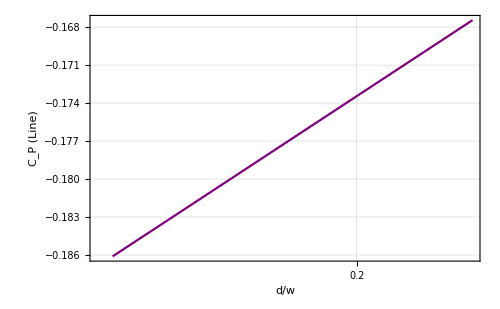

```mathematica
ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8)⟦1;;3⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]
```

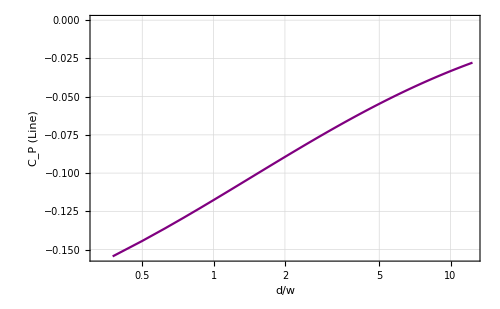

```mathematica
ListLogLinearPlot[({#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8)⟦4;;100⟧,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]
```

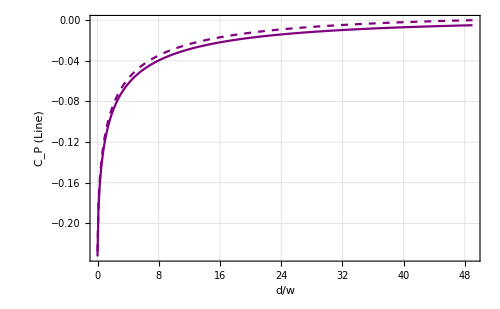

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA8]⟦2⟧}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Dashed,Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

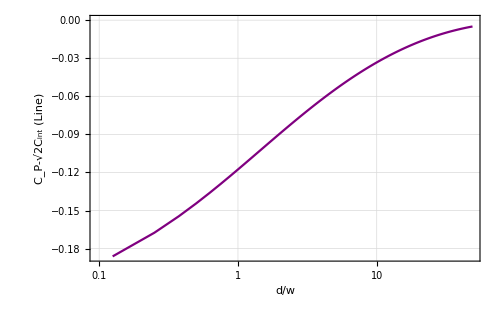

```mathematica
ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]
```

```mathematica
(*Very similar*)
```

```mathematica
Length[CoPLineListdwA8]
```

393

```mathematica
Normal[NonlinearModelFit[({#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8)⟦2;;393⟧,a+b Log[x],{a,b},x]]
```

-0.102668+0.0271368 Log[x]

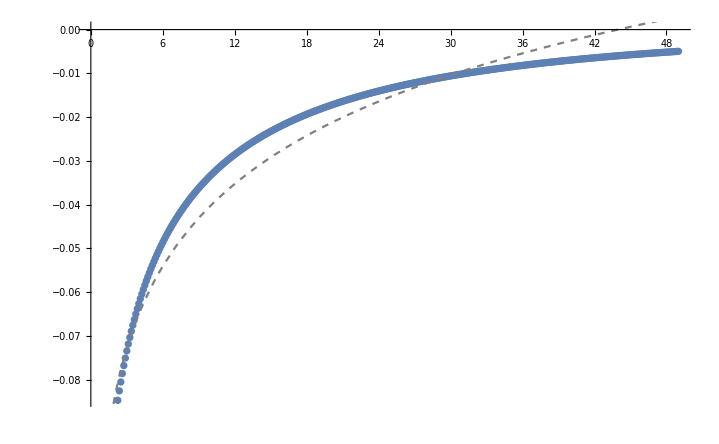

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8],Plot[-0.10266765689679011+0.027136845533403516 Log[x],{x,0,50},PlotStyle->{Dashed,Gray}]]
```

### Taking the Square?

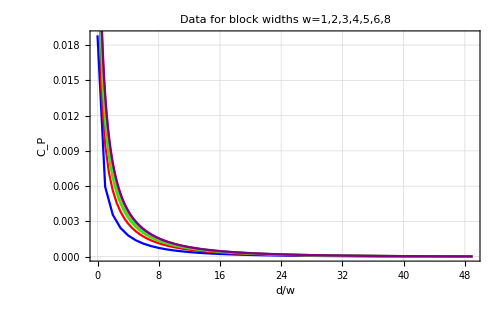

```mathematica
Show[ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA1)^2}&/@CoPLineListdwA1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->Blue"w=1"],ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA2)^2}&/@CoPLineListdwA2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA3)^2}&/@CoPLineListdwA3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA4)^2}&/@CoPLineListdwA4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA5)^2}&/@CoPLineListdwA5,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA6)^2}&/@CoPLineListdwA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA8)^2}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

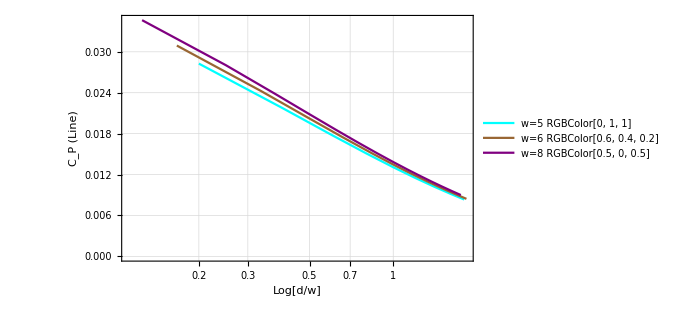

```mathematica
ListLogLinearPlot[{{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA5)^2}&/@CoPLineListdwA5⟦1;;10⟧,{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA6)^2}&/@CoPLineListdwA6⟦1;;12⟧,{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA8)^2}&/@CoPLineListdwA8⟦1;;15⟧},PlotTheme->"Detailed",PlotStyle->{Cyan,Brown,Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->{Cyan"w=5",Brown"w=6",Purple"w=8"}]
```

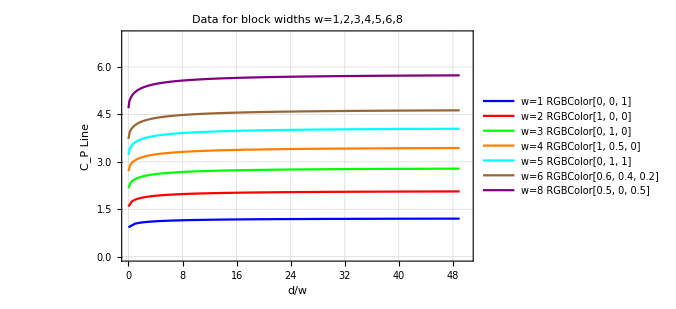

```mathematica
Show[ListPlot[{{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA1,{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA2,{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA3,{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA4,{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA5,{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA6,{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA8},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->{{0,50},{0,7}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4",Cyan"w=5",Brown"w=6",Purple"w=8"}]]
```

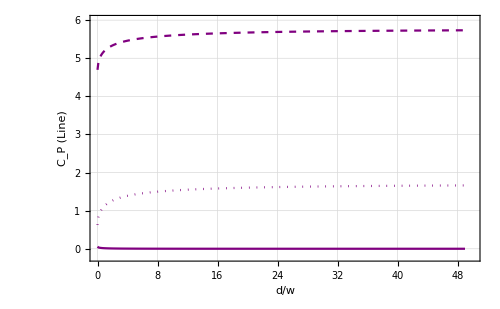

```mathematica
Show[ListPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA8)^2}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->{{0,50},{-0.2,6}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"],ListPlot[{#⟦1⟧,(#⟦2⟧)^2}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Dashed,Purple},Joined->True,PlotRange->{{0,50},{-0.2,6}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"],ListPlot[{#⟦1⟧,(#⟦2⟧)^2-Sqrt[2] SubtractCoPLinewA8^2}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Dotted,Purple},Joined->True,PlotRange->{{0,50},{-0.2,6}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]]
```

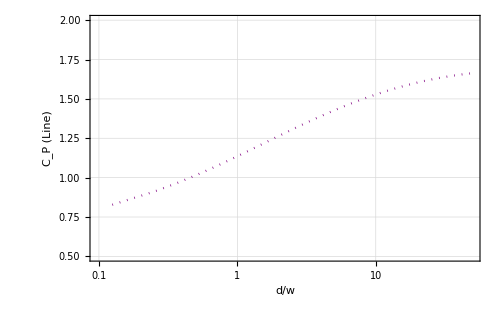

```mathematica
ListLogLinearPlot[{#⟦1⟧,(#⟦2⟧)^2-Sqrt[2] SubtractCoPLinewA8^2}&/@CoPLineListdwA8,PlotTheme->"Detailed",PlotStyle->{Dotted,Purple},Joined->True,PlotRange->{{0,50},{0.5,2}},Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"]
```

```mathematica
(*Taking the Square doesn't seem to make sense.*)
```

#### Analysis w=10

```mathematica
Length[CoPLineListdwA10]
```

491

```mathematica
Normal[NonlinearModelFit[({#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10)⟦2;;491⟧,a+b Log[x],{a,b},x]]
```

-0.102989+0.0272448 Log[x]

```mathematica
(*There is no Log[x] function that captures the behaviour of Subscript[C, P][w=10](d/w) for all values of d/w.*)
```

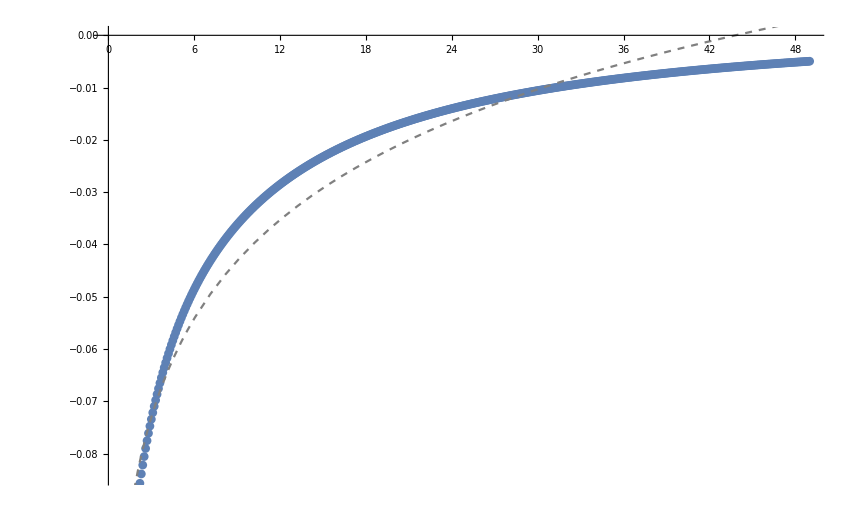

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10],Plot[-0.10298907424267817+0.027244765921281063 Log[x],{x,0,50},PlotStyle->{Dashed,Gray}]]
```

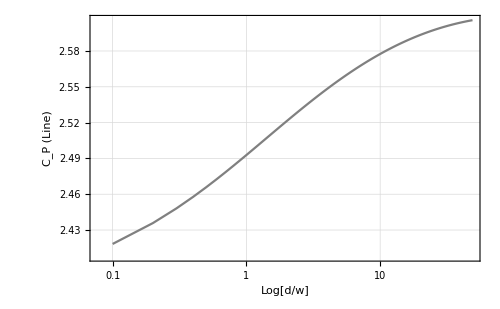

```mathematica
ListLogLinearPlot[CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Gray},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]
```

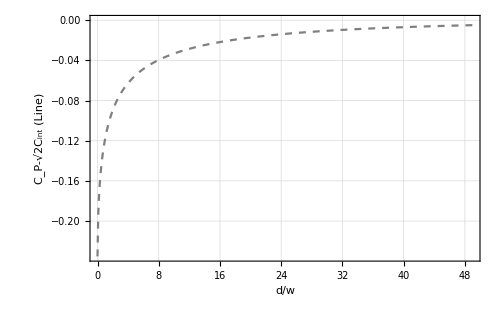

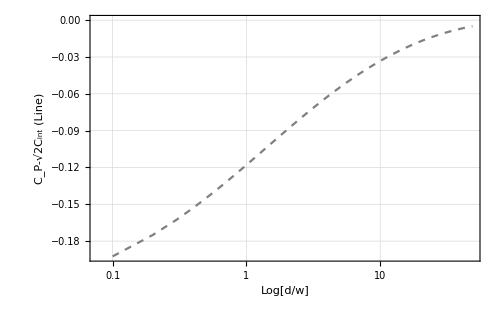

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Dashed,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P-√2C_int (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]
ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Dashed,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P-√2C_int (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]
```

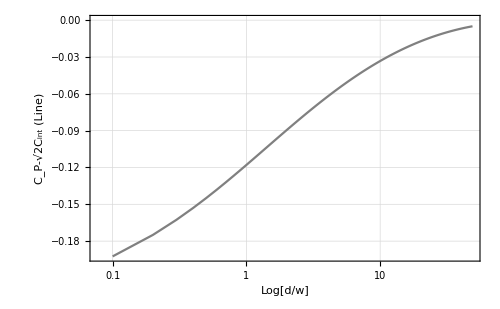

```mathematica
ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->Gray,Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P-√2C_int (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPLineLogw10.pdf",%823,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CoPLineLogw10.pdf

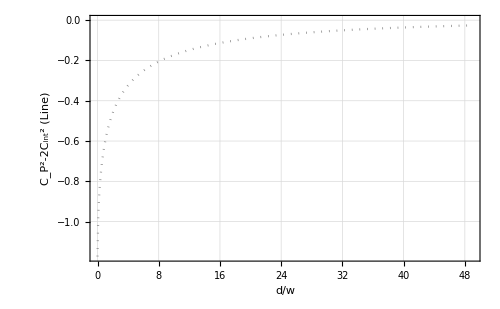

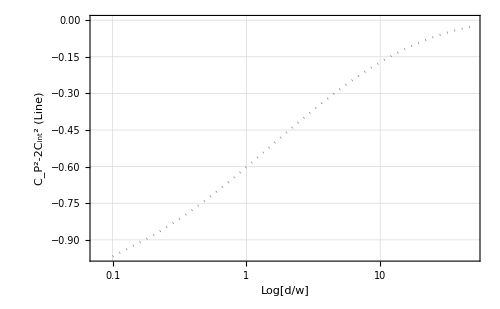

```mathematica
ListPlot[{#⟦1⟧,(#⟦2⟧)^2-2 SubtractCoPLinewA10^2}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Dotted,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P^2-2C_int^2 (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]
ListLogLinearPlot[{#⟦1⟧,(#⟦2⟧)^2-2 SubtractCoPLinewA10^2}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Dotted,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P^2-2C_int^2 (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]
```

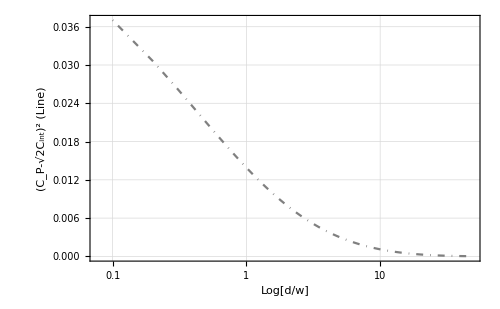

```mathematica
ListLogLinearPlot[{#⟦1⟧,(#⟦2⟧-Sqrt[2]SubtractCoPLinewA10)^2}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{DotDashed,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "(C_P-√2C_int)^2 (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Gray"w=10"]
```

```mathematica
(*This last one is probable not a good idea.*)
```

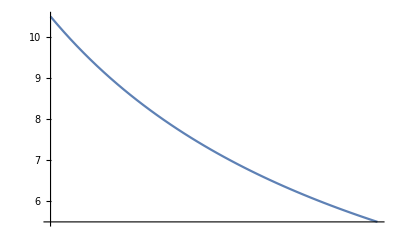

```mathematica
LogLinearPlot[1/Log[x],{x,1.1,1.2}]
```

### Back to the Analysis for w=10

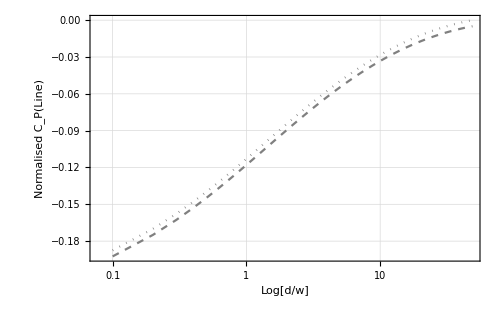

```mathematica
Show[ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Dashed,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "Normalised C_P(Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->"Dashed:Subtr.√2C_int"],ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA10]⟦2⟧}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Dotted,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "Normalised C_P (Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->"Dotted:Subtr.Max[C_P]"]]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/ComparisonNormCoPLine.pdf",%532,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/ComparisonNormCoPLine.pdf

```mathematica
(*Subtract complexity of purification for a single interval of changing w, with a f actor of 2 or Sqrt[2]*)
```

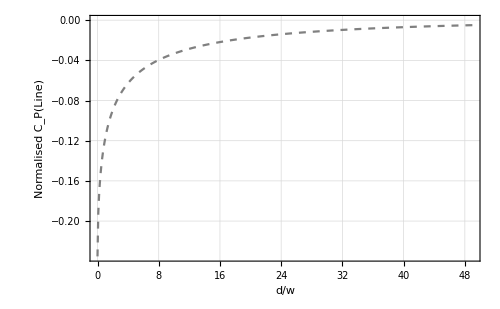

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10,PlotTheme->"Detailed",PlotStyle->{Dashed,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "Normalised C_P(Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->"Dashed:Subtr.√2C_int"]
```

```mathematica
NormCoPLinew1={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA1}&/@CoPLineListdwA1;
```

```mathematica
NormCoPLinew2={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA2}&/@CoPLineListdwA2;
```

```mathematica
NormCoPLinew3={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA3}&/@CoPLineListdwA3;
```

```mathematica
NormCoPLinew4={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA4}&/@CoPLineListdwA4;
```

```mathematica
NormCoPLinew5={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA5}&/@CoPLineListdwA5;
```

```mathematica
NormCoPLinew6={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA6}&/@CoPLineListdwA6;
```

```mathematica
NormCoPLinew8={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA8}&/@CoPLineListdwA8;
```

```mathematica
NormCoPLinew10={#⟦1⟧,#⟦2⟧-Sqrt[2]SubtractCoPLinewA10}&/@CoPLineListdwA10;
```

```mathematica
ListPlot[NormCoPLinew10,PlotTheme->"Detailed",PlotStyle->{Dashed,Gray},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "Normalised C_P(Line)"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->"Dashed:Subtr.√2C_int"]
```

-Graphics-

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;491⟧,a Log[x]+b,{a,b},x]]
```

-0.102989+0.0272448 Log[x]

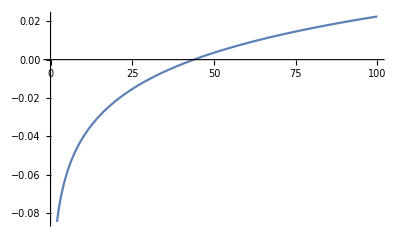

```mathematica
Plot[-0.10298907424267817+0.027244765921281038 Log[x],{x,0,100}]
```

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;491⟧,a x+b x^2 + c,{a,b,c},x]]
```

-0.0892449+0.00505836 x-0.0000733903 x^2

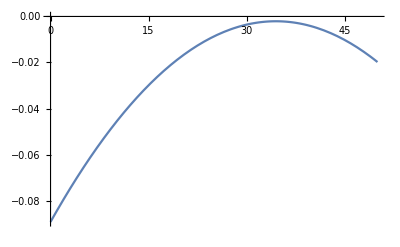

```mathematica
Plot[-0.08924493509117762+0.005058360063814151 x-0.00007339025819327708 x^2,{x,0,50}]
```

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;491⟧,a Log[x]+b x + c,{a,b,c},x]]
```

-0.113375-0.000838242 x+0.0379221 Log[x]

```mathematica
D[(-0.11337478354104215-0.0008382422389304479 x+0.03792213707004785 Log[x]), x]
```

-0.000838242+0.0379221/x

```mathematica
Solve[-0.0008382422389304479+0.03792213707004785/x==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→45.2401}}

```mathematica
(*At this point the solution begins to decay.*)
```

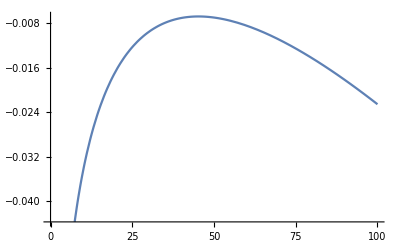

```mathematica
Plot[-0.11337478354104215-0.0008382422389304479 x+0.03792213707004785 Log[x],{x,0,100}]
```

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;491⟧,a Log[x]+b x + c x^2+d,{a,b,c,d},x]]
```

-0.113504-0.00136084 x+7.79898×10^-6 x^2+0.0402319 Log[x]

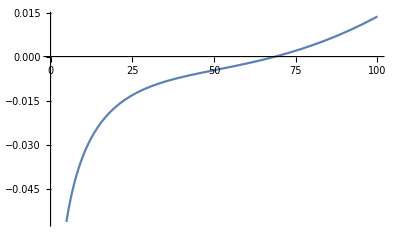

```mathematica
Plot[-0.11350417033737706-0.001360841982982834 x+7.798982211736444*^-6 x^2+0.04023188384750766 Log[x],{x,0,100}]
```

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;491⟧,a Log[x]+b x +c/x+d,{a,b,c,d},x]]
```

-0.113966+0.000363667/x-0.000852453 x+0.0382291 Log[x]

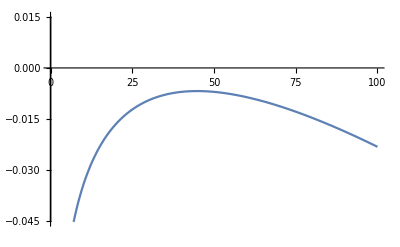

```mathematica
Plot[-0.11396632135011703+0.0003636670379283673/x-0.0008524534884795333 x+0.03822908665130108 Log[x],{x,0,100}]
```

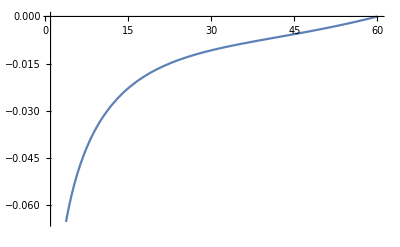

```mathematica
Plot[-0.11778332659762733+0.0025828065048558724/x-0.0017767551376695928 x+0.000012499612445030845 x^2+0.043804015011190085 Log[x],{x,1,60}]
```

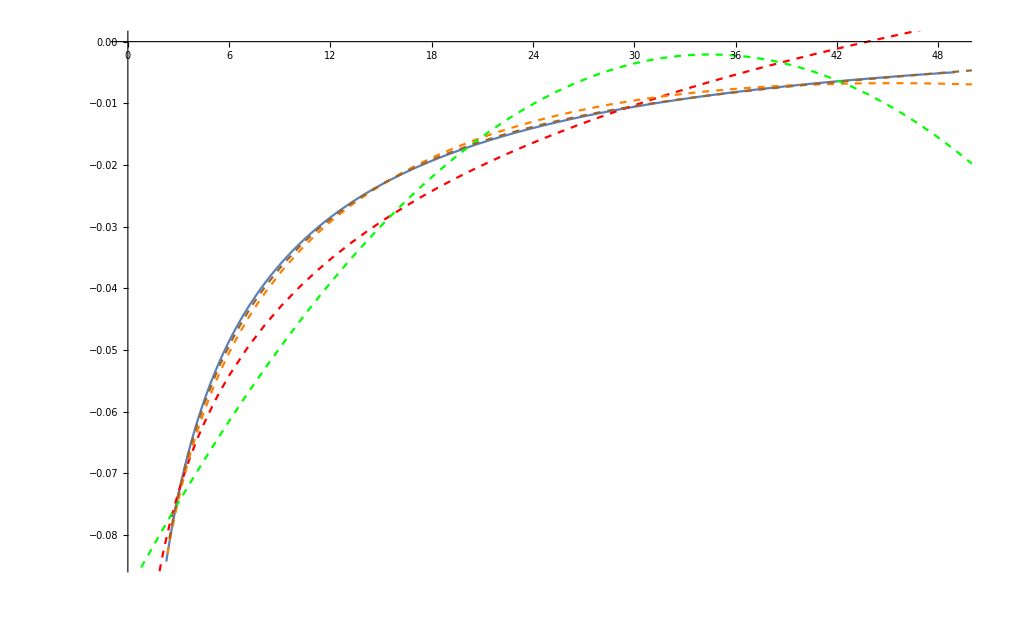

```mathematica
Show[ListPlot[NormCoPLinew10,Joined->True],Plot[-0.10298907424267817+0.027244765921281038 Log[x],{x,0,50},PlotStyle->{Dashed,Red}],Plot[-0.11337478354104215-0.0008382422389304479 x+0.03792213707004785 Log[x],{x,0,50},PlotStyle->{Dashed,Orange}],Plot[-0.08924493509117762+0.005058360063814151 x-0.00007339025819327708 x^2,{x,0,50},PlotStyle->{Dashed,Darker,Green}],Plot[-0.11350417033737706-0.001360841982982834 x+7.798982211736444*^-6 x^2+0.04023188384750766 Log[x],{x,0,50},PlotStyle->{Dashed,Brown}]]
```

```mathematica
(*A single logarithmic function does not fit the data well.*)
```

```mathematica
Length[NormCoPLinew10]
```

491

```mathematica
NormCoPLinew10⟦1;;6⟧//N
```

{{0.,-0.235159},{0.1,-0.192425},{0.2,-0.17493},{0.3,-0.162618},{0.4,-0.152946},{0.5,-0.144946}}

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;6⟧,a Log[x]+b,{a,b},x]]
```

-0.126054+0.0293798 Log[x]

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;6⟧,a Exp[x]+b,{a,b},x]]
```

-0.281538+0.0850562 ⅇ^x

```mathematica
Normal[LinearModelFit[NormCoPLinew10⟦1;;6⟧,x,x]]
```

-0.218729+0.166232 x

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦2;;6⟧,a Log[x]+b x + c,{a,b,c},x]]
```

-0.149889+0.038091 x+0.0201558 Log[x]

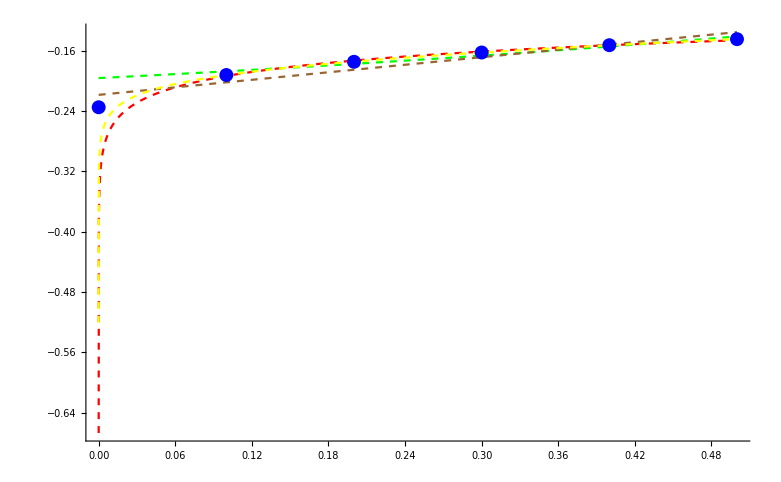

```mathematica
Show[Plot[-0.12605443364618224+0.029379844923203332 Log[x],{x,0,0.5},PlotRange->All,PlotStyle->{Dashed,Red}],Plot[-0.28153814156720003+0.08505620838845011 ⅇ^x,{x,0,0.5},PlotRange->All,PlotStyle->{Dashed,Green}],Plot[-0.21872854737172556+0.1662320355807148 x,{x,0,0.5},PlotRange->All,PlotStyle->{Dashed,Brown}],Plot[-0.14988882653602117+0.03809099854918187 x+0.020155835113879476 Log[x],{x,0,0.5},PlotRange->All,PlotStyle->{Dashed,Yellow}],ListPlot[NormCoPLinew10⟦1;;6⟧,PlotStyle->Blue,Joined->False]]
```

```mathematica
(*The best fit is still a logarithmic.*)
```

```mathematica
NormCoPLinew10⟦6;;51⟧//N
```

{{0.5,-0.144946},{0.6,-0.138121},{0.7,-0.132174},{0.8,-0.12691},{0.9,-0.122196},{1.,-0.117933},{1.1,-0.114048},{1.2,-0.110484},{1.3,-0.107196},{1.4,-0.104148},{1.5,-0.101309},{1.6,-0.0986572},{1.7,-0.0961703},{1.8,-0.0938314},{1.9,-0.0916258},{2.,-0.0895408},{2.1,-0.0875653},{2.2,-0.0856896},{2.3,-0.0839055},{2.4,-0.0822053},{2.5,-0.0805826},{2.6,-0.0790315},{2.7,-0.0775467},{2.8,-0.0761235},{2.9,-0.0747576},{3.,-0.0734453},{3.1,-0.072183},{3.2,-0.0709676},{3.3,-0.0697962},{3.4,-0.0686662},{3.5,-0.0675752},{3.6,-0.0665209},{3.7,-0.0655013},{3.8,-0.0645145},{3.9,-0.0635588},{4.,-0.0626326},{4.1,-0.0617343},{4.2,-0.0608627},{4.3,-0.0600163},{4.4,-0.0591941},{4.5,-0.0583948},{4.6,-0.0576174},{4.7,-0.056861},{4.8,-0.0561246},{4.9,-0.0554073},{5.,-0.0547084}}

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦6;;51⟧,a Log[x]+b,{a,b},x]]
```

-0.117466+0.0396252 Log[x]

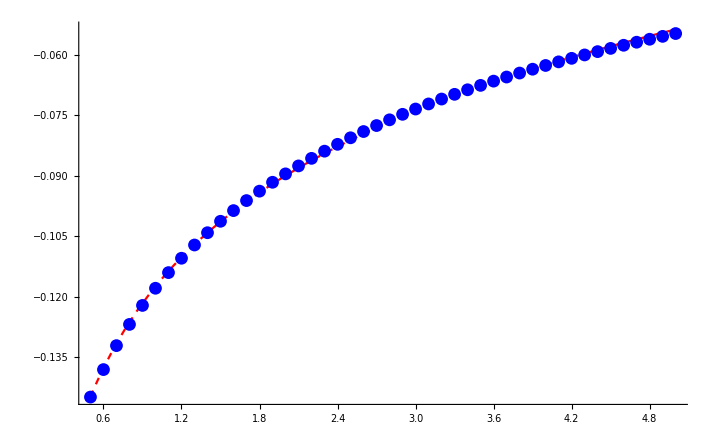

```mathematica
Show[Plot[-0.1174663459761558+0.03962517613733544 Log[x],{x,0.5,5},PlotRange->All,PlotStyle->{Dashed,Red}],ListPlot[NormCoPLinew10⟦6;;51⟧,PlotStyle->Blue,Joined->False]]
```

```mathematica
(*In this region, complexity does behave logarithmically.*)
```

```mathematica
NormCoPLinew10⟦51;;101⟧//N
```

{{5.,-0.0547084},{5.1,-0.054027},{5.2,-0.0533625},{5.3,-0.0527141},{5.4,-0.0520813},{5.5,-0.0514634},{5.6,-0.0508599},{5.7,-0.0502702},{5.8,-0.0496938},{5.9,-0.0491302},{6.,-0.0485789},{6.1,-0.0480396},{6.2,-0.0475117},{6.3,-0.046995},{6.4,-0.046489},{6.5,-0.0459933},{6.6,-0.0455077},{6.7,-0.0450318},{6.8,-0.0445652},{6.9,-0.0441077},{7.,-0.0436591},{7.1,-0.0432189},{7.2,-0.0427871},{7.3,-0.0423632},{7.4,-0.0419472},{7.5,-0.0415386},{7.6,-0.0411374},{7.7,-0.0407434},{7.8,-0.0403562},{7.9,-0.0399758},{8.,-0.0396019},{8.1,-0.0392344},{8.2,-0.0388731},{8.3,-0.0385178},{8.4,-0.0381683},{8.5,-0.0378246},{8.6,-0.0374864},{8.7,-0.0371536},{8.8,-0.0368261},{8.9,-0.0365038},{9.,-0.0361865},{9.1,-0.035874},{9.2,-0.0355664},{9.3,-0.0352634},{9.4,-0.0349649},{9.5,-0.0346709},{9.6,-0.0343812},{9.7,-0.0340958},{9.8,-0.0338145},{9.9,-0.0335372},{10.,-0.0332639}}

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦51;;101⟧,a Log[x]+b,{a,b},x]]
```

-0.103825+0.0308076 Log[x]

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦51;;101⟧,a Log[x]+b x + c,{a,b,c},x]]
```

-0.114189-0.00148325 x+0.041579 Log[x]

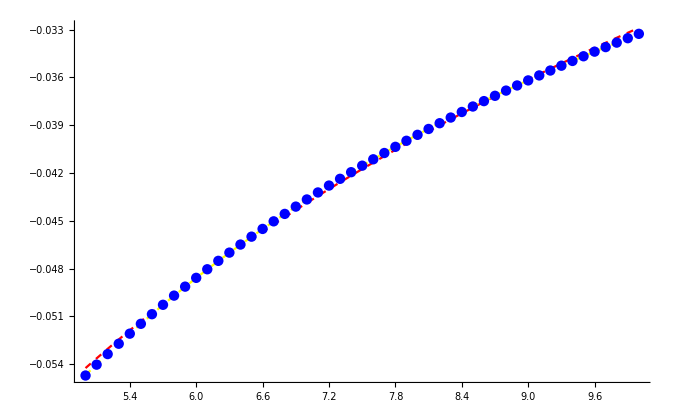

```mathematica
Show[Plot[-0.10382527596816393+0.030807619952590355 Log[x],{x,5,10},PlotRange->All,PlotStyle->{Dashed,Red}],Plot[-0.11418921482650206-0.0014832488713296035 x+0.04157903998514259 Log[x],{x,5,10},PlotRange->All,PlotStyle->{Dashed,Yellow}],ListPlot[NormCoPLinew10⟦51;;101⟧,PlotStyle->Blue,Joined->False]]
```

```mathematica
(*Not quite. But close*)
```

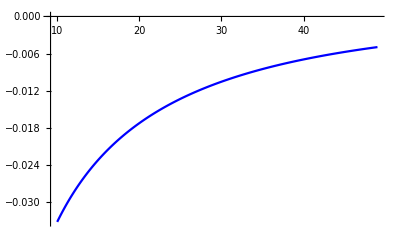

```mathematica
ListPlot[NormCoPLinew10⟦101;;491⟧,PlotStyle->Blue,Joined->True]
```

```mathematica
Normal[LinearModelFit[NormCoPLinew10⟦101;;491⟧,x,x]]
```

-0.0312949+0.000614268 x

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦101;;491⟧,a Log[x]+b,{a,b},x]]
```

-0.0686092+0.0168047 Log[x]

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦101;;491⟧,a x + b x^2+c,{a,b,c},x]]
```

-0.0464673+0.00181932 x-0.0000204246 x^2

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦101;;491⟧,a x + b x^2+c Log[x] + d,{a,b,c,d},x]]
```

-0.104853-0.00100791 x+4.98238×10^-6 x^2+0.0352981 Log[x]

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦101;;491⟧,a x +b x^2+c x^3 + d Log[x]+e,{a,b,c,d,e},x]]
```

-0.109811-0.00150619 x+0.0000147149 x^2-7.83117×10^-8 x^3+0.0391909 Log[x]

```mathematica
Normal[NonlinearModelFit[NormCoPLinew10⟦101;;491⟧,a x +b Log[x] + c,{a,b,c},x]]
```

-0.0944004-0.000470623 x+0.0288317 Log[x]

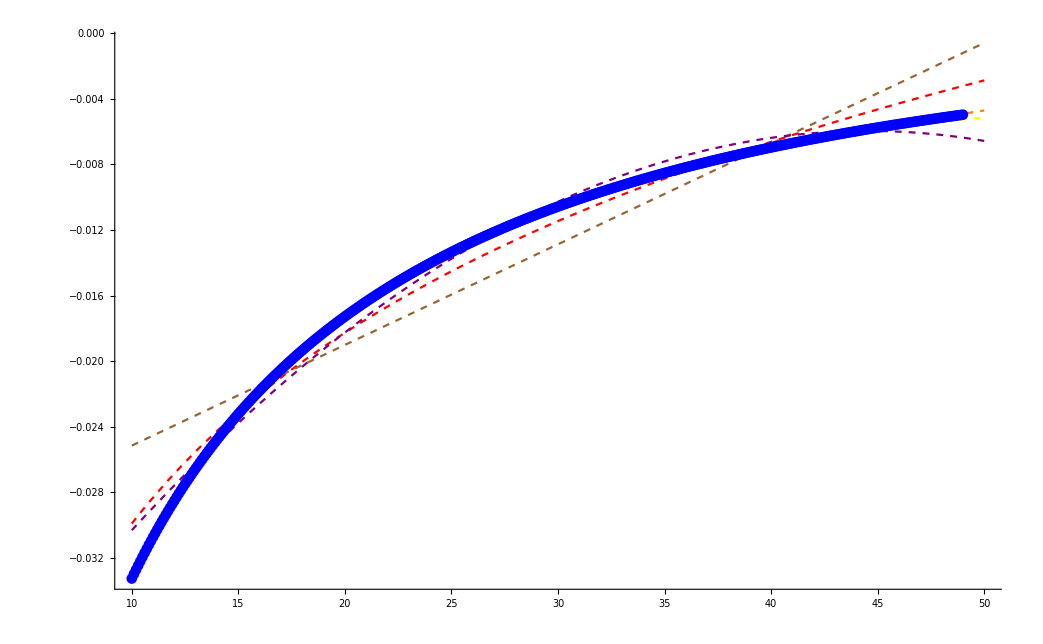

```mathematica
Show[Plot[-0.06860920592144347+0.016804683063027407 Log[x],{x,10,50},PlotRange->All,PlotStyle->{Dashed,Red}],Plot[-0.03129486716361898+0.0006142682822016514 x,{x,10,50},PlotRange->All,PlotStyle->{Dashed,Brown}],Plot[-0.04646729449174604+0.0018193207320360608 x-0.000020424617793803483 x^2,{x,10,50},PlotRange->All,PlotStyle->{Dashed,Purple}],Plot[-0.10485277645791823-0.0010079062196399389 x+4.982377609557456*^-6 x^2+0.03529812733283644 Log[x],{x,10,50},PlotRange->All,PlotStyle->{Dashed,Orange}],Plot[-0.09440044360449218-0.00047062344374469917 x+0.028831679126147314 Log[x],{x,10,50},PlotRange->All,PlotStyle->{Dashed,Yellow}],ListPlot[NormCoPLinew10⟦101;;491⟧,PlotStyle->Blue,Joined->False]]
```

```mathematica
(*What sort of behaviour is this? Looks like it could be fit with something like a x + b Log[x] + c. Weird huh?*)
```

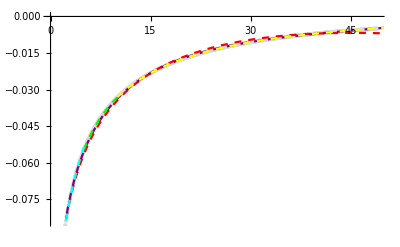

```mathematica
Show[ListPlot[NormCoPLinew10,Joined->False,PlotStyle->LightGray,PlotLegends->LightGray"NormCoPLinew10"],Plot[-0.11337478354104215-0.0008382422389304479 x+0.03792213707004785 Log[x],{x,0,50},PlotStyle->{Dashed,Red},PlotLegends->Red"-0.11337478354104215`-0.0008382422389304479` x+0.03792213707004785` Log[x]"],Plot[-0.11350417033737706-0.001360841982982834 x+7.798982211736444*^-6 x^2+0.04023188384750766 Log[x],{x,0,50},PlotStyle->{Dashed,Purple},PlotLegends->Purple"-0.11350417033737706`-0.001360841982982834` x+7.798982211736444`*^-6 x^2+0.04023188384750766` Log[x]"],Plot[-0.10485277645791823-0.0010079062196399389 x+4.982377609557456*^-6 x^2+0.03529812733283644 Log[x],{x,10,50},PlotRange->All,PlotStyle->{Dashed,Yellow},PlotLegends->Yellow"-0.10485277645791823`-0.0010079062196399389` x+4.982377609557456`*^-6 x^2+0.03529812733283644` Log[x]"],Plot[-0.11418921482650206-0.0014832488713296035 x+0.04157903998514259 Log[x],{x,5,10},PlotRange->All,PlotStyle->{Dashed,Green},PlotLegends-> Green"-0.11418921482650206`-0.0014832488713296035` x+0.04157903998514259` Log[x]"],Plot[-0.1174663459761558+0.03962517613733544 Log[x],{x,0.5,5},PlotRange->All,PlotStyle->{Dashed,Cyan},PlotLegends-> Cyan"-0.1174663459761558`+0.03962517613733544` Log[x]"]]
```

```mathematica
Fitw10[x_]:=-0.1135-0.00136x+7.799*^-6 x^2+0.04023Log[x];
```

```mathematica
(*Qualitatively the behaviour we desire:*)
```

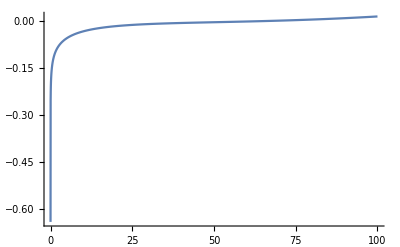

```mathematica
Plot[Fitw10[x],{x,0,100},PlotRange->All]
```

```mathematica
(*SubtractCoPLinewA10=CoPValLine[1/1000,1,10,0,0]=1.8460904817883974*)
```

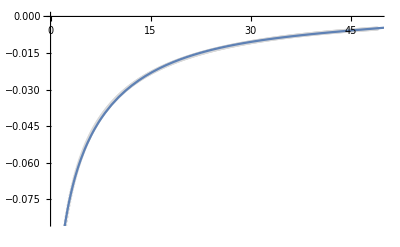

```mathematica
Show[ListPlot[NormCoPLinew10,Joined->False,PlotStyle->LightGray,PlotLegends->LightGray"NormCoPLinew10"],Plot[Fitw10[x],{x,0,50},PlotRange->All],Axes-> True]
```

```mathematica
(*Red and Purple lines cover all ranges of d/w. The other colours cover just a portion.*)
```

## EoP

### Data

```mathematica
(*EoPLineListdwA1=Table[{d,EoPValLine[1/100,1,1,1,d]},{d,0,(100-(1+1))/2}]*)
```

```mathematica
EoPLineListdwA1={{0,0.5993252712220052},{1,0.5178593081056226},{2,0.41760686450470985},{3,0.3537098084593703},{4,0.3089881456029052},{5,0.2754253745003976},{6,0.24899871943998209},{7,0.22746374005530878},{8,0.20945971901756436},{9,0.19410738165443886},{10,0.18080948419698972},{11,0.16914382686934942},{12,0.1588020615183416},{13,0.14955280639251955},{14,0.1412184218155044},{15,0.1336598390645045},{16,0.1267663338181898},{17,0.1204484418528887},{18,0.11463293525402443},{19,0.10925918384854227},{20,0.10427647096097334},{21,0.09964198093442456},{22,0.09531926641087574},{23,0.09127706726606977},{24,0.08748838736896858},{25,0.08392976656482098},{26,0.08058069956430924},{27,0.07742316852546877},{28,0.07444126331103962},{29,0.0716208713033469},{30,0.06894942103246393},{31,0.06641566992940143},{32,0.0640095268880401},{33,0.06172190289364343},{34,0.059544585606751035},{35,0.05747013183037736},{36,0.055491776508751395},{37,0.053603354478311105},{38,0.051799232731978506},{39,0.050074252543790165},{40,0.0484236784672368},{41,0.046843154536462164},{42,0.04532866554583237},{43,0.04387650316535227},{44,0.04248323632386075},{45,0.041145684764146095},{46,0.03986089588955814},{47,0.038626123990364025},{48,0.037438811953745765},{49,0.03629657474871652}};
```

```mathematica
(*EoPLineListdwA2=Table[{d/2,EoPValLine[1/200,1,2,2,d]},{d,0,(200-(2+2))/2}]*)
```

```mathematica
EoPLineListdwA2={{0,0.7113467596745356},{1/2,0.6844320134149999},{1,0.5459288579906731},{3/2,0.4754996989738839},{2,0.4260702150848506},{5/2,0.38842553614960723},{3,0.35832900468643925},{7/2,0.33345750113452066},{4,0.3124002238908653},{9/2,0.29423836668619624},{5,0.278341809779844},{11/2,0.26426075944408606},{6,0.2516636804286896},{13/2,0.24029967688993514},{7,0.22997464842896106},{15/2,0.22053558689761127},{8,0.21185990835562435},{17/2,0.20384801396909313},{9,0.19641796356310764},{19/2,0.18950161163499477},{10,0.18304171262252142},{21/2,0.17698976285291185},{11,0.1713043325396402},{23/2,0.1659497708132448},{12,0.16089519753234244},{25/2,0.15611372750169764},{13,0.15158179062798913},{27/2,0.1472786163116241},{14,0.1431858457748983},{29/2,0.13928716265991786},{15,0.13556798107580925},{31/2,0.1320152929879355},{16,0.12861728474675582},{33/2,0.1253634337253619},{17,0.12224416346630995},{35/2,0.11925073738054534},{18,0.11637527787356831},{37/2,0.11361055139097584},{19,0.11094996283839956},{39/2,0.10838743740263306},{20,0.1059174218920462},{41/2,0.10353478225640649},{21,0.10123478810403079},{43/2,0.09901307395669053},{22,0.09686556685506359},{45/2,0.09478852355251122},{23,0.09277843087590734},{47/2,0.09083202750982783},{24,0.0889463404924},{49/2,0.08711846396901123},{25,0.08534576886184253},{51/2,0.08362578366709186},{26,0.08195616637768936},{53/2,0.08033475056236604},{27,0.07875946767073003},{55/2,0.0772283904328296},{28,0.07573970231653318},{57/2,0.07429168341010911},{29,0.07288270922924647},{59/2,0.0715112593688123},{30,0.07017587896524194},{61/2,0.06887519527156893},{31,0.06760791138259177},{63/2,0.06637279210366327},{32,0.06516866408238647},{65/2,0.06399443748430392},{33,0.06284903005260936},{67/2,0.06173144917913037},{34,0.06064073525431715},{69/2,0.05957597653988504},{35,0.05853630019179442},{71/2,0.05752088090612688},{36,0.05652892358752961},{73/2,0.05555967165557846},{37,0.054612403522060204},{75/2,0.05368642463026055},{38,0.0527810699870143},{77/2,0.051895709923166666},{39,0.051029733498171914},{79/2,0.05018255755424021},{40,0.04935362439567873},{81/2,0.04854239542564068},{41,0.047748358239380215},{83/2,0.04697101209134731},{42,0.04620988453972541},{85/2,0.04546452055717289},{43,0.04473447529612788},{87/2,0.04401932671505354},{44,0.04331866705763353},{89/2,0.04263210210562377},{45,0.041959254398898485},{91/2,0.041299757949209745},{46,0.04065326082540295},{93/2,0.04001942371258371},{47,0.039397916586250276},{95/2,0.038788425760068614},{48,0.03819064329773877},{97/2,0.03760427455225269},{49,0.037029033341470105}};
```

```mathematica
(*EoPLineListdwA3=Table[{d/3,EoPValLine[1/300,1,3,3,d]},{d,0,(300-(3+3))/2}]*)
```

```mathematica
EoPLineListdwA3={{0,0.7778103333154892},{1/3,0.7679278192883736},{2/3,0.6201629341739527},{1,0.5477550986633415},{4/3,0.4968306503661003},{5/3,0.45777614726618465},{2,0.42630953742878974},{7/3,0.400111716853391},{8/3,0.37777956674728963},{3,0.358398601470363},{10/3,0.3413397263455976},{11/3,0.3261519785170685},{4,0.312501386164958},{13/3,0.3001339895354742},{14/3,0.2888523820093106},{5,0.2785002399463227},{16/3,0.26895178897597477},{17/3,0.2601044196227365},{6,0.2518734089052872},{19/3,0.24418804016644627},{20/3,0.23698872342195623},{7,0.2302248089734212},{22/3,0.22385292074021523},{23/3,0.2178356327125459},{8,0.212140462523087},{25/3,0.20673904040214736},{26/3,0.2016064612827949},{9,0.19672073441533477},{28/3,0.1920623879903009},{29/3,0.18761406992042315},{10,0.18336028802080767},{31/3,0.17928711464756492},{32/3,0.1753820326659007},{11,0.17163373083751296},{34/3,0.1680319518681291},{35/3,0.1645673974616576},{12,0.16123158017420322},{37/3,0.15801673060578134},{38/3,0.15491576722679132},{13,0.15192216184596066},{40/3,0.14902992114061875},{41/3,0.1462335508335401},{14,0.14352788624517152},{43/3,0.1409082677395109},{44/3,0.1383703032487825},{15,0.13590988200063148},{46/3,0.1335232918063559},{47/3,0.1312069733960941},{16,0.12895764298304085},{49/3,0.12677222937706312},{50/3,0.12464785820522259},{17,0.12258185067584529},{52/3,0.1205716673047334},{53/3,0.11861496164831438},{18,0.11670946259792708},{55/3,0.11485310054394735},{56/3,0.11304389800900141},{19,0.11127995777003774},{58/3,0.10955955784104165},{59/3,0.10788100973155262},{20,0.10624272948264904},{61/3,0.10464325923290421},{62/3,0.10308111572793893},{21,0.1015550135377333},{64/3,0.10006365133773702},{65/3,0.09860583640516177},{22,0.09718039620405498},{67/3,0.09578623836313907},{68/3,0.09442232384570835},{23,0.0930876552001566},{70/3,0.09178127628418374},{71/3,0.09050227732500483},{24,0.08924980249057964},{73/3,0.08802300869820986},{74/3,0.08682112256576985},{25,0.08564336070848014},{76/3,0.0844890247240701},{77/3,0.08335741037889374},{26,0.08224783511883618},{79/3,0.08115968259142033},{80/3,0.08009232573051374},{27,0.07904518194504204},{82/3,0.07801768132996464},{83/3,0.07700928799919576},{28,0.07601946520266167},{85/3,0.0750477204580614},{86/3,0.07409356704039705},{29,0.07315654026891547},{88/3,0.07223619240853385},{89/3,0.07133208911662688},{30,0.07044381567515409},{91/3,0.06957096932784483},{92/3,0.06871315973144496},{31,0.06787001227049747},{94/3,0.06704117251771907},{95/3,0.06622628455130046},{32,0.06542500822499261},{97/3,0.06463671491688114},{98/3,0.0638616945205325},{33,0.06309816853435447},{100/3,0.06234934550347404},{101/3,0.06161150871156572},{34,0.06088577931725542},{103/3,0.060171262153784856},{104/3,0.05946802955606582},{35,0.05877583290359466},{106/3,0.058094423161294324},{107/3,0.05742357128967383},{36,0.05676303815222501},{109/3,0.05611261024926517},{110/3,0.05547206511317108},{37,0.05484119942678792},{112/3,0.054219804615902936},{113/3,0.05360768356921667},{38,0.053004647640884514},{115/3,0.05241050705463879},{116/3,0.051825081083568064},{39,0.05124819555280371},{118/3,0.050679675218186705},{119/3,0.050119354721090664},{40,0.049567074604170494},{121/3,0.04902267322478586},{122/3,0.04848599701832165},{41,0.04795690080638734},{124/3,0.047435232968363855},{125/3,0.04692085417271373},{42,0.04641362692743447},{127/3,0.04591341487171681},{128/3,0.0454200866717386},{43,0.04493351628627046},{130/3,0.044453579203540386},{131/3,0.043980150143813374},{44,0.04351311295123779},{133/3,0.043052351976066355},{134/3,0.04259775278423764},{45,0.04214920863528207},{136/3,0.04170660686471152},{137/3,0.04126984606719962},{46,0.04083882244845957},{139/3,0.04041343727978827},{140/3,0.03999359069859418},{47,0.03957918721632596},{142/3,0.03917013432687015},{143/3,0.03876634325290794},{48,0.03836772121322797},{145/3,0.03797418093401384},{146/3,0.03758564105648046},{49,0.03720201459950603}};
```

```mathematica
(*EoPLineListdwA4=Table[{d/4,EoPValLine[1/400,1,4,4,d]},{d,0,(400-(4+4))/2}]*)
```

```mathematica
EoPLineListdwA4={{0,0.8252245703088201},{1/4,0.8217654840090856},{1/2,0.6720214238171638},{3/4,0.5989370427748971},{1,0.5474587145380321},{5/4,0.5078187142168662},{3/2,0.4757292742165597},{7/4,0.4488859480810576},{2,0.4259000750747629},{9/4,0.40586791685009577},{5/2,0.3881676407346007},{11/4,0.3723528640483218},{3,0.35809232754910636},{13/4,0.3451334730306148},{7/2,0.33327945414250326},{15/4,0.32237401543896343},{4,0.3122909131529879},{17/4,0.3029270170491158},{9/2,0.29419693272994063},{19/4,0.28602915059277717},{5,0.27836327443905984},{21/4,0.27114781097146085},{11/2,0.2643386879455001},{23/4,0.25789766580535955},{6,0.25179155162599587},{25/4,0.24599129311927337},{13/2,0.2404713371087475},{27/4,0.2352090945426333},{7,0.23018452757969554},{29/4,0.22537971151018946},{15/2,0.22077866058113954},{31/4,0.21636700939840156},{8,0.21213180243946986},{33/4,0.20806129202997714},{17/2,0.2041448667862078},{35/4,0.200372839499537},{9,0.1967364045659358},{37/4,0.19322747822085168},{19/2,0.18983867933735327},{39/4,0.18656319598343996},{10,0.18339481823634068},{41/4,0.1803277291281576},{21/2,0.1773566266365097},{43/4,0.17447656238466736},{11,0.17168296289789034},{45/4,0.16897157154559317},{23/2,0.16633841306183908},{47/4,0.1637798131075196},{12,0.16129231997094925},{49/4,0.15887270037753545},{25/2,0.15651795676582206},{51/4,0.15422524344309005},{13,0.15199192548589574},{53/4,0.14981548389993296},{27/2,0.14769356532699587},{55/4,0.1456240142172237},{14,0.14360469979504975},{57/4,0.14163366869626023},{29/2,0.13970904831912984},{59/4,0.13782911594943684},{15,0.1359921863577731},{61/4,0.13419666906951855},{31/2,0.13244108964612883},{63/4,0.13072402408490175},{16,0.12904414869402014},{65/4,0.12740014737118976},{33/2,0.12579081506286846},{67/4,0.12421497752156427},{17,0.12267155648071465},{69/4,0.1211594819212286},{35/2,0.1196777494718281},{71/4,0.11822543030480769},{18,0.11680153810358083},{73/4,0.11540526816970609},{37/2,0.11403572478320662},{75/4,0.11269214815940114},{19,0.11137373807549443},{77/4,0.1100797728928932},{39/2,0.10880955865134925},{79/4,0.10756240130180646},{20,0.10633763961637599},{81/4,0.10513467766923637},{41/2,0.10395288772366659},{83/4,0.10279171196314163},{21,0.1016505867032818},{85/4,0.10052898085772669},{43/2,0.09942638126760157},{87/4,0.09834231470047866},{22,0.09727627029850087},{89/4,0.09622779456573431},{45/2,0.09519645802358706},{91/4,0.09418183148080164},{23,0.09318348697296407},{93/4,0.09220105263926931},{47/2,0.09123412123287628},{95/4,0.09028212699083746},{24,0.08934514599014855},{97/4,0.0884221566591546},{49/2,0.08751301841305444},{99/4,0.08661891205502743},{25,0.08573816877035044},{101/4,0.08487008867012685},{51/2,0.08401511245179961},{103/4,0.0831724887181773},{26,0.0823421671697632},{105/4,0.08152386994783406},{53/2,0.0807173572790095},{107/4,0.0799223754027202},{27,0.07913865352621013},{109/4,0.07836598451614599},{55/2,0.07760411344275253},{111/4,0.07685286023867859},{28,0.07611196024377367},{113/4,0.07538122261288005},{57/2,0.07466044080811643},{115/4,0.0739494137876732},{29,0.07324795444919624},{117/4,0.07255586986281085},{59/2,0.07187297874454077},{119/4,0.07119910203322935},{30,0.0705340646037286},{121/4,0.0698777020405974},{61/2,0.06922984779295716},{123/4,0.06859034116979107},{31,0.06795902817220789},{125/4,0.06733575469032257},{63/2,0.06672037691108676},{127/4,0.06611274989507462},{32,0.06551273308414463},{129/4,0.06492018450212991},{65/2,0.06433498431878062},{131/4,0.06375698178982378},{33,0.06318606693909473},{133/4,0.06262211134017616},{67/2,0.06206499415737905},{135/4,0.061514593717001166},{34,0.06097079769780349},{137/4,0.060433494425534286},{69/2,0.05990257591069285},{139/4,0.05937792846335735},{35,0.05885945348657701},{141/4,0.05834704891203221},{71/2,0.057840608707807314},{143/4,0.057340041007308606},{36,0.056845244133284886},{145/4,0.05635613367635777},{73/2,0.055872608390404616},{147/4,0.05539458864903315},{37,0.054921977759429516},{149/4,0.05445469666326656},{75/2,0.053992662020375934},{151/4,0.053535786747731},{38,0.05308399496214066},{153/4,0.05263720650765626},{77/2,0.05219534605774818},{155/4,0.05175833778530871},{39,0.05132610840040029},{157/4,0.05089858439678883},{79/2,0.05047569427287812},{159/4,0.050057373492532406},{40,0.0496435519451511},{161/4,0.049234161857459005},{81/2,0.048829140001014563},{163/4,0.04842842243620236},{41,0.04803194592153601},{165/4,0.047639648678007726},{83/2,0.04725147570465816},{167/4,0.0468673588405316},{42,0.04648724952071403},{169/4,0.046111085880687894},{85/2,0.04573881389192838},{171/4,0.04537037771824945},{43,0.04500572728725959},{173/4,0.044644806384884175},{87/2,0.044287566600698686},{175/4,0.043933953829506406},{44,0.043583921430581145},{177/4,0.04323742840925878},{89/2,0.04289440388743534},{179/4,0.042554822463180944},{45,0.04221863026313784},{181/4,0.04188578540149536},{91/2,0.04155623800512862},{183/4,0.041229949691838},{46,0.04090687428841868},{185/4,0.040586971594947466},{93/2,0.04027019886112132},{187/4,0.039956518049060794},{47,0.03964588421086161},{189/4,0.039338261330575844},{95/2,0.039033613215780555},{191/4,0.038731897347603864},{48,0.03843308068173072},{193/4,0.03813712254761058},{97/2,0.03784398938705956},{195/4,0.03755364485225467},{49,0.03726605432793727}};
```

### Plots

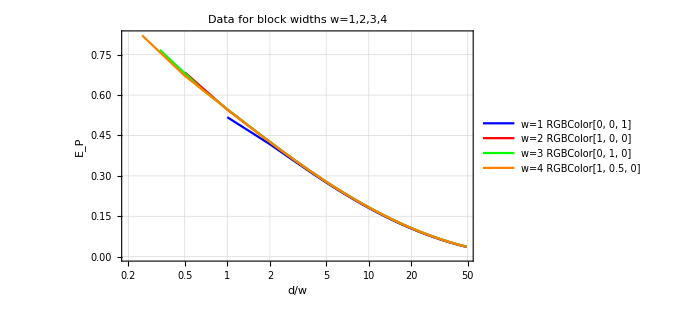

```mathematica
Show[ListLogLinearPlot[{EoPLineListdwA1,EoPLineListdwA2,EoPLineListdwA3,EoPLineListdwA4},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4"}]]
```

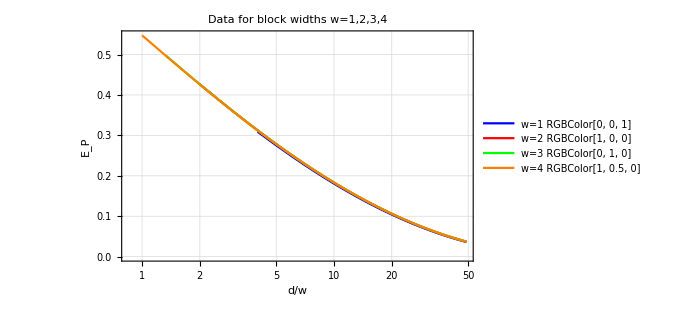

```mathematica
Show[ListLogLinearPlot[{EoPLineListdwA1⟦5;;50⟧,EoPLineListdwA2⟦5;;99⟧,EoPLineListdwA3⟦5;;148⟧,EoPLineListdwA4⟦5;;197⟧},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4"}]]
```

```mathematica
Show[ListLogLinearPlot[{EoPLineListdwA1⟦1;;5⟧,EoPLineListdwA2⟦1;;5⟧,EoPLineListdwA3⟦1;;5⟧,EoPLineListdwA4⟦1;;5⟧},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green,Orange,Cyan,Brown,Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "E_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3",Orange"w=4"}]]
```

## Comparison of CoP Circle VS Line

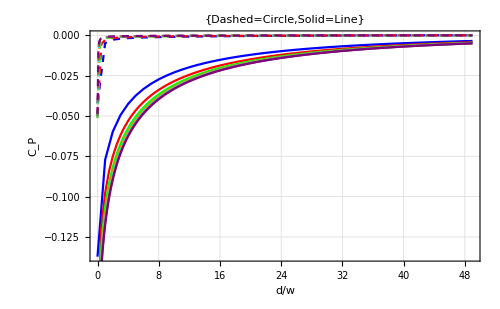

```mathematica
Show[ListPlot[NormCoPLinew1,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Blue"w=1"],ListPlot[NormCoPLinew2,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Red"w=2"],ListPlot[NormCoPLinew3,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Green"w=3"],ListPlot[NormCoPLinew4,PlotTheme->"Detailed",PlotStyle->{Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Orange"w=4"],ListPlot[NormCoPLinew5,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Cyan"w=5"],ListPlot[NormCoPLinew6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[NormCoPLinew8,PlotTheme->"Detailed",PlotStyle->{Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Purple"w=8"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN100dA1]⟦2⟧}&/@CoPCircleListN100dA1,PlotTheme->"Detailed",PlotStyle->{Dashed ,Blue},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3,4,5,6,8"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN200dA2]⟦2⟧}&/@CoPCircleListN200dA2,PlotTheme->"Detailed",PlotStyle->{Dashed, Red},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN300dA3]⟦2⟧}&/@CoPCircleListN300dA3,PlotTheme->"Detailed",PlotStyle->{Dashed, Green},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN400dA4]⟦2⟧}&/@CoPCircleListN400dA4,PlotTheme->"Detailed",PlotStyle->{Dashed ,Orange},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN500dA5]⟦2⟧}&/@CoPCircleListN500dA5,PlotTheme->"Detailed",PlotStyle->{Dashed,Cyan},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN600dA6]⟦2⟧}&/@CoPCircleListN600dA6,PlotTheme->"Detailed",PlotStyle->{Dashed,Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN800dA8]⟦2⟧}&/@CoPCircleListN800dA8,PlotTheme->"Detailed",PlotStyle->{Dashed,Purple},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500],PlotLabel->{"Dashed=Circle","Solid=Line"}]
```

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CPCirclevsLine.pdf",%821,"PDF"]
```

/Users/HugoCamargo89/Desktop/Projects_AEI/Purifications_Project/Field_Theory/Notes_Nov_2019/CPCirclevsLine.pdf

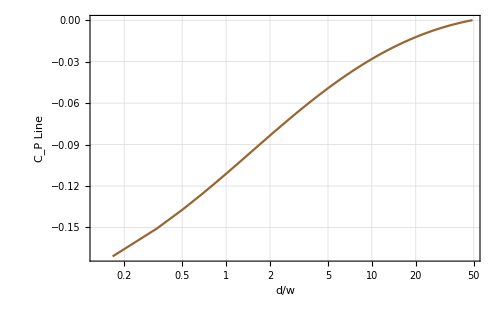

```mathematica
ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA6]⟦2⟧}&/@CoPLineListdwA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P Line"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"]
```

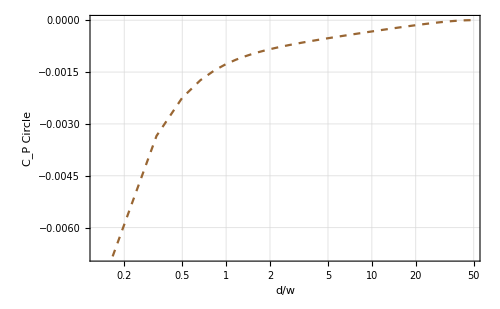

```mathematica
ListLogLinearPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN600dA6]⟦2⟧}&/@CoPCircleListN600dA6,PlotTheme->"Detailed",PlotStyle->{Dashed,Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P Circle"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"]
```

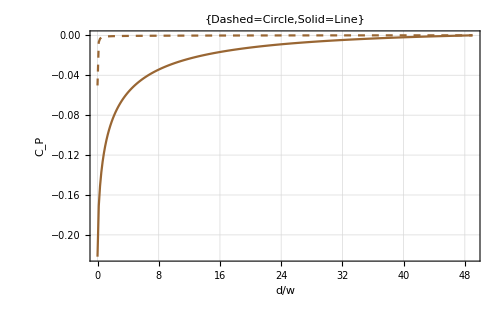

```mathematica
Show[ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPLineListdwA6]⟦2⟧}&/@CoPLineListdwA6,PlotTheme->"Detailed",PlotStyle->{Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLegends->Brown"w=6"],ListPlot[{#⟦1⟧,#⟦2⟧-Last[CoPCircleListN600dA6]⟦2⟧}&/@CoPCircleListN600dA6,PlotTheme->"Detailed",PlotStyle->{Dashed,Brown},Joined->True,PlotRange->All,Joined->True,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"StyleBox[\"d\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"w\",FontSlant->\"Italic\"]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500],PlotLabel->{"Dashed=Circle","Solid=Line"}]
```

## Comparison of EoP Circle VS Line